# Finding the best

```mathematica
Exit[]
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
SetDirectory[NotebookDirectory[]];
Get["fittings.m"];
Get["qplotter.m"];
Get["qalculations.m"];
```

## C2v (all Ln) Infinite Truncation Energy pathfinder approach with full diagonalization after fitting --- Automatic Truncation Energy --- Adding a constant shift. Using Carnall1989 as starting values. Using spin-spin. Including Ce and Yb.

### Calculations

```mathematica
(* NOTE: The option "Overwrite" set to False on the SimplerSymbolicHamMatrix can be use to reload previously calculated arrays. Set this to False if they have already been calculated, and set it to True if calculating them from scratch or wanting to recalculate them.*)
{symGroup,symmetrySimplifier}={"C2v",
{B12->0,B14->0,B16->0,B34->0,B36->0,B56->0,
S12->0,S14->0,S16->0,S22->0,S24->0,S26->0,S34->0,S36->0,
S44->0,S46->0,S56->0,S66->0,T11p->0,T11->0,T12->0,T14->0,T15->0,
T16->0,T18->0,T17->0,T19->0}};
Do[
(
symbolicHamiltonians[{symGroup,numE}]=SimplerSymbolicHamMatrix[numE,
symmetrySimplifier,
"PrependToFilename"->symGroup<>"-",
"Overwrite"->False];
),
{numE,{1,2,3,4,5,6,7}}];
```

File /Users/juan/ZiaLab/Codebase/qlanth/hams/C2v-SymbolicMatrix-f1.mx already exists, and option "Overwrite" is set to False, loading file ...

File /Users/juan/ZiaLab/Codebase/qlanth/hams/C2v-SymbolicMatrix-f2.mx already exists, and option "Overwrite" is set to False, loading file ...

File /Users/juan/ZiaLab/Codebase/qlanth/hams/C2v-SymbolicMatrix-f3.mx already exists, and option "Overwrite" is set to False, loading file ...

File /Users/juan/ZiaLab/Codebase/qlanth/hams/C2v-SymbolicMatrix-f4.mx already exists, and option "Overwrite" is set to False, loading file ...

File /Users/juan/ZiaLab/Codebase/qlanth/hams/C2v-SymbolicMatrix-f5.mx already exists, and option "Overwrite" is set to False, loading file ...

File /Users/juan/ZiaLab/Codebase/qlanth/hams/C2v-SymbolicMatrix-f6.mx already exists, and option "Overwrite" is set to False, loading file ...

File /Users/juan/ZiaLab/Codebase/qlanth/hams/C2v-SymbolicMatrix-f7.mx already exists, and option "Overwrite" is set to False, loading file ...

```mathematica
Get["fitting-LiYF4-and-LaF3.m"];
```

```mathematica
{varModels,truncatedSols}=FitLaF3[];
```

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Eigenvalues::arh: Because finding 2002 out of the 2002 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindMinimum::sszero will be suppressed during this calculation.

Eigenvalues::arh: Because finding 2002 out of the 2002 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

Eigenvalues::arh: Because finding 1001 out of the 1001 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

General::stop: Further output of Eigenvalues::arh will be suppressed during this calculation.

```mathematica
exportFname=FileNameJoin[{NotebookDirectory[],"LaF3-final-fit.m"}];
Export[exportFname,{varModels,truncatedSols}];
```

```mathematica
paramGraphs=Table[
Plot[Quiet@varModel[var]["function"][x],
{x,1,13},
Epilog->{Blue,PointSize[0.03],Point[varModel[var]["data"]]},
Frame->True,
FrameTicks->{
{Automatic,Automatic},
{Transpose[{Range[1,13],theLanthanides}],None}
},
PlotLabel->Style[var,15],
AspectRatio->3/4,
ImageSize->300,
FrameStyle->Directive[13],
PlotRange->{All,MinMax[Last/@varModel[var]["data"]]}
],
{var,Keys[varModel]}
];
```

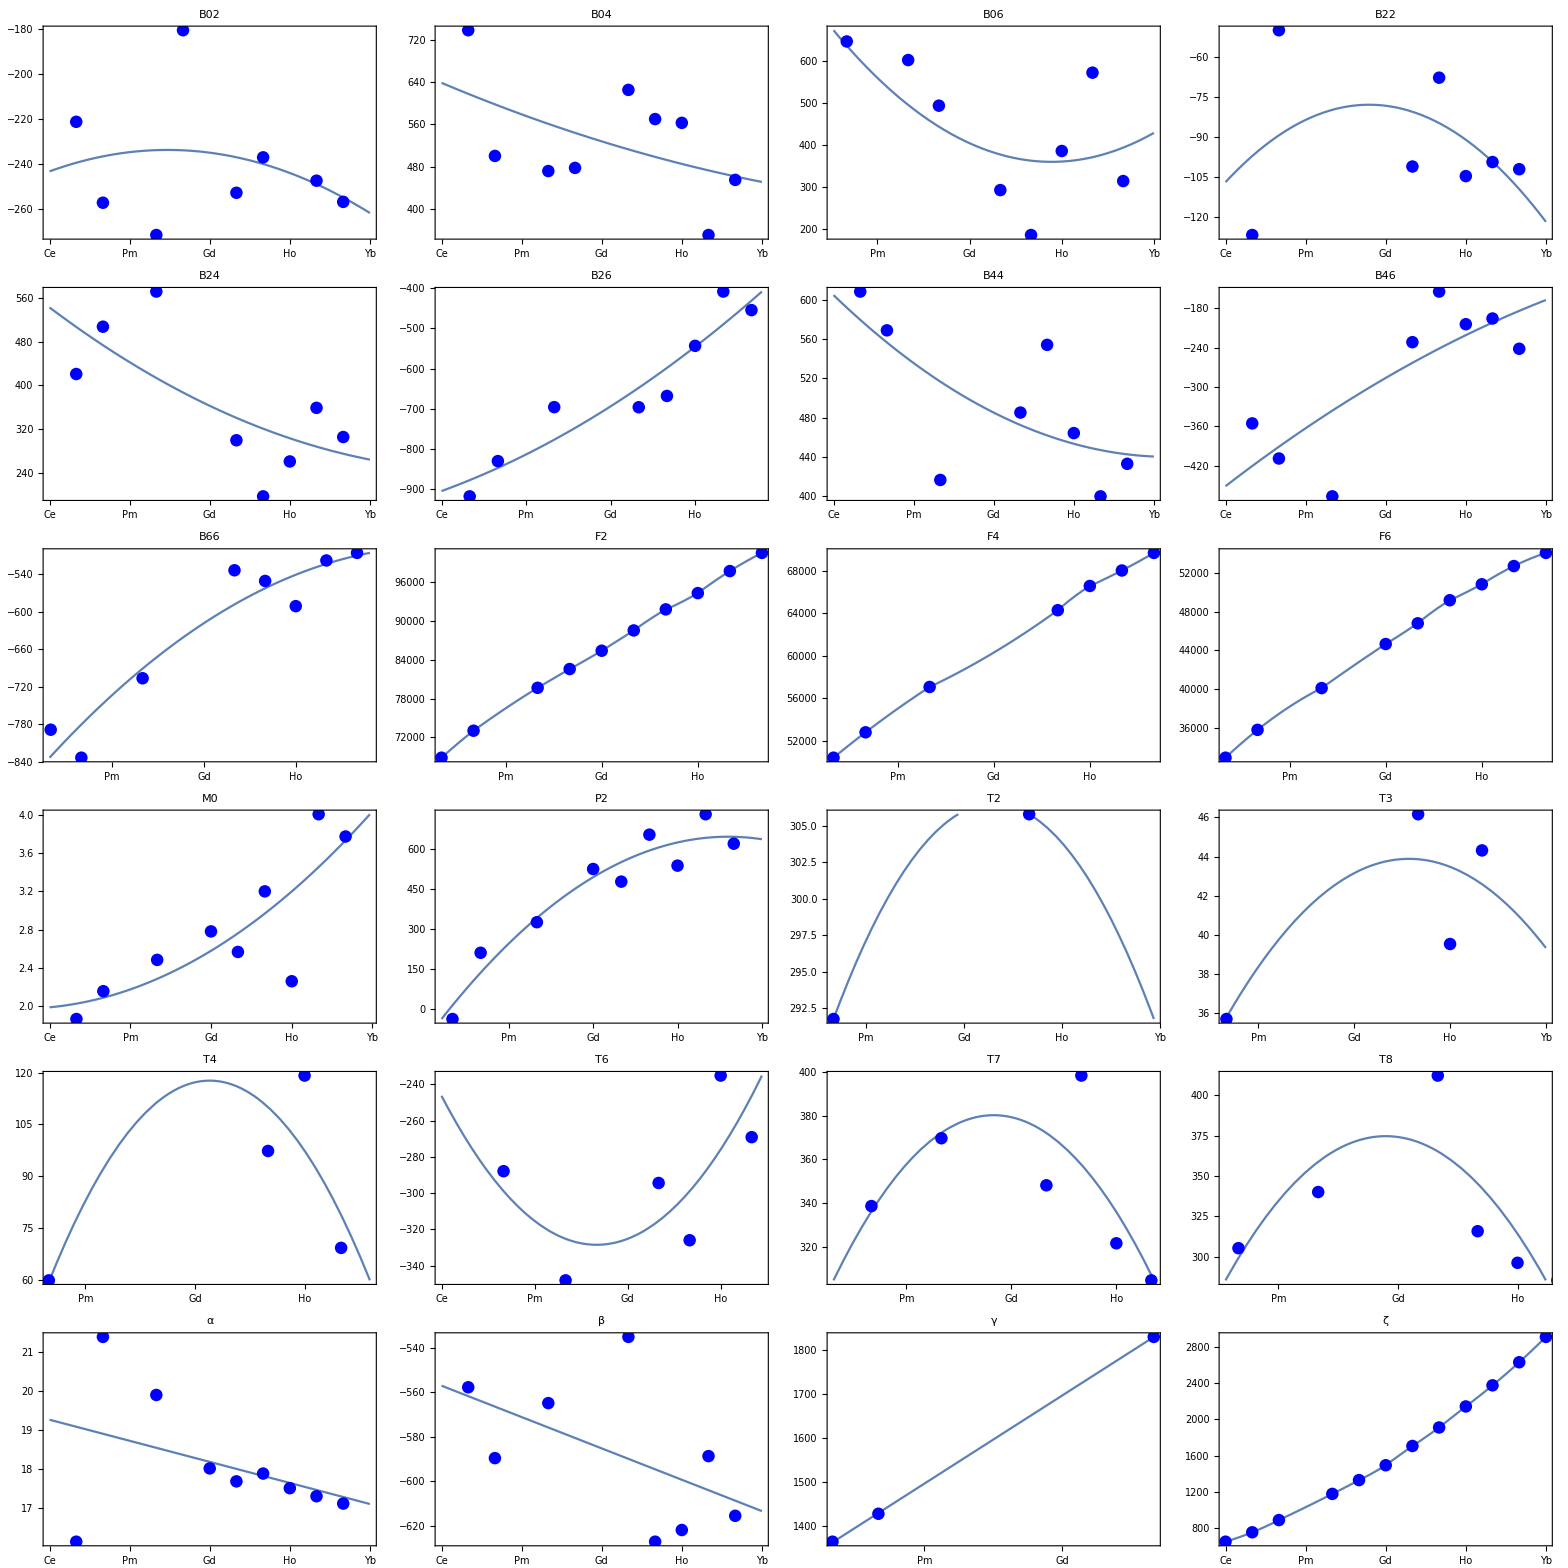

```mathematica
Grid@Partition[paramGraphs,UpTo[4]]
```

```mathematica
currentBest={47,16,13,"----",13,17,10,9,11,9,14,11,33};
billsσ={51,16,14,0,13,16,10,12,12,10,19,10,38};
summary={theLanthanides[[#[[1]]]],If[MissingQ[#[[2]]],"-----",Round[#[[2]],1]]}&/@SortBy[Normal[#["bestRMSwithFullDiagonalization"]&/@truncatedSols],First];
summary=Transpose@Append[Append[Transpose[summary],currentBest],billsσ];
summary=(Append[#,Which[
Head[#[[2]]]===String,
#[[2]],
#[[2]]<=#[[4]],
"😊",
True,
"🤮"]]&/@summary);
summary=(Append[#,Which[
Head[#[[2]]]===String,
#[[2]],
#[[3]]<=#[[4]],
"😊",
True,
"🤮"]]&/@summary);
summary=#[[{1,2,5,3,6,4}]]&/@summary;
TableForm[summary,TableAlignments->Center,TableHeadings->{None,{"","NOW","NOW<=BILL","BEFORE","BEFORE<=BILL","BILL"}}]
```

| NOW | NOW<=BILL | BEFORE | BEFORE<=BILL | BILL
Ce | 43 | 😊 | 47 | 😊 | 51
Pr | 16 | 😊 | 16 | 😊 | 16
Nd | 13 | 😊 | 13 | 😊 | 14
Pm | 0 | 😊 | ---- | Which[----≤0,😊,True,🤮] | 0
Sm | 13 | 😊 | 13 | 😊 | 13
Eu | 16 | 😊 | 17 | 🤮 | 16
Gd | 10 | 😊 | 10 | 😊 | 10
Tb | 8 | 😊 | 9 | 😊 | 12
Dy | 11 | 😊 | 11 | 😊 | 12
Ho | 9 | 😊 | 9 | 😊 | 10
Er | 18 | 😊 | 14 | 😊 | 19
Tm | 13 | 🤮 | 11 | 🤮 | 10
Yb | 53 | 🤮 | 33 | 😊 | 38

```mathematica
(*PrintAndDefine[message_]:=(
progressMessage=ToString[ln]<>": "<>message;
Print[message];
)
Off[N::preclg];
withSpinSin=1;
restart=False;
saveEigenvectors=False;
filePrefix=If[withSpinSin==1,
"pathfinder-constraints-with-spinspin-and-no-truncation",
"pathfinder-constraints-with-spinspin-and-no-truncation"
];
σexp=1.0;
trunEnergy=Infinity;
fitOrder = Position[theLanthanides,#][[1,1]]&/@{"Pr","Nd","Dy","Ce","Sm","Ho","Er","Tm","Yb","Tb","Eu","Gd","Pm"};
doThese=fitOrder;
(*doThese={2,3,9};*)
(*doThese=fitOrder[[;;2]];*)
(*doThese={2};*)
If[Not[restart],
varModel=AssociationThread[{B02,B04,B06,B22,B24,B26,B44,B46,B66,F2,F4,F6,M0,P2,T2,T3,T4,T6,T7,T8,α,β,γ,ζ},ConstantArray[<|"data"->{},"function"->Null|>,24]];
truncatedSols=<||>;
];
Do[
(
numE=numE0;
ln=theLanthanides[[numE]];
Print[ln];
If[ln=="Pm",
(
pmSol=<||>;
pmSol["hamDim"]=Binomial[14,4];
pmSol["numE"]=4;
pmSol["problemVars"]=variedSymbols["Nd"];
pmSol["bestParamsWithConstraints"]=<||>;
pmSol["bestRMS"]=0;
pmSol["bestRMSwithTruncation"]=0;
pmSol["fittedLevels"]=0;
pmSol["solWithUncertainty"]={};
Do[
(
bestP=varModel[pVar]["function"][4];
pmSol["bestParamsWithConstraints"][pVar]=bestP;
),
{pVar,variedSymbols["Nd"]}];
pmSol["bestParamsWithConstraints"][ϵ]=0;
constrainedMsandPs=("MagneticSimplifier"/.Options[ClassicalFit])/.pmSol["bestParamsWithConstraints"];
pmSol["bestParamsWithConstraints"]=Join[pmSol["bestParamsWithConstraints"],Association@constrainedMsandPs];

pmSol["bestParams"]=Normal@pmSol["bestParamsWithConstraints"];
pmSol["bestRMSwithFullDiagonalization"]=0;
pmSol["constraints"]={};
LogSol[pmSol,filePrefix<>"/"<>"Pm"<>"-"<>ToString[trunEnergy]];
truncatedSols[4]=pmSol;
Continue[];
)
];
pVars=variedSymbols[ln];
constraints=Association@caseConstraints[ln];
fixedConstraints=Keys@Select[constraints,NumericQ];
Do[
(
constraints[fixedCon]=varModel[fixedCon]["function"][numE];
)
,
{fixedCon,fixedConstraints}
];
constraints=Normal[constraints];
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=If[OddQ[numE],
Flatten[Position[Flatten[{#,#}&/@(Last/@Carnall[carnalKey]),1],"not included"]],
Flatten[Position[Last/@Carnall[carnalKey],"not included"]]
];
independentVars=Variables[pVars/.constraints];
startValues=AssociationThread[independentVars,independentVars/.LoadLaF3Parameters[ln]];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
pVars,
startValues,
constraints,
"SaveEigenvectors"->saveEigenvectors,
"AddConstantShift"->True,
"SignatureCheck"->False,
"Energy Uncertainty in K"->σexp,
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->withSpinSin)),
"MaxIterations"->1000,
"SaveToLog"->False,
"MaxHistory"->1000,
"FilePrefix"->filePrefix<>"/"<>ln<>"-"<>ToString[trunEnergy],
"TruncationEnergy"->trunEnergy,
"PrintFun"->PrintAndDefine];
sol["bestParams"]=Append[sol["bestParams"],(nE->numE)];
sol["bestParamsWithConstraints"][nE]=numE;
If[(2<=numE<=12),
(constrainedMsandPs=("MagneticSimplifier"/.Options[ClassicalFit])/.sol["bestParamsWithConstraints"];
sol["bestParamsWithConstraints"]=Join[sol["bestParamsWithConstraints"],Association@constrainedMsandPs];
)
];

Print[">> Computing energies with full diagonalization ..."];
params=sol["bestParamsWithConstraints"];
{eigenEnergies,ln,simplerStateLabels,eigensys,basis,truncatedStates}=FastIonSolver[params,
"MakeNotebook"->False,
"PrintFun"->Print,
"Append to Filename"->"fitting-"<>ln,
"Remove Kramers"->False,
"Energy Uncertainty in K"->σexp,
"Explorer"->False
];

Print[">> Calculating full diagonalization RMS ..."];
fullDiffs=(eigenEnergies[[;;Length[expData]]]-First/@expData)[[Complement[presentDataIndices,excludedDataIndices]]];
fullRMSsquared=Sqrt[Total[fullDiffs^2]/sol["degreesOfFreedom"]];
sol["bestRMSwithTruncation"]=sol["bestRMS"];
sol["energiesWithTruncation"]=sol["energies"];
sol["excludedDataIndices"]=excludedDataIndices;
sol["bestRMSwithFullDiagonalization"]=fullRMSsquared;
sol["energiesWithFullDiagonalization"] = eigenEnergies;
sol=KeyDrop[sol,{"bestRMS","energies"}];
truncatedSols[numE0]=sol;
LogSol[sol,filePrefix<>"/"<>ln<>"-"<>ToString[trunEnergy]];

Print["Updating param interpolation functions ..."];
bestParams=Association@sol["bestParams"];
Do[
(
If[Not[MemberQ[Keys[bestParams],pVar]],
Continue[];
];
varModel[pVar]["data"]=DeleteDuplicates@Append[varModel[pVar]["data"],{numE,bestParams[pVar]}];
numData=Length[varModel[pVar]["data"]];
If[numData>0,
(
order=Which[
numData==1,
0,
numData==2,
1,
True,
2];
varModel[pVar]["function"]=Which[
MemberQ[Join[cfSymbols,TSymbols,pseudoMagneticSymbols,marvinSymbols],pVar],
NonlinearModelFit[varModel[pVar]["data"],a0+a1 x+a2 x^2,{a0,a1,a2},x],
MemberQ[casimirSymbols,pVar],
NonlinearModelFit[varModel[pVar]["data"],a0+a1 x,{a0,a1},x],
True,
Interpolation[varModel[pVar]["data"],InterpolationOrder->order]
]
)
];
),
{pVar,pVars}
];
Run["~/Scripts/pushover \"finished fitting "<>ln<>"\""];
),
{numE0, doThese}];*)
```

## C2v (all Ln) pathfinder approach with full diagonalization after fitting --- Automatic Truncation Energy --- Adding a constant shift. Using Carnall1989 as starting values. Using spin-spin. Including Ce and Yb.

### Calculations

```mathematica
(* NOTE: The option "Overwrite" set to False on the SimplerSymbolicHamMatrix can be use to reload previously calculated arrays. Set this to False if they have already been calculated, and set it to True if calculating them from scratch or wanting to recalculate them.*)
{symGroup,symmetrySimplifier}={"C2v",
{B12->0,B14->0,B16->0,B34->0,B36->0,B56->0,
S12->0,S14->0,S16->0,S22->0,S24->0,S26->0,S34->0,S36->0,
S44->0,S46->0,S56->0,S66->0,T11p->0,T11->0,T12->0,T14->0,T15->0,
T16->0,T18->0,T17->0,T19->0}};
Do[
(
symbolicHamiltonians[{symGroup,numE}]=SimplerSymbolicHamMatrix[numE,
symmetrySimplifier,
"PrependToFilename"->symGroup<>"-",
"Overwrite"->False];
),
{numE,{1,2,3,4,5,6,7}}];
```

```mathematica
PrintAndDefine[message_]:=(
progressMessage=ToString[ln]<>": "<>message;
Print[message];
)
Off[N::preclg];
withSpinSin=1;
restart=False;
saveEigenvectors=False;
filePrefix=If[withSpinSin==1,
"pathfinder-constraints-with-spinspin-and-automatic-truncation",
"pathfinder-constraints-with-spinspin-and-automatic-truncation"
];
σexp=1.0;
trunEnergy=Automatic;
fitOrder = Position[theLanthanides,#][[1,1]]&/@{"Pr","Nd","Dy","Ce","Sm","Ho","Er","Tm","Yb","Tb","Eu","Gd","Pm"};
doThese=fitOrder;
(*doThese={2,3,9};*)
(*doThese=fitOrder[[;;2]];*)
If[Not[restart],
varModel=AssociationThread[{B02,B04,B06,B22,B24,B26,B44,B46,B66,F2,F4,F6,M0,P2,T2,T3,T4,T6,T7,T8,α,β,γ,ζ},ConstantArray[<|"data"->{},"function"->Null|>,24]];
truncatedSols=<||>;
];
Do[
(
numE=numE0;
ln=theLanthanides[[numE]];
Print[ln];
If[ln=="Pm",
(
pmSol=<||>;
pmSol["hamDim"]=Binomial[14,4];
pmSol["numE"]=4;
pmSol["problemVars"]=variedSymbols["Nd"];
pmSol["bestParamsWithConstraints"]=<||>;
pmSol["bestRMS"]=0;
pmSol["fittedLevels"]=0;
pmSol["solWithUncertainty"]={};
Do[
(
bestP=varModel[pVar]["function"][4];
pmSol["bestParamsWithConstraints"][pVar]=bestP;
),
{pVar,variedSymbols["Nd"]}];
pmSol["bestParamsWithConstraints"][ϵ]=0;
constrainedMsandPs=("MagneticSimplifier"/.Options[ClassicalFit])/.pmSol["bestParamsWithConstraints"];
pmSol["bestParamsWithConstraints"]=Join[pmSol["bestParamsWithConstraints"],Association@constrainedMsandPs];
pmSol["bestParams"]=Normal@pmSol["bestParamsWithConstraints"];

LogSol[pmSol,filePrefix<>"/"<>"Pm"<>"-"<>ToString[trunEnergy]];
truncatedSols[4]=pmSol;
Continue[];
)
];
pVars=variedSymbols[ln];
constraints=Association@caseConstraints[ln];
fixedConstraints=Keys@Select[constraints,NumericQ];
Do[
(
constraints[fixedCon]=varModel[fixedCon]["function"][numE];
)
,
{fixedCon,fixedConstraints}
];
constraints=Normal[constraints];
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=If[OddQ[numE],
Flatten[Position[Flatten[{#,#}&/@(Last/@Carnall[carnalKey]),1],"not included"]],
Flatten[Position[Last/@Carnall[carnalKey],"not included"]]
];
independentVars=Variables[pVars/.constraints];
startValues=AssociationThread[independentVars,independentVars/.LoadLaF3Parameters[ln]];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
pVars,
startValues,
constraints,
"SaveEigenvectors"->saveEigenvectors,
"AddConstantShift"->True,
"SignatureCheck"->False,
"Energy Uncertainty in K"->σexp,
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->withSpinSin)),
"MaxIterations"->1000,
"SaveToLog"->False,
"MaxHistory"->1000,
"FilePrefix"->filePrefix<>"/"<>ln<>"-"<>ToString[trunEnergy],
"TruncationEnergy"->trunEnergy,
"PrintFun"->PrintAndDefine];
sol["bestParams"]=Append[sol["bestParams"],(nE->numE)];
sol["bestParamsWithConstraints"][nE]=numE;
If[(2<=numE<=12),
(constrainedMsandPs=("MagneticSimplifier"/.Options[ClassicalFit])/.sol["bestParamsWithConstraints"];
sol["bestParamsWithConstraints"]=Join[sol["bestParamsWithConstraints"],Association@constrainedMsandPs];
)
];

Print[">> Computing energies with full diagonalization ..."];
params=sol["bestParamsWithConstraints"];
{eigenEnergies,ln,simplerStateLabels,eigensys,basis,truncatedStates}=FastIonSolver[params,
"MakeNotebook"->False,
"PrintFun"->Print,
"Append to Filename"->"fitting-"<>ln,
"Remove Kramers"->False,
"Energy Uncertainty in K"->σexp,
"Explorer"->False
];

Print[">> Calculating full diagonalization RMS ..."];
fullDiffs=(eigenEnergies[[;;Length[expData]]]-First/@expData)[[Complement[presentDataIndices,excludedDataIndices]]];
fullRMSsquared=Sqrt[Total[fullDiffs^2]/sol["degreesOfFreedom"]];
sol["bestRMSwithTruncation"]=sol["bestRMS"];
sol["energiesWithTruncation"]=sol["energies"];
sol["excludedDataIndices"]=excludedDataIndices;
sol["bestRMSwithFullDiagonalization"]=fullRMSsquared;
sol["energiesWithFullDiagonalization"] = eigenEnergies;
sol=KeyDrop[sol,{"bestRMS","energies"}];
truncatedSols[numE0]=sol;
LogSol[sol,filePrefix<>"/"<>ln<>"-"<>ToString[trunEnergy]];

Print["Updating param interpolation functions ..."];
bestParams=Association@sol["bestParams"];
Do[
(
If[Not[MemberQ[Keys[bestParams],pVar]],
Continue[];
];
varModel[pVar]["data"]=DeleteDuplicates@Append[varModel[pVar]["data"],{numE,bestParams[pVar]}];
numData=Length[varModel[pVar]["data"]];
If[numData>0,
(
order=Which[
numData==1,
0,
numData==2,
1,
True,
2];
varModel[pVar]["function"]=Which[
MemberQ[Join[cfSymbols,TSymbols,pseudoMagneticSymbols,marvinSymbols],pVar],
NonlinearModelFit[varModel[pVar]["data"],a0+a1 x+a2 x^2,{a0,a1,a2},x],
MemberQ[casimirSymbols,pVar],
NonlinearModelFit[varModel[pVar]["data"],a0+a1 x,{a0,a1},x],
True,
Interpolation[varModel[pVar]["data"],InterpolationOrder->order]
]
)
];
),
{pVar,pVars}
];
Run["~/Scripts/pushover \"finished fitting "<>ln<>"\""];
),
{numE0, doThese}];
```

Pr

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Finished ...

>> Computing energies with full diagonalization ...

> Calculating simpler term labels ...

> Loading the symbolic Hamiltonian for this configuration ...

>> Loading the symbolic Hamiltonian took 0.000057 seconds.

> params does not implicitly specify if the spin-spin contribution should be included. Including it by default ...

<|E0→0,E1→0,E2→0,E3→0,ζ→749.807,F0→0,F2→68868.2,F4→50405.4,F6→32887.2,M0→1.86782,M2→1.04598,M4→0.579025,σSS→1,T2→0,T2p→0,T3→0,T4→0,T6→0,T7→0,T8→0,T11→0,T11p→0,T12→0,T14→0,T15→0,T16→0,T17→0,T18→0,T19→0,P0→0,P2→-38.8029,P4→-19.4014,P6→-3.88029,gs→0,α→16.1474,β→-557.702,γ→1364.08,B02→-221.216,B04→737.938,B06→672.996,B12→0,B14→0,B16→0,B22→-126.739,B24→420.805,B26→-918.663,B34→0,B36→0,B44→608.423,B46→-355.425,B56→0,B66→-788.801,S12→0,S14→0,S16→0,S22→0,S24→0,S26→0,S34→0,S36→0,S44→0,S46→0,S56→0,S66→0,ϵ→-2.11223,t2Switch→1,wChErrA→0,wChErrB→0,Bx→0,By→0,Bz→0,Ω2→0,Ω4→0,Ω6→0,nE→2|>

> Calculating the SLJ basis ...

> Diagonalizing the numerical Hamiltonian ...

>> Diagonalization took 0.001642 seconds.

>> Truncating eigenvectors to given probability ...

>>> Truncation took 0.015327 seconds.

>> Calculating full diagonalization RMS ...

Saving solution to: ./log/pathfinder-constraints-with-spinspin-and-automatic-truncation/Pr-Automatic-sols-13353003-62df-4b34-af6c-f919060a2081.m

Updating param interpolation functions ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Finished ...

>> Computing energies with full diagonalization ...

> Calculating simpler term labels ...

> Loading the symbolic Hamiltonian for this configuration ...

>> Loading the symbolic Hamiltonian took 0.000064 seconds.

> params does not implicitly specify if the spin-spin contribution should be included. Including it by default ...

<|E0→0,E1→0,E2→0,E3→0,ζ→885.133,F0→0,F2→73028.7,F4→52776.3,F6→35757.4,M0→2.15985,M2→1.20951,M4→0.669552,σSS→1,T2→293.292,T2p→0,T3→35.7242,T4→59.8811,T6→-288.203,T7→339.324,T8→305.232,T11→0,T11p→0,T12→0,T14→0,T15→0,T16→0,T17→0,T18→0,T19→0,P0→0,P2→211.293,P4→105.646,P6→21.1293,gs→0,α→21.3669,β→-589.276,γ→1431.33,B02→-255.761,B04→501.913,B06→646.767,B12→0,B14→0,B16→0,B22→-50.9973,B24→504.709,B26→-832.339,B34→0,B36→0,B44→571.221,B46→-408.718,B56→0,B66→-832.194,S12→0,S14→0,S16→0,S22→0,S24→0,S26→0,S34→0,S36→0,S44→0,S46→0,S56→0,S66→0,ϵ→-4.75331,t2Switch→1,wChErrA→0,wChErrB→0,Bx→0,By→0,Bz→0,Ω2→0,Ω4→0,Ω6→0,nE→3|>

> Calculating the SLJ basis ...

> Diagonalizing the numerical Hamiltonian ...

>> Diagonalization took 0.05594 seconds.

>> Truncating eigenvectors to given probability ...

>>> Truncation took 0.109552 seconds.

>> Calculating full diagonalization RMS ...

Saving solution to: ./log/pathfinder-constraints-with-spinspin-and-automatic-truncation/Nd-Automatic-sols-c4bebb25-28e9-4c49-bc7a-f177b4b92b46.m

Updating param interpolation functions ...

Dy

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindMinimum::sszero will be suppressed during this calculation.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Finished ...

>> Computing energies with full diagonalization ...

> Calculating simpler term labels ...

> Conjugating the parameters accounting for the hole-particle equivalence ...

> Loading the symbolic Hamiltonian for this configuration ...

>> Loading the symbolic Hamiltonian took 0.000093 seconds.

> params does not implicitly specify if the spin-spin contribution should be included. Including it by default ...

<|E0→0,E1→0,E2→0,E3→0,ζ→-1908.57,F0→0,F2→91833.1,F4→64359.6,F6→49262.1,M0→3.22098,M2→1.80375,M4→0.998502,σSS→1,T2→-315.374,T2p→0,T3→-33.0832,T4→-94.2278,T6→298.093,T7→-374.058,T8→-325.331,T11→0,T11p→0,T12→0,T14→0,T15→0,T16→0,T17→0,T18→0,T19→0,P0→0,P2→627.907,P4→313.954,P6→62.7907,gs→0,α→18.2818,β→-638.868,γ→1802.4,B02→239.25,B04→-560.065,B06→-176.569,B12→0,B14→0,B16→0,B22→67.6276,B24→-192.741,B26→674.689,B34→0,B36→0,B44→-553.608,B46→155.054,B56→0,B66→545.562,S12→0,S14→0,S16→0,S22→0,S24→0,S26→0,S34→0,S36→0,S44→0,S46→0,S56→0,S66→0,ϵ→-6.67685,t2Switch→0,wChErrA→0,wChErrB→0,Bx→0,By→0,Bz→0,Ω2→0,Ω4→0,Ω6→0,nE→9|>

> Calculating the SLJ basis ...

> Diagonalizing the numerical Hamiltonian ...

Eigensystem::arh: Because finding 2002 out of the 2002 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

>> Diagonalization took 2.34932 seconds.

>> Truncating eigenvectors to given probability ...

>>> Truncation took 2.12152 seconds.

>> Calculating full diagonalization RMS ...

Saving solution to: ./log/pathfinder-constraints-with-spinspin-and-automatic-truncation/Dy-Automatic-sols-6035f2de-f01d-498c-8984-23d2d1fee917.m

Updating param interpolation functions ...

Ce

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Finished ...

>> Computing energies with full diagonalization ...

> Calculating simpler term labels ...

> Loading the symbolic Hamiltonian for this configuration ...

>> Loading the symbolic Hamiltonian took 0.000058 seconds.

> params does not implicitly specify if the spin-spin contribution should be included. Including it by default ...

<|E0→0,E1→0,E2→0,E3→0,ζ→645.612,F0→0,F2→0,F4→0,F6→0,M0→0,M2→0,M4→0,σSS→1,T2→0,T2p→0,T3→0,T4→0,T6→0,T7→0,T8→0,T11→0,T11p→0,T12→0,T14→0,T15→0,T16→0,T17→0,T18→0,T19→0,P0→0,P2→0,P4→0,P6→0,gs→0,α→0,β→0,γ→0,B02→-176.015,B04→1044.17,B06→684.329,B12→0,B14→0,B16→0,B22→-224.912,B24→298.073,B26→-1022.14,B34→0,B36→0,B44→655.415,B46→-274.826,B56→0,B66→-719.36,S12→0,S14→0,S16→0,S22→0,S24→0,S26→0,S34→0,S36→0,S44→0,S46→0,S56→0,S66→0,ϵ→-30.7365,t2Switch→1,wChErrA→0,wChErrB→0,Bx→0,By→0,Bz→0,Ω2→0,Ω4→0,Ω6→0,nE→1|>

> Calculating the SLJ basis ...

> Diagonalizing the numerical Hamiltonian ...

>> Diagonalization took 0.000174 seconds.

>> Truncating eigenvectors to given probability ...

>>> Truncation took 0.001646 seconds.

>> Calculating full diagonalization RMS ...

Saving solution to: ./log/pathfinder-constraints-with-spinspin-and-automatic-truncation/Ce-Automatic-sols-2456ea2b-c60e-469d-ac4a-cc997135e14f.m

Updating param interpolation functions ...

Sm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Finished ...

>> Computing energies with full diagonalization ...

> Calculating simpler term labels ...

> Loading the symbolic Hamiltonian for this configuration ...

>> Loading the symbolic Hamiltonian took 0.000089 seconds.

> params does not implicitly specify if the spin-spin contribution should be included. Including it by default ...

<|E0→0,E1→0,E2→0,E3→0,ζ→1174.86,F0→0,F2→79649.4,F4→57075.8,F6→40105.2,M0→2.47956,M2→1.38856,M4→0.768665,σSS→1,T2→304.933,T2p→0,T3→35.7843,T4→69.8575,T6→-341.334,T7→369.982,T8→340.909,T11→0,T11p→0,T12→0,T14→0,T15→0,T16→0,T17→0,T18→0,T19→0,P0→0,P2→328.145,P4→164.072,P6→32.8145,gs→0,α→20.0042,β→-564.916,γ→1553.39,B02→-272.305,B04→464.334,B06→618.163,B12→0,B14→0,B16→0,B22→33.1886,B24→572.679,B26→-701.631,B34→0,B36→0,B44→426.975,B46→-465.083,B56→0,B66→-711.424,S12→0,S14→0,S16→0,S22→0,S24→0,S26→0,S34→0,S36→0,S44→0,S46→0,S56→0,S66→0,ϵ→-21.981,t2Switch→1,wChErrA→0,wChErrB→0,Bx→0,By→0,Bz→0,Ω2→0,Ω4→0,Ω6→0,nE→5|>

> Calculating the SLJ basis ...

> Diagonalizing the numerical Hamiltonian ...

Eigensystem::arh: Because finding 2002 out of the 2002 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

>> Diagonalization took 2.36941 seconds.

>> Truncating eigenvectors to given probability ...

>>> Truncation took 2.19943 seconds.

>> Calculating full diagonalization RMS ...

Saving solution to: ./log/pathfinder-constraints-with-spinspin-and-automatic-truncation/Sm-Automatic-sols-9855a80b-7a7a-4b2a-9d0f-0d7cee72b36d.m

Updating param interpolation functions ...

Ho

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Finished ...

>> Computing energies with full diagonalization ...

> Calculating simpler term labels ...

> Conjugating the parameters accounting for the hole-particle equivalence ...

> Loading the symbolic Hamiltonian for this configuration ...

>> Loading the symbolic Hamiltonian took 0.000064 seconds.

> params does not implicitly specify if the spin-spin contribution should be included. Including it by default ...

<|E0→0,E1→0,E2→0,E3→0,ζ→-2140.57,F0→0,F2→94346.4,F4→66709.7,F6→50914.6,M0→2.41862,M2→1.35442,M4→0.749771,σSS→1,T2→-315.31,T2p→0,T3→-37.6799,T4→-104.267,T6→243.128,T7→-282.382,T8→-296.42,T11→0,T11p→0,T12→0,T14→0,T15→0,T16→0,T17→0,T18→0,T19→0,P0→0,P2→524.992,P4→262.496,P6→52.4992,gs→0,α→17.9587,β→-623.918,γ→1865.13,B02→210.973,B04→-571.41,B06→-390.411,B12→0,B14→0,B16→0,B22→106.865,B24→-255.966,B26→551.291,B34→0,B36→0,B44→-473.533,B46→208.356,B56→0,B66→590.962,S12→0,S14→0,S16→0,S22→0,S24→0,S26→0,S34→0,S36→0,S44→0,S46→0,S56→0,S66→0,ϵ→-5.65019,t2Switch→0,wChErrA→0,wChErrB→0,Bx→0,By→0,Bz→0,Ω2→0,Ω4→0,Ω6→0,nE→10|>

> Calculating the SLJ basis ...

> Diagonalizing the numerical Hamiltonian ...

Eigensystem::arh: Because finding 1001 out of the 1001 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

General::stop: Further output of Eigensystem::arh will be suppressed during this calculation.

>> Diagonalization took 0.259125 seconds.

>> Truncating eigenvectors to given probability ...

>>> Truncation took 0.99799 seconds.

>> Calculating full diagonalization RMS ...

Saving solution to: ./log/pathfinder-constraints-with-spinspin-and-automatic-truncation/Ho-Automatic-sols-56d41139-d7f7-44b8-a97b-06092bcca595.m

Updating param interpolation functions ...

Er

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Finished ...

>> Computing energies with full diagonalization ...

> Calculating simpler term labels ...

> Conjugating the parameters accounting for the hole-particle equivalence ...

> Loading the symbolic Hamiltonian for this configuration ...

>> Loading the symbolic Hamiltonian took 0.00006 seconds.

> params does not implicitly specify if the spin-spin contribution should be included. Including it by default ...

<|E0→0,E1→0,E2→0,E3→0,ζ→-2377.94,F0→0,F2→97692.4,F4→68075.7,F6→52933.1,M0→3.93532,M2→2.20378,M4→1.21995,σSS→1,T2→-314.175,T2p→0,T3→-44.5198,T4→-68.12,T6→273.11,T7→-299.373,T8→-303.048,T11→0,T11p→0,T12→0,T14→0,T15→0,T16→0,T17→0,T18→0,T19→0,P0→0,P2→713.78,P4→356.89,P6→71.378,gs→0,α→17.4148,β→-591.584,γ→1927.48,B02→241.803,B04→-380.713,B06→-447.876,B12→0,B14→0,B16→0,B22→90.9874,B24→-354.107,B26→486.919,B34→0,B36→0,B44→-402.615,B46→229.223,B56→0,B66→502.608,S12→0,S14→0,S16→0,S22→0,S24→0,S26→0,S34→0,S36→0,S44→0,S46→0,S56→0,S66→0,ϵ→-9.94259,t2Switch→0,wChErrA→0,wChErrB→0,Bx→0,By→0,Bz→0,Ω2→0,Ω4→0,Ω6→0,nE→11|>

> Calculating the SLJ basis ...

> Diagonalizing the numerical Hamiltonian ...

>> Diagonalization took 0.055333 seconds.

>> Truncating eigenvectors to given probability ...

>>> Truncation took 0.108204 seconds.

>> Calculating full diagonalization RMS ...

Saving solution to: ./log/pathfinder-constraints-with-spinspin-and-automatic-truncation/Er-Automatic-sols-d4842a02-379b-47d2-bdd6-66ee34d2b2ff.m

Updating param interpolation functions ...

Tm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Finished ...

>> Computing energies with full diagonalization ...

> Calculating simpler term labels ...

> Conjugating the parameters accounting for the hole-particle equivalence ...

> Loading the symbolic Hamiltonian for this configuration ...

>> Loading the symbolic Hamiltonian took 0.000061 seconds.

> params does not implicitly specify if the spin-spin contribution should be included. Including it by default ...

<|E0→0,E1→0,E2→0,E3→0,ζ→-2633.98,F0→0,F2→100471.,F4→69699.2,F6→54402.3,M0→3.79956,M2→2.12775,M4→1.17786,σSS→1,T2→-311.97,T2p→0,T3→0,T4→0,T6→0,T7→0,T8→0,T11→0,T11p→0,T12→0,T14→0,T15→0,T16→0,T17→0,T18→0,T19→0,P0→0,P2→630.888,P4→315.444,P6→63.0888,gs→0,α→17.0783,β→-614.739,γ→1989.82,B02→256.2,B04→-454.962,B06→-312.4,B12→0,B14→0,B16→0,B22→102.281,B24→-305.385,B26→455.279,B34→0,B36→0,B44→-433.286,B46→241.692,B56→0,B66→504.603,S12→0,S14→0,S16→0,S22→0,S24→0,S26→0,S34→0,S36→0,S44→0,S46→0,S56→0,S66→0,ϵ→-11.4244,t2Switch→0,wChErrA→0,wChErrB→0,Bx→0,By→0,Bz→0,Ω2→0,Ω4→0,Ω6→0,nE→12|>

> Calculating the SLJ basis ...

> Diagonalizing the numerical Hamiltonian ...

>> Diagonalization took 0.004724 seconds.

>> Truncating eigenvectors to given probability ...

>>> Truncation took 0.014519 seconds.

>> Calculating full diagonalization RMS ...

Saving solution to: ./log/pathfinder-constraints-with-spinspin-and-automatic-truncation/Tm-Automatic-sols-95b107b2-64e8-4d6d-b781-9b11eb39feb3.m

Updating param interpolation functions ...

Yb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Finished ...

>> Computing energies with full diagonalization ...

> Calculating simpler term labels ...

> Conjugating the parameters accounting for the hole-particle equivalence ...

> Loading the symbolic Hamiltonian for this configuration ...

>> Loading the symbolic Hamiltonian took 0.000064 seconds.

> params does not implicitly specify if the spin-spin contribution should be included. Including it by default ...

<|E0→0,E1→0,E2→0,E3→0,ζ→-2915.15,F0→0,F2→0,F4→0,F6→0,M0→0,M2→0,M4→0,σSS→1,T2→0,T2p→0,T3→0,T4→0,T6→0,T7→0,T8→0,T11→0,T11p→0,T12→0,T14→0,T15→0,T16→0,T17→0,T18→0,T19→0,P0→0,P2→0,P4→0,P6→0,gs→0,α→0,β→0,γ→0,B02→234.479,B04→-483.916,B06→-354.892,B12→0,B14→0,B16→0,B22→134.729,B24→-243.686,B26→424.081,B34→0,B36→0,B44→-443.063,B46→169.57,B56→0,B66→466.884,S12→0,S14→0,S16→0,S22→0,S24→0,S26→0,S34→0,S36→0,S44→0,S46→0,S56→0,S66→0,ϵ→-23.8223,t2Switch→0,wChErrA→0,wChErrB→0,Bx→0,By→0,Bz→0,Ω2→0,Ω4→0,Ω6→0,nE→13|>

> Calculating the SLJ basis ...

> Diagonalizing the numerical Hamiltonian ...

>> Diagonalization took 0.000218 seconds.

>> Truncating eigenvectors to given probability ...

>>> Truncation took 0.001297 seconds.

>> Calculating full diagonalization RMS ...

Saving solution to: ./log/pathfinder-constraints-with-spinspin-and-automatic-truncation/Yb-Automatic-sols-c4590b15-18ec-49e6-8148-87dc9cb1df42.m

Updating param interpolation functions ...

Tb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Finished ...

>> Computing energies with full diagonalization ...

> Calculating simpler term labels ...

> Conjugating the parameters accounting for the hole-particle equivalence ...

> Loading the symbolic Hamiltonian for this configuration ...

>> Loading the symbolic Hamiltonian took 0.000062 seconds.

> params does not implicitly specify if the spin-spin contribution should be included. Including it by default ...

<|E0→0,E1→0,E2→0,E3→0,ζ→-1705.97,F0→0,F2→88632.3,F4→62663.,F6→46929.9,M0→2.51311,M2→1.40734,M4→0.779063,σSS→1,T2→-314.369,T2p→0,T3→-29.5386,T4→-108.244,T6→349.83,T7→-344.949,T8→-389.769,T11→0,T11p→0,T12→0,T14→0,T15→0,T16→0,T17→0,T18→0,T19→0,P0→0,P2→457.976,P4→228.988,P6→45.7976,gs→0,α→18.0551,β→-571.545,γ→1740.43,B02→251.398,B04→-635.775,B06→-292.349,B12→0,B14→0,B16→0,B22→104.195,B24→-284.498,B26→710.745,B34→0,B36→0,B44→-497.072,B46→241.398,B56→0,B66→522.912,S12→0,S14→0,S16→0,S22→0,S24→0,S26→0,S34→0,S36→0,S44→0,S46→0,S56→0,S66→0,ϵ→-1.14618,t2Switch→0,wChErrA→0,wChErrB→0,Bx→0,By→0,Bz→0,Ω2→0,Ω4→0,Ω6→0,nE→8|>

> Calculating the SLJ basis ...

> Diagonalizing the numerical Hamiltonian ...

>> Diagonalization took 2.32816 seconds.

>> Truncating eigenvectors to given probability ...

>>> Truncation took 8.18012 seconds.

>> Calculating full diagonalization RMS ...

Saving solution to: ./log/pathfinder-constraints-with-spinspin-and-automatic-truncation/Tb-Automatic-sols-e2ad1052-6cfa-41f1-a871-dc109916630a.m

Updating param interpolation functions ...

Eu

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Finished ...

>> Computing energies with full diagonalization ...

> Calculating simpler term labels ...

> Loading the symbolic Hamiltonian for this configuration ...

>> Loading the symbolic Hamiltonian took 0.000092 seconds.

> params does not implicitly specify if the spin-spin contribution should be included. Including it by default ...

<|E0→0,E1→0,E2→0,E3→0,ζ→1328.93,F0→0,F2→82678.8,F4→58950.,F6→42331.5,M0→2.34892,M2→1.31539,M4→0.728165,σSS→1,T2→309.148,T2p→0,T3→27.366,T4→104.633,T6→-340.672,T7→370.878,T8→361.317,T11→0,T11p→0,T12→0,T14→0,T15→0,T16→0,T17→0,T18→0,T19→0,P0→0,P2→396.883,P4→198.441,P6→39.6883,gs→0,α→18.5305,β→-586.272,γ→1615.74,B02→-178.832,B04→479.72,B06→488.174,B12→0,B14→0,B16→0,B22→-80.2986,B24→380.177,B26→-746.027,B34→0,B36→0,B44→508.782,B46→-313.523,B56→0,B66→-649.508,S12→0,S14→0,S16→0,S22→0,S24→0,S26→0,S34→0,S36→0,S44→0,S46→0,S56→0,S66→0,ϵ→-8.32622,t2Switch→1,wChErrA→0,wChErrB→0,Bx→0,By→0,Bz→0,Ω2→0,Ω4→0,Ω6→0,nE→6|>

> Calculating the SLJ basis ...

> Diagonalizing the numerical Hamiltonian ...

>> Diagonalization took 2.34099 seconds.

>> Truncating eigenvectors to given probability ...

>>> Truncation took 8.76982 seconds.

>> Calculating full diagonalization RMS ...

Saving solution to: ./log/pathfinder-constraints-with-spinspin-and-automatic-truncation/Eu-Automatic-sols-6f0f6f00-717a-455c-b91a-da236c534875.m

Updating param interpolation functions ...

Gd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Finished ...

>> Computing energies with full diagonalization ...

> Calculating simpler term labels ...

> Loading the symbolic Hamiltonian for this configuration ...

>> Loading the symbolic Hamiltonian took 0.000077 seconds.

> params does not implicitly specify if the spin-spin contribution should be included. Including it by default ...

<|E0→0,E1→0,E2→0,E3→0,ζ→1496.24,F0→0,F2→85412.8,F4→60643.1,F6→44714.9,M0→2.86825,M2→1.60622,M4→0.889157,σSS→1,T2→312.293,T2p→0,T3→27.6775,T4→109.08,T6→-338.934,T7→367.535,T8→363.672,T11→0,T11p→0,T12→0,T14→0,T15→0,T16→0,T17→0,T18→0,T19→0,P0→0,P2→555.845,P4→277.923,P6→55.5845,gs→0,α→18.1709,β→-591.47,γ→1678.08,B02→-234.452,B04→529.297,B06→402.398,B12→0,B14→0,B16→0,B22→-80.3286,B24→355.27,B26→-705.812,B34→0,B36→0,B44→494.36,B46→-290.614,B56→0,B66→-614.421,S12→0,S14→0,S16→0,S22→0,S24→0,S26→0,S34→0,S36→0,S44→0,S46→0,S56→0,S66→0,ϵ→-11.8651,t2Switch→1,wChErrA→0,wChErrB→0,Bx→0,By→0,Bz→0,Ω2→0,Ω4→0,Ω6→0,nE→7|>

> Calculating the SLJ basis ...

> Diagonalizing the numerical Hamiltonian ...

>> Diagonalization took 8.07465 seconds.

>> Truncating eigenvectors to given probability ...

>>> Truncation took 5.46141 seconds.

>> Calculating full diagonalization RMS ...

Saving solution to: ./log/pathfinder-constraints-with-spinspin-and-automatic-truncation/Gd-Automatic-sols-ff4dc444-ce04-44ab-8899-2b2189fb156e.m

Updating param interpolation functions ...

Pm

Saving solution to: ./log/pathfinder-constraints-with-spinspin-and-automatic-truncation/Pm-Automatic-sols-15afc242-065a-44d1-9277-7dc0fa9f3626.m

```mathematica
paramGraphs=Table[
Plot[Quiet@varModel[var]["function"][x],
{x,1,13},
Epilog->{Blue,PointSize[0.03],Point[varModel[var]["data"]]},
Frame->True,
FrameTicks->{
{Automatic,Automatic},
{Transpose[{Range[1,13],theLanthanides}],None}
},
PlotLabel->Style[var,15],
AspectRatio->3/4,
ImageSize->300,
FrameStyle->Directive[13],
PlotRange->{All,MinMax[Last/@varModel[var]["data"]]}
],
{var,Keys[varModel]}
];
```

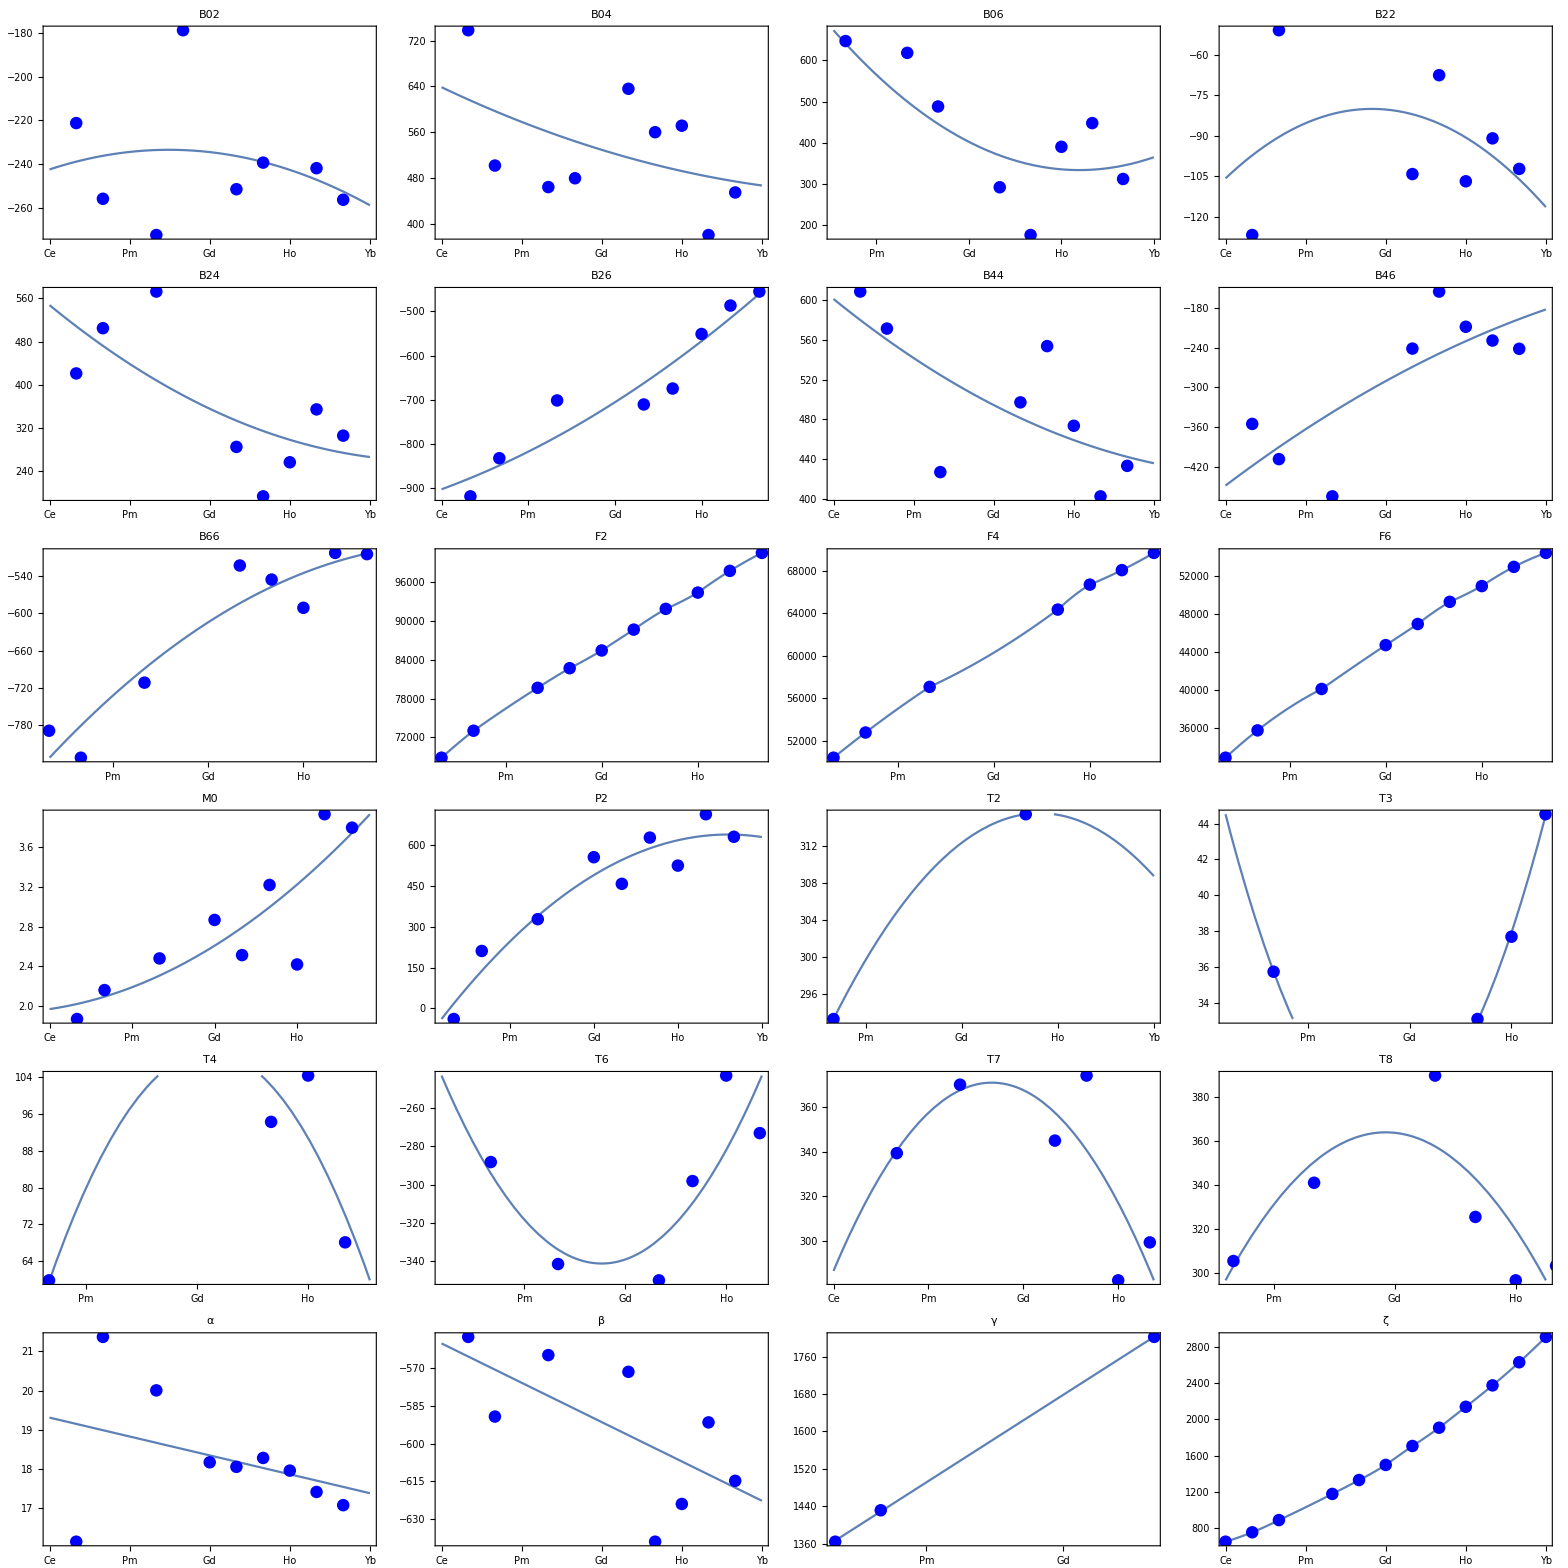

```mathematica
Grid@Partition[paramGraphs,UpTo[4]]
```

```mathematica
currentBest={47,16,13,"----",13,17,10,9,11,9,14,11,33};
billsσ={51,16,14,0,13,16,10,12,12,10,19,10,38};
summary={theLanthanides[[#[[1]]]],If[MissingQ[#[[2]]],"-----",Round[#[[2]],1]]}&/@SortBy[Normal[#["bestRMSwithFullDiagonalization"]&/@truncatedSols],First];
summary=Transpose@Append[Append[Transpose[summary],currentBest],billsσ];
summary=(Append[#,Which[
Head[#[[2]]]===String,
#[[2]],
#[[2]]<=#[[4]],
"😊",
True,
"🤮"]]&/@summary);
summary=(Append[#,Which[
Head[#[[2]]]===String,
#[[2]],
#[[3]]<=#[[4]],
"😊",
True,
"🤮"]]&/@summary);
summary=#[[{1,2,5,3,6,4}]]&/@summary;
TableForm[summary,TableAlignments->Center,TableHeadings->{None,{"","NOW","NOW<=BILL","BEFORE","BEFORE<=BILL","BILL"}}]
```

| NOW | NOW<=BILL | BEFORE | BEFORE<=BILL | BILL
Ce | 49 | 😊 | 47 | 😊 | 51
Pr | 16 | 😊 | 16 | 😊 | 16
Nd | 13 | 😊 | 13 | 😊 | 14
Pm | ----- | ----- | ---- | ----- | 0
Sm | 14 | 🤮 | 13 | 😊 | 13
Eu | 15 | 😊 | 17 | 🤮 | 16
Gd | 9 | 😊 | 10 | 😊 | 10
Tb | 10 | 😊 | 9 | 😊 | 12
Dy | 14 | 🤮 | 11 | 😊 | 12
Ho | 13 | 🤮 | 9 | 😊 | 10
Er | 18 | 😊 | 14 | 😊 | 19
Tm | 13 | 🤮 | 11 | 🤮 | 10
Yb | 49 | 🤮 | 33 | 😊 | 38

## C2v (all Ln) pathfinder approach --- Automatic Truncation Energy --- Adding a constant shift. Using Carnall1989 as starting values. Using spin-spin. Including Ce and Yb.

### Calculations

```mathematica
(* NOTE: The option "Overwrite" set to False on the SimplerSymbolicHamMatrix can be use to reload previously calculated arrays. Set this to False if they have already been calculated, and set it to True if calculating them from scratch or wanting to recalculate them.*)
{symGroup,symmetrySimplifier}={"C2v",
{B12->0,B14->0,B16->0,B34->0,B36->0,B56->0,
S12->0,S14->0,S16->0,S22->0,S24->0,S26->0,S34->0,S36->0,
S44->0,S46->0,S56->0,S66->0,T11p->0,T11->0,T12->0,T14->0,T15->0,
T16->0,T18->0,T17->0,T19->0}};
Do[
(
symbolicHamiltonians[{symGroup,numE}]=SimplerSymbolicHamMatrix[numE,
symmetrySimplifier,
"PrependToFilename"->symGroup<>"-",
"Overwrite"->False];
),
{numE,{1,2,3,4,5,6,7}}];
```

```mathematica
PrintAndDefine[message_]:=(
progressMessage=ToString[ln]<>": "<>message;
Print[message];
)
Off[N::preclg];
withSpinSin=1;
restart=False;
saveEigenvectors=False;
filePrefix=If[withSpinSin==1,
"pathfinder-constraints-with-spinspin-and-automatic-truncation",
"pathfinder-constraints-with-spinspin-and-automatic-truncation"
];
σexp=1.0;
trunEnergy=Automatic;
fitOrder = Position[theLanthanides,#][[1,1]]&/@{"Pr","Nd","Dy","Ce","Sm","Ho","Er","Tm","Yb","Tb","Eu","Gd","Pm"};
doThese=fitOrder;
(*doThese={2,3,9};*)
doThese=fitOrder[[;;1]];
If[Not[restart],
varModel=AssociationThread[{B02,B04,B06,B22,B24,B26,B44,B46,B66,F2,F4,F6,M0,P2,T2,T3,T4,T6,T7,T8,α,β,γ,ζ},ConstantArray[<|"data"->{},"function"->Null|>,24]];
truncatedSols=<||>;
];
Do[
(
numE=numE0;
ln=theLanthanides[[numE]];
Print[ln];
If[ln=="Pm",
(
pmSol=<||>;
pmSol["hamDim"]=Binomial[14,4];
pmSol["numE"]=4;
pmSol["problemVars"]=variedSymbols["Nd"];
pmSol["bestParamsWithConstraints"]=<||>;
pmSol["bestRMS"]=0;
pmSol["fittedLevels"]=0;
pmSol["solWithUncertainty"]={};
Do[
(
bestP=varModel[pVar]["function"][4];
pmSol["bestParamsWithConstraints"][pVar]=bestP;
),
{pVar,variedSymbols["Nd"]}];
pmSol["bestParamsWithConstraints"][ϵ]=0;
pmSol["bestParams"]=Normal@pmSol["bestParamsWithConstraints"];
LogSol[pmSol,filePrefix<>"/"<>"Pm"<>"-"<>ToString[trunEnergy]];
truncatedSols[4]=pmSol;
Continue[];
)
];
pVars=variedSymbols[ln];
constraints=Association@caseConstraints[ln];
fixedConstraints=Keys@Select[constraints,NumericQ];
Do[
(
constraints[fixedCon]=varModel[fixedCon]["function"][numE];
)
,
{fixedCon,fixedConstraints}
];
constraints=Normal[constraints];
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=If[OddQ[numE],
Flatten[Position[Flatten[{#,#}&/@(Last/@Carnall[carnalKey]),1],"not included"]],
Flatten[Position[Last/@Carnall[carnalKey],"not included"]]
];
independentVars=Variables[pVars/.constraints];
startValues=AssociationThread[independentVars,independentVars/.LoadLaF3Parameters[ln]];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
pVars,
startValues,
constraints,
"SaveEigenvectors"->saveEigenvectors,
"AddConstantShift"->True,
"SignatureCheck"->False,
"Energy Uncertainty in K"->σexp,
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->withSpinSin)),
"MaxIterations"->1000,
"MaxHistory"->1000,
"FilePrefix"->filePrefix<>"/"<>ln<>"-"<>ToString[trunEnergy],
"TruncationEnergy"->trunEnergy,
"PrintFun"->PrintAndDefine];
sol["bestParams"]=Append[sol["bestParams"],(nE->numE)];
sol["bestParamsWithConstraints"][nE]=numE;
truncatedSols[numE0]=sol;
Print["Updating param interpolation functions ..."];
bestParams=Association@sol["bestParams"];
Do[
(
If[Not[MemberQ[Keys[bestParams],pVar]],
Continue[];
];
varModel[pVar]["data"]=DeleteDuplicates@Append[varModel[pVar]["data"],{numE,bestParams[pVar]}];
numData=Length[varModel[pVar]["data"]];
If[numData>0,
(
order=Which[
numData==1,
0,
numData==2,
1,
True,
2];
varModel[pVar]["function"]=Which[
MemberQ[Join[cfSymbols,TSymbols,pseudoMagneticSymbols,marvinSymbols],pVar],
NonlinearModelFit[varModel[pVar]["data"],a0+a1 x+a2 x^2,{a0,a1,a2},x],
MemberQ[casimirSymbols,pVar],
NonlinearModelFit[varModel[pVar]["data"],a0+a1 x,{a0,a1},x],
True,
Interpolation[varModel[pVar]["data"],InterpolationOrder->order]
]
)
];
),
{pVar,pVars}
];
Run["~/Scripts/pushover \"finished fitting "<>ln<>"\""];
),
{numE0, doThese}];
```

Pr

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/pathfinder-constraints-with-spinspin-and-automatic-truncation/Pr-Automatic-sols-84b7e630-a547-4a74-91a9-6e30942e27e7.m

Finished ...

```mathematica
params=sol["bestParamsWithConstraints"];
{eigenEnergies,ln,simplerStateLabels,eigensys,basis,truncatedStates}=FastIonSolver[params,
"MakeNotebook"->False,
"PrintFun"->PrintTemporary,
"Append to Filename"->"dry-run",
"Remove Kramers"->False,
"Energy Uncertainty in K"->σexp,
"Explorer"->False
];
```

InterpolatingFunction::dmval: Input value {1.00022} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

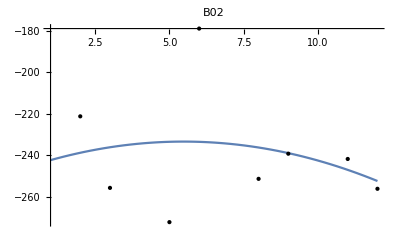
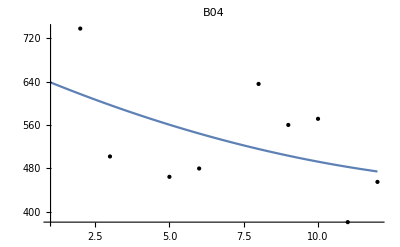
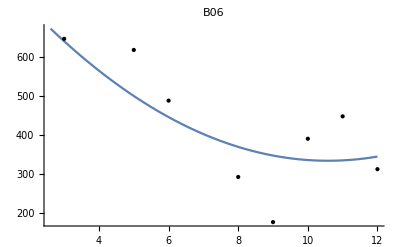
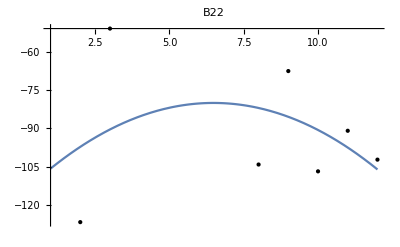
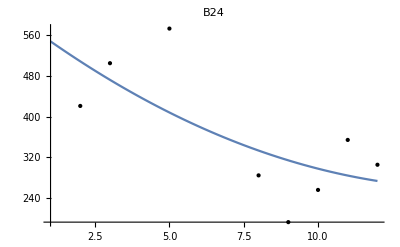
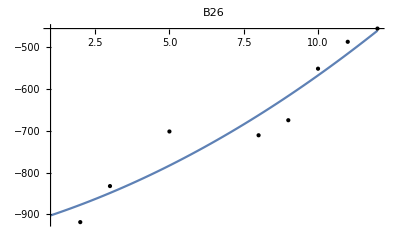
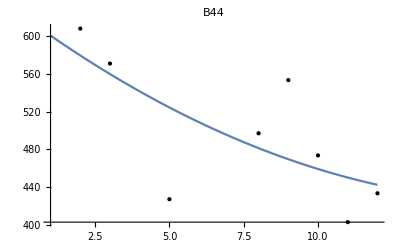
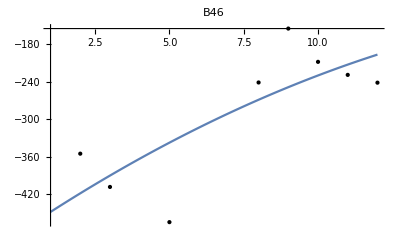

```mathematica
Table[Plot[varModel[var]["function"][x],{x,1,12},Epilog->Point[varModel[var]["data"]],PlotLabel->var,PlotRange->{All,MinMax[Last/@varModel[var]["data"]]}],{var,Keys[varModel]}]
```

```mathematica
billsσ=Values@<|"Ce"->51,"Pr"->16,"Nd"->14,"Pm"->0,"Sm"->13,"Eu"->16,"Gd"->10,"Tb"->12,"Dy"->12,"Ho"->10,"Er"->19,"Tm"->10,"Yb"->38|>;
```

{51,16,14,0,13,16,10,12,12,10,19,10,38}

```mathematica
currentBest={47,16,13,"----",13,17,10,9,11,9,14,11,33};
billsσ={51,16,14,0,13,16,10,12,12,10,19,10,38};
summary={theLanthanides[[#[[1]]]],If[MissingQ[#[[2]]],"-----",Round[#[[2]],1]]}&/@SortBy[Normal[#["bestRMS"]&/@truncatedSols],First];
summary=Transpose@Append[Append[Transpose[summary],currentBest],billsσ];
summary=(Append[#,Which[
Head[#[[2]]]===String,
#[[2]],
#[[2]]<=#[[4]],
"😊",
True,
"🤮"]]&/@summary);
summary=(Append[#,Which[
Head[#[[2]]]===String,
#[[2]],
#[[3]]<=#[[4]],
"😊",
True,
"🤮"]]&/@summary);
TableForm[#[[{1,2,5,3,6,4}]]&/@summary,TableAlignments->Center,TableHeadings->{None,{"","NOW","NOW<=BILL","BEFORE","BEFORE<=BILL","BILL"}}]
```

| NOW | NOW<=BILL | BEFORE | BEFORE<=BILL | BILL
Ce | 49 | 😊 | 47 | 😊 | 51
Pr | 16 | 😊 | 16 | 😊 | 16
Nd | 13 | 😊 | 13 | 😊 | 14
Pm | ----- | ----- | ---- | ----- | 0
Sm | 13 | 😊 | 13 | 😊 | 13
Eu | 14 | 😊 | 17 | 🤮 | 16
Gd | 8 | 😊 | 10 | 😊 | 10
Tb | 9 | 😊 | 9 | 😊 | 12
Dy | 11 | 😊 | 11 | 😊 | 12
Ho | 9 | 😊 | 9 | 😊 | 10
Er | 17 | 😊 | 14 | 😊 | 19
Tm | 13 | 🤮 | 11 | 🤮 | 10
Yb | 49 | 🤮 | 33 | 😊 | 38

```mathematica
Normal@truncatedSols[13]["bestParamsWithConstraints"]//TableForm
```

B02→-234.479
B04→483.916
B06→354.892
B22→-134.729
B24→243.686
B26→-424.081
B44→443.063
B46→-169.57
B66→-466.884
ζ→2915.15
ϵ→-23.8223

## C2 symmetry (all Ln) --- Automatic Truncation Energy --- Adding a constant shift. Using Carnall1989 as starting values. Using spin-spin. Varying all that was varied and fixing all that was fixed. Including Ce and Yb.

```mathematica
Normal@KeySelect[Association[caseConstraints[ln]],Not[MemberQ[cfSymbols,#]]&]
```

{F4→0.71 F2,T2→300.,T3→42.,T4→62.,T6→-295.,T7→350.,T8→310.,β→-600.,γ→1575.}

### Calculations

```mathematica
extraCFparams={S24,S26,S44,S46,S66};
PrintAndDefine[message_]:=(
progressMessage=ToString[ln]<>": "<>message;
Print[message];
)
Off[N::preclg];
withSpinSin=1;
noconstraints=False;
saveEigenvectors=False;
filePrefix=If[withSpinSin==1,
"mirrored-constraints-with-spinspin-and-automatic-truncation",
"mirrored-constraints-without-spinspin-and-automatic-truncation"
];
filePrefix=filePrefix<>"-C2-all";
σexp=2.0;
trunEnergy=Automatic;
truncationEnergies={Automatic};
truncatedSols=<||>;
doThese=complementaryNumE;
numTrials=10;
trials=AssociationThread[theLanthanides,ConstantArray[{},Length[theLanthanides]]];
Do[
(
Do[(
numE=numE0;
ln=theLanthanides[[numE]];
Print[ln];
pVars=variedSymbols[ln];
pVars=Join[pVars,extraCFparams];
constraints=caseConstraints[ln];
constraints==Normal@KeySelect[Association[constraints],Not[MemberQ[cfSymbols,#]]&];
If[ln=="Yb",
constraints=constraints/.(lhs_->rhs_):>(lhs->-rhs)
];
If[noconstraints,
(
constraints={};
pVars=Which[
Or[ln=="Ce",ln=="Yb"],
{ζ,B02,B04,B06,B22,B24,B26,B44,B46,B66},
ln=="Pr",
{F2,F4,F6,ζ,α,β,γ,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66},
ln=="Tm",
{F2,F4,F6,ζ,α,β,γ,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66,T2},
True,
{B02,B04,B06,B22,B24,B26,B44,B46,B66,F2,F4,F6,M0,P2,T2,T3,T4,T6,T7,T8,α,β,γ,ζ}
];
)
];
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=If[OddQ[numE],
Flatten[Position[Flatten[{#,#}&/@(Last/@Carnall[carnalKey]),1],"not included"]],
Flatten[Position[Last/@Carnall[carnalKey],"not included"]]
];
independentVars=Variables[pVars/.constraints];
startValues=AssociationThread[independentVars,independentVars/.LoadLaF3Parameters[ln]];
(*startValues=Join[startValues,AssociationThread[extraCFparams,ConstantArray[0.01,Length[extraCFparams]]]];*)
startValues=Join[startValues,AssociationThread[extraCFparams,RandomReal[{-1000,1000},Length[extraCFparams]]]];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
pVars,
startValues,
constraints,
"SaveEigenvectors"->saveEigenvectors,
"AddConstantShift"->True,
"SignatureCheck"->False,
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->withSpinSin)),
"SymmetrySimplifier"->
{B12->0,B14->0,B16->0,B34->0,B36->0,B56->0,S12->0,S14->0,S16->0,S22->0,S34->0,S36->0,S56->0},
"MaxIterations"->1000,
"MaxHistory"->1000,
"FilePrefix"->filePrefix<>"/"<>ln<>"-"<>ToString[trunEnergy],
"TruncationEnergy"->trunEnergy,
"PrintFun"->PrintAndDefine];
truncatedSols[{numE0, trunEnergy}]=sol;
trials[ln]=Append[trials[ln],sol];
),
{numTrial,1,numTrials}
];
Run["~/Scripts/pushover \"finished fitting "<>ln<>"\""];
)
,{numE0, doThese}]
```

Ce

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ce-Automatic-sols-10649d7d-bb96-4d25-a759-edcfa4e3a49a.m

Finished ...

Ce

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Power::infy: Infinite expression 1/0. encountered.

Inverse::inf: Input matrix contains an infinite entry.

Diagonal::list: List expected at position 1 in Diagonal[Inverse[{{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity},«4»,{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity}}]].

Calculating the uncertainty in the parameters ...

Part::partw: Part 3 of «1» does not exist.

Part::partw: Part 4 of «1» does not exist.

Part::partw: Part 5 of «1» does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ce-Automatic-sols-80967e0f-2e5b-4fe4-979a-b13cb89e6fa5.m

Finished ...

Ce

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ce-Automatic-sols-534eaa6a-7aed-4ed1-80df-476bb8f7c185.m

Finished ...

Ce

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ce-Automatic-sols-18fd0cfa-f08e-4093-b9c5-bc3d03ec9317.m

Finished ...

Ce

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Power::infy: Infinite expression 1/0. encountered.

Inverse::inf: Input matrix contains an infinite entry.

Diagonal::list: List expected at position 1 in Diagonal[Inverse[{{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity},«4»,{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity}}]].

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ce-Automatic-sols-cf8ee249-3da7-4f86-878a-285bcbee4bc2.m

Finished ...

Ce

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ce-Automatic-sols-b25cbe6b-20c8-4121-a368-cc0c57cb6733.m

Finished ...

Ce

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ce-Automatic-sols-81d1da2a-cff2-461d-8932-f0070608ed69.m

Finished ...

Ce

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Inverse::inf: Input matrix contains an infinite entry.

General::stop: Further output of Inverse::inf will be suppressed during this calculation.

Diagonal::list: List expected at position 1 in Diagonal[Inverse[{{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity},«4»,{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity}}]].

General::stop: Further output of Diagonal::list will be suppressed during this calculation.

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ce-Automatic-sols-4ecee65d-caa1-45e2-b324-ffae744d791e.m

Finished ...

Ce

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Max::nord: Invalid comparison with 0.-0.00628666 ⅈ attempted.

Max::nord: Invalid comparison with 0.+0.00648842 ⅈ attempted.

Max::nord: Invalid comparison with 0.+0.00657228 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ce-Automatic-sols-6ddd6b34-4420-4a6f-b526-cbfb4d077d40.m

Finished ...

Ce

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ce-Automatic-sols-8338ab21-ca09-4ca5-a8c1-a7db990d933d.m

Finished ...

Yb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.000114684,0.0000127641,0.000221281,0.0000352818,0.0000297273,-0.00148442},«4»,{-0.00148442,-0.000118846,-0.00236833,-«22»,-0.00086146,0.0942422}} may contain significant numerical errors.

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Yb-Automatic-sols-3c3a0c01-54f1-4883-b292-5bdbfd6eda02.m

Finished ...

Yb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.00011467,0.0000127546,0.000221274,0.0000352895,0.0000297242,-0.00148426},«4»,{-0.00148426,-0.000118693,-0.00236851,-«22»,-0.000861451,0.0942422}} may contain significant numerical errors.

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Yb-Automatic-sols-3229bb11-3bf7-4ce7-ac87-5dcb6164edb4.m

Finished ...

Yb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.000114695,0.0000127657,0.000221288,0.0000352779,0.0000297281,-0.00148449},«4»,{-0.00148449,-0.000118888,-0.00236829,-0.000888518,-0.000861466,0.0942422}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Yb-Automatic-sols-f6650cfb-fdab-4b59-b731-462f19e46ec2.m

Finished ...

Yb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Yb-Automatic-sols-dce33aa6-d20c-4b15-b998-59e732f07517.m

Finished ...

Yb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindMinimum::sszero will be suppressed during this calculation.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Yb-Automatic-sols-6d9eb69b-08a6-4495-a4f7-89239ed9db41.m

Finished ...

Yb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Yb-Automatic-sols-b17c8751-56fb-4253-9f94-da571a8d9e33.m

Finished ...

Yb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Yb-Automatic-sols-213f9f2f-b7f2-4a13-a0e6-bbd765cb5525.m

Finished ...

Yb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Yb-Automatic-sols-14ee2667-2cd4-4d68-b315-c4b5317dd26c.m

Finished ...

Yb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Yb-Automatic-sols-1d543152-163b-474a-a002-5e21da9bfe3c.m

Finished ...

Yb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Yb-Automatic-sols-1950ec62-9c93-4fd7-96cc-13c0bc45ac88.m

Finished ...

Pr

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pr-Automatic-sols-e0927e5a-4d93-4ed5-9380-7957f95bf8e9.m

Finished ...

Pr

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pr-Automatic-sols-7cc2b7ad-a157-49b0-af2c-fb2029318f22.m

Finished ...

Pr

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pr-Automatic-sols-fe386a89-a706-41fc-b721-0a5f69b83449.m

Finished ...

Pr

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pr-Automatic-sols-58f26495-ffaa-42a9-b9a4-e2ad7de9342a.m

Finished ...

Pr

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pr-Automatic-sols-94e552d8-1135-46bb-8507-3e24e3ec480e.m

Finished ...

Pr

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pr-Automatic-sols-aea7bcf0-676b-4221-9b35-b79fb173012a.m

Finished ...

Pr

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pr-Automatic-sols-0e0512bf-dbf1-49ca-b1b4-dd3a70df5040.m

Finished ...

Pr

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pr-Automatic-sols-015a481e-e405-463c-9395-37438940c1b5.m

Finished ...

Pr

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pr-Automatic-sols-0ec42303-1281-44a0-b51b-98f83f8dab41.m

Finished ...

Pr

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pr-Automatic-sols-9c8d21e5-e027-486a-bb99-675d7c28c381.m

Finished ...

Tm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tm-Automatic-sols-fb44c15c-9fe7-4d62-918a-aabd89b6fcc7.m

Finished ...

Tm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tm-Automatic-sols-db948ba1-7984-4f9c-9bcf-5105c097d763.m

Finished ...

Tm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tm-Automatic-sols-9f18388a-b8c6-4dbb-8167-b494a0b28696.m

Finished ...

Tm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tm-Automatic-sols-6d9e05d1-8ca8-4d77-ad44-f9a4ab8a92d9.m

Finished ...

Tm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tm-Automatic-sols-e355bb18-ae40-46ae-b49f-37de7fcbd410.m

Finished ...

Tm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tm-Automatic-sols-70235fc3-5571-4bd5-a809-8d2ba0e669c6.m

Finished ...

Tm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tm-Automatic-sols-0861ef39-3bf7-4a07-a4a0-b78f98e68407.m

Finished ...

Tm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tm-Automatic-sols-28a02459-28e9-48bd-a8d6-2dafe685f0f8.m

Finished ...

Tm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 1000 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tm-Automatic-sols-98088a83-9fc7-4b91-b49f-322891d4840a.m

Finished ...

Tm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tm-Automatic-sols-293a5404-5b69-4036-a723-8f7b8b210cbf.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Nd-Automatic-sols-5fef0c50-091f-4cc0-b6fb-1552b3853b04.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Nd-Automatic-sols-14c8a478-d983-4111-874b-2b62b6b6b75b.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Nd-Automatic-sols-a3a2ff9a-dd76-4c5b-ab31-ad25257e5f50.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Nd-Automatic-sols-b2b49e82-1c73-4262-9039-686d7c61b75e.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Nd-Automatic-sols-0ab36d13-3a76-4086-8d15-e9c313a5f8fe.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Nd-Automatic-sols-6ccdc196-6c8e-4ba1-a125-cf7105aaca58.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Nd-Automatic-sols-8f77a6de-e1e0-4cad-be29-2b3f43159392.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Nd-Automatic-sols-e9969bad-5e97-40ca-b53a-75dce86f5675.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Nd-Automatic-sols-d854e712-a899-4133-8d38-36d769601f33.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Nd-Automatic-sols-ce2ca923-deab-4fa8-9628-684da5ca56ad.m

Finished ...

Er

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Er-Automatic-sols-12fa3d08-2873-4664-9e1c-5d20121cfc12.m

Finished ...

Er

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Er-Automatic-sols-e4fc97c8-3ada-46a4-aea2-89d0b98e942c.m

Finished ...

Er

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Er-Automatic-sols-2a74f608-266a-4497-9e5b-fcb903803f75.m

Finished ...

Er

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Er-Automatic-sols-a2ff8ed5-a2ef-4e7b-bc28-2c6a893d260f.m

Finished ...

Er

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Er-Automatic-sols-208b74cd-4fb3-4ebb-bc79-ca3ede15184a.m

Finished ...

Er

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Er-Automatic-sols-ed2ce7e7-66f1-40ef-a0a3-62977ba6881e.m

Finished ...

Er

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Er-Automatic-sols-e149cd84-efed-443b-9ec1-e01d228f64f1.m

Finished ...

Er

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Er-Automatic-sols-c7711226-b03b-4abc-b3fc-0a8a8e0c683a.m

Finished ...

Er

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Er-Automatic-sols-30ad3947-7ecb-41ef-ba46-ee5a7eb0293a.m

Finished ...

Er

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Er-Automatic-sols-f5850dd1-7df8-479f-ad5b-65fde1d0f712.m

Finished ...

Pm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pm-Automatic-sols-d326d314-40b1-429f-ac7a-f087edf7ce5f.m

Finished ...

Pm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pm-Automatic-sols-c26f061b-a58c-4b78-a53d-5eaa26654c3a.m

Finished ...

Pm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pm-Automatic-sols-c7a749aa-2b3a-4a62-9a32-957438b8f75b.m

Finished ...

Pm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pm-Automatic-sols-5cea4fda-caed-4cb8-ac97-aac1f49808b3.m

Finished ...

Pm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pm-Automatic-sols-77a28f26-416d-41f5-a24a-7dc8f34e8019.m

Finished ...

Pm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pm-Automatic-sols-83c451c5-9a5f-4a4d-9c34-2cb86c5175fd.m

Finished ...

Pm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pm-Automatic-sols-e88993d5-62ab-4573-a7aa-7106523d63a4.m

Finished ...

Pm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pm-Automatic-sols-ea57f052-6155-4838-a609-b63db944c7a1.m

Finished ...

Pm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pm-Automatic-sols-11ed7a97-75cb-4414-86dc-4dd8008e36a2.m

Finished ...

Pm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Pm-Automatic-sols-a3137968-fc25-4e3d-b68c-d63002b4d5b3.m

Finished ...

Ho

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ho-Automatic-sols-88f3157f-0370-4f44-bad8-7f4dbf93992d.m

Finished ...

Ho

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ho-Automatic-sols-18d03e04-2619-4e0d-b078-119f70132dae.m

Finished ...

Ho

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ho-Automatic-sols-771afaf6-6ecb-40d1-8ba7-7c19539ad88a.m

Finished ...

Ho

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ho-Automatic-sols-8db683d7-c0ae-439e-ab0c-5bc54b7c784a.m

Finished ...

Ho

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ho-Automatic-sols-06d1bb05-1e53-49a1-b21c-38458c881759.m

Finished ...

Ho

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ho-Automatic-sols-4c5aa3ec-7cd1-471f-9ad8-8f93b2396738.m

Finished ...

Ho

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ho-Automatic-sols-271898bf-9149-46a2-84f3-57fa51c194cf.m

Finished ...

Ho

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ho-Automatic-sols-deead079-f331-4969-9ce3-48ba6e5aad49.m

Finished ...

Ho

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ho-Automatic-sols-a2d72c49-2a59-48f1-b57c-e59ac282f26a.m

Finished ...

Ho

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Ho-Automatic-sols-de620e85-5cc4-4635-8b75-eeb141458727.m

Finished ...

Sm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Sm-Automatic-sols-f646ae91-b9d3-490e-bbc6-cbf6910671b7.m

Finished ...

Sm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Sm-Automatic-sols-06fb2d13-bc53-4162-87e5-8d00d5ea0db9.m

Finished ...

Sm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Sm-Automatic-sols-24d19bd3-f462-4a08-b0c8-a463a10fee91.m

Finished ...

Sm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Sm-Automatic-sols-46676dcf-f7d3-4249-84ab-dd2a6deeb438.m

Finished ...

Sm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Sm-Automatic-sols-9ebff0f1-30a7-48cd-966c-f380f209cd29.m

Finished ...

Sm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Sm-Automatic-sols-221d5889-4de0-42b1-af30-e485c3945c70.m

Finished ...

Sm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Sm-Automatic-sols-bcd0865f-f699-402b-904d-826ddac1357e.m

Finished ...

Sm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Sm-Automatic-sols-ced9fbf4-3725-45c6-8795-d209ad2a3469.m

Finished ...

Sm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Sm-Automatic-sols-7f083568-6635-4bea-ad60-d4406ffeca1d.m

Finished ...

Sm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Sm-Automatic-sols-37334d8d-3f0c-4063-b1ae-0b95a864901e.m

Finished ...

Dy

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Dy-Automatic-sols-45d65f81-a30e-4b69-bc5c-5e5e92094b0b.m

Finished ...

Dy

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Dy-Automatic-sols-78c49b40-4d02-44c5-a173-b1cde0410981.m

Finished ...

Dy

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Dy-Automatic-sols-62e8bd74-cd0c-4aaa-832c-99cbef3a409b.m

Finished ...

Dy

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Dy-Automatic-sols-404db443-096d-46cc-a7c7-f829920739bc.m

Finished ...

Dy

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Dy-Automatic-sols-76c87411-1cb8-4506-a743-097b380153d8.m

Finished ...

Dy

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Dy-Automatic-sols-fad21f10-b225-4974-95b6-0e660b1a9778.m

Finished ...

Dy

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Dy-Automatic-sols-27640619-f3a9-42dd-9488-08a192984803.m

Finished ...

Dy

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Dy-Automatic-sols-8da4c36c-7f0e-4cb4-b2a1-d5dc751113f2.m

Finished ...

Dy

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Dy-Automatic-sols-c3fd3a95-15b3-4b5c-825f-ff11edb4005f.m

Finished ...

Dy

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Dy-Automatic-sols-50c39a53-7835-4243-adab-dd9c4b58bf93.m

Finished ...

Eu

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Eu-Automatic-sols-ce53c83e-f579-46af-86d7-de86eb60ae7b.m

Finished ...

Eu

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Eu-Automatic-sols-21c0b1dc-d5b6-47bf-baeb-0f95e46ca8d9.m

Finished ...

Eu

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Eu-Automatic-sols-1fb84388-99d1-4170-99ca-d339c4a7259b.m

Finished ...

Eu

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Eu-Automatic-sols-c9712331-4aa5-4e70-a92f-76c0e9c3ad71.m

Finished ...

Eu

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Eu-Automatic-sols-6990163b-a6a2-4acd-82ed-fcdae465ffba.m

Finished ...

Eu

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Eu-Automatic-sols-478e7cff-5284-4a10-a8a3-20507daffe81.m

Finished ...

Eu

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Eu-Automatic-sols-ec3017c6-e996-4556-8188-0e19b5555c98.m

Finished ...

Eu

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Eu-Automatic-sols-c08368c7-5675-4f97-b606-86914da8cce9.m

Finished ...

Eu

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Eu-Automatic-sols-bf65e054-a8af-4b63-b59d-3e28f7594a1d.m

Finished ...

Eu

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Eu-Automatic-sols-6cc387ff-a67d-499f-8476-5ab63e1258fe.m

Finished ...

Tb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tb-Automatic-sols-b3101569-277a-4d8c-8389-03ce006cdeb3.m

Finished ...

Tb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tb-Automatic-sols-5cf36c56-abb2-4aa3-9278-f6ee7e47f637.m

Finished ...

Tb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tb-Automatic-sols-9ffa1a5e-0449-418c-bb25-51b4b2285446.m

Finished ...

Tb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tb-Automatic-sols-489a65cf-be59-4025-8e3e-c18b9e8e324d.m

Finished ...

Tb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tb-Automatic-sols-19a24bdd-e8ef-4d00-80bb-a2695afe2666.m

Finished ...

Tb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tb-Automatic-sols-5cac1fc1-c0ff-4f35-888f-56aaf70dbe6b.m

Finished ...

Tb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tb-Automatic-sols-654577b3-31a6-42d9-83a6-dbc2cb373a41.m

Finished ...

Tb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tb-Automatic-sols-a9a8e626-7e70-4a0f-b7c1-8119f47cae91.m

Finished ...

Tb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tb-Automatic-sols-6a31a5c8-7ae4-4dc7-b3d4-9aace7a22221.m

Finished ...

Tb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Tb-Automatic-sols-b671db59-80cb-45b6-a864-31f5d3eb66df.m

Finished ...

Gd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Gd-Automatic-sols-510390a4-b15a-4581-a55e-fd945237e0ee.m

Finished ...

Gd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Gd-Automatic-sols-1d36b6bc-eb75-4ce0-9f05-ce015f341e69.m

Finished ...

Gd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Gd-Automatic-sols-3811ae74-c945-44df-bee3-4cd925b0db6c.m

Finished ...

Gd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Gd-Automatic-sols-27f9db72-9619-4a5a-9b0b-b6a2fa30cd3e.m

Finished ...

Gd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Gd-Automatic-sols-ec43a867-0eef-43c4-9b99-edbf671620d7.m

Finished ...

Gd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Gd-Automatic-sols-6fd202aa-b3cf-4966-b910-e7b044c36dc6.m

Finished ...

Gd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Gd-Automatic-sols-612818dd-275e-407d-9bad-9bc2ce1372e1.m

Finished ...

Gd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Gd-Automatic-sols-9c644518-c44d-4471-b706-4cb392090c0b.m

Finished ...

Gd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Gd-Automatic-sols-870486f3-b4bb-4c6a-b26a-a7cbb25d0012.m

Finished ...

Gd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2-all/Gd-Automatic-sols-b348267c-e9ee-41e4-9d44-60e3db10e484.m

Finished ...

```mathematica
Run["~/Scripts/pushover \"finished C2 calculation\""]
```

0

```mathematica
billsBest=AssociationThread[theLanthanides,{51,16,14,0,13,16,10,12,12,10,19,10,38}];
```

```mathematica
bestOfbest=(First[#]["bestRMS"])&/@trials;
bestOfbestShowdown=({#,Round[bestOfbest[#]],billsBest[#]})&/@theLanthanides[[1;;]];
Rasterize@TableForm[bestOfbestShowdown,TableHeadings->{None,{"ln","σ_RMS C2_ql","σ_RMS C2v_carnall"}}]
```

-Graphics-

```mathematica
bestOfall=Association[Table[
tkey->Round@MinMax[Abs[#["bestRMS"]]&/@trials[tkey]]
,{tkey,Keys[trials]}]];
bestOfbestShowdownAll=(Flatten@{#,Round[bestOfall[#]],billsBest[#]})&/@theLanthanides[[1;;]];
Rasterize@TableForm[bestOfbestShowdownAll,TableHeadings->{None,{"ln","σ_RMS C2_ql_MIN","σ_RMS C2_ql_MAX","σ_RMS C2v_carnall"}}]
```

-Graphics-

```mathematica
Export["~/Temp/C2-trials-over-all-ln-10-repeats.m",trials]
```

~/Temp/C2-trials-over-all-ln-10-repeats.m

```mathematica
TableForm[bestOfbest[[2;;]]]
```

Pr→16.5596
Nd→11.7901
Pm→3.6612
Sm→12.247
Eu→16.2402
Gd→7.1833
Tb→8.26737
Dy→10.6485
Ho→8.94974
Er→12.9908
Tm→19.8766
Yb→22.7965

```mathematica
extraCFparams
```

{S24,S26,S44,S46,S66}

```mathematica
bestOfbest[[Ordering[bestOfbest]]]
```

{11.7185,11.7185,11.7185,11.7185,11.7185,11.7185,11.7185,11.7901,11.7901,11.7901}

```mathematica
((#["bestParams"])&/@trials[[Ordering[bestOfbest]]])[[1]]
```

{B02→-265.62,B04→497.608,B06→420.843,B22→-52.2301,B24→244.437,B26→-862.67,B44→-63.8895,B46→211.802,B66→688.244,F2→73027.4,F4→52747.1,F6→35763.9,M0→2.16687,P2→207.15,S24→-414.652,S26→450.87,S44→-580.914,S46→307.873,S66→334.665,T2→296.022,T3→39.5037,T4→59.5329,T6→-286.944,T7→337.297,T8→303.826,α→21.367,β→-591.496,γ→1436.48,ζ→885.32,ϵ→-1.31735}

```mathematica
Export["~/Temp/Nd-trials-with-C2.m",trials]
```

~/Temp/Nd-trials-with-C2.m

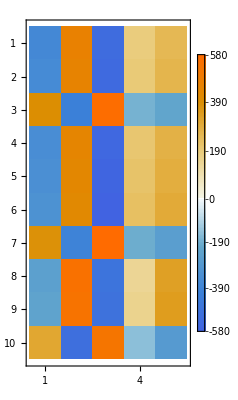

```mathematica
MatrixPlot[(extraCFparams/.#["bestParams"])&/@trials[[Ordering[bestOfbest]]],PlotLegends->Automatic]
```

## C2 symmetry (single ln) --- Automatic Truncation Energy --- Adding a constant shift. Using Carnall1989 as starting values. Using spin-spin. Varying all that was varied and fixing all that was fixed. Including Ce and Yb.

### Calculations

```mathematica
extraCFparams={S24,S26,S44,S46,S66};
PrintAndDefine[message_]:=(
progressMessage=ToString[ln]<>": "<>message;
Print[message];
)
Off[N::preclg];
withSpinSin=1;
noconstraints=False;
saveEigenvectors=False;
filePrefix=If[withSpinSin==1,
"mirrored-constraints-with-spinspin-and-automatic-truncation",
"mirrored-constraints-without-spinspin-and-automatic-truncation"
];
filePrefix=filePrefix<>"-C2";
σexp=2.0;
trunEnergy=Automatic;
truncationEnergies={Automatic};
truncatedSols=<||>;
doThese=complementaryNumE;
doThese={3};
numTrials=10;
trials={};
Do[
(
Do[(
numE=numE0;
ln=theLanthanides[[numE]];
Print[ln];
pVars=variedSymbols[ln];
pVars=Join[pVars,extraCFparams];
constraints=caseConstraints[ln];
If[ln=="Yb",
constraints=constraints/.(lhs_->rhs_):>(lhs->-rhs)
];
If[noconstraints,
(
constraints={};
pVars=Which[
Or[ln=="Ce",ln=="Yb"],
{ζ,B02,B04,B06,B22,B24,B26,B44,B46,B66},
ln=="Pr",
{F2,F4,F6,ζ,α,β,γ,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66},
ln=="Tm",
{F2,F4,F6,ζ,α,β,γ,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66,T2},
True,
{B02,B04,B06,B22,B24,B26,B44,B46,B66,F2,F4,F6,M0,P2,T2,T3,T4,T6,T7,T8,α,β,γ,ζ}
];
)
];
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=If[OddQ[numE],
Flatten[Position[Flatten[{#,#}&/@(Last/@Carnall[carnalKey]),1],"not included"]],
Flatten[Position[Last/@Carnall[carnalKey],"not included"]]
];
independentVars=Variables[pVars/.constraints];
startValues=AssociationThread[independentVars,independentVars/.LoadLaF3Parameters[ln]];
(*startValues=Join[startValues,AssociationThread[extraCFparams,ConstantArray[0.01,Length[extraCFparams]]]];*)
startValues=Join[startValues,AssociationThread[extraCFparams,RandomReal[{-1000,1000},Length[extraCFparams]]]];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
pVars,
startValues,
constraints,
"SaveEigenvectors"->saveEigenvectors,
"AddConstantShift"->True,
"SignatureCheck"->False,
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->withSpinSin)),
"SymmetrySimplifier"->
{B12->0,B14->0,B16->0,B34->0,B36->0,B56->0,S12->0,S14->0,S16->0,S22->0,S34->0,S36->0,S56->0},
"MaxIterations"->1000,
"MaxHistory"->1000,
"FilePrefix"->filePrefix<>"/"<>ln<>"-"<>ToString[trunEnergy],
"TruncationEnergy"->trunEnergy,
"PrintFun"->PrintAndDefine];
truncatedSols[{numE0, trunEnergy}]=sol;
trials=Append[trials,sol];
),
{numTrial,1,numTrials}
];
Run["~/Scripts/pushover \"finished fitting "<>ln<>"\""];
)
,{numE0, doThese}]
```

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2/Nd-Automatic-sols-8aae5a76-b354-447c-9bcb-7d61383bb643.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2/Nd-Automatic-sols-c93c5139-8594-4408-987d-5dd2d5503b82.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindMinimum::sszero will be suppressed during this calculation.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2/Nd-Automatic-sols-14ac70c1-5750-4cad-82b6-02966d0d2f5d.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2/Nd-Automatic-sols-24465900-4bc7-4d7d-a151-929877d2a626.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2/Nd-Automatic-sols-a970e102-4834-4e44-8f7b-1260aeaf2ee6.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2/Nd-Automatic-sols-686dfc18-831b-448a-b1d8-cffdf1d4aa71.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2/Nd-Automatic-sols-662c37f0-57c5-41c1-8e25-bcd5cb95c5ce.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2/Nd-Automatic-sols-61bd0f2b-b540-4bf3-8842-10070db49c84.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2/Nd-Automatic-sols-3f54ed80-e4c3-4a68-8d2a-76eaee12233c.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-C2/Nd-Automatic-sols-ec75ca95-059a-462c-ba48-516c0fa6ceea.m

Finished ...

```mathematica
bestOfbest=(#["bestRMS"])&/@trials
```

{11.7185,11.7185,11.7185,11.7901,11.7901,11.7185,11.7185,11.7185,11.7185,11.7901}

```mathematica
extraCFparams
```

{S24,S26,S44,S46,S66}

```mathematica
bestOfbest[[Ordering[bestOfbest]]]
```

{11.7185,11.7185,11.7185,11.7185,11.7185,11.7185,11.7185,11.7901,11.7901,11.7901}

```mathematica
((#["bestParams"])&/@trials[[Ordering[bestOfbest]]])[[1]]
```

{B02→-265.62,B04→497.608,B06→420.843,B22→-52.2301,B24→244.437,B26→-862.67,B44→-63.8895,B46→211.802,B66→688.244,F2→73027.4,F4→52747.1,F6→35763.9,M0→2.16687,P2→207.15,S24→-414.652,S26→450.87,S44→-580.914,S46→307.873,S66→334.665,T2→296.022,T3→39.5037,T4→59.5329,T6→-286.944,T7→337.297,T8→303.826,α→21.367,β→-591.496,γ→1436.48,ζ→885.32,ϵ→-1.31735}

```mathematica
Export["~/Temp/Nd-trials-with-C2.m",trials]
```

~/Temp/Nd-trials-with-C2.m

```mathematica
MatrixPlot[(extraCFparams/.#["bestParams"])&/@trials[[Ordering[bestOfbest]]],PlotLegends->Automatic]
```

-Graphics-

## -- Omnibus approach for bookends -- --- Automatic Truncation Energy --- Adding a constant shift. Using Carnall1989 as starting values. Using spin-spin. Varying all that was varied and fixing all that was fixed. Including Ce and Yb.

### Calculations

```mathematica
compileIntermediateTruncatedHamCe=Import["/Users/juan/ZiaLab/Codebase/qlanth/compiled/Ce-compiled-intermediate-truncated-ham-5516591406210902397.mx"][[1]];
compileIntermediateTruncatedHamPr=Import["/Users/juan/ZiaLab/Codebase/qlanth/compiled/Pr-compiled-intermediate-truncated-ham-4540466466975356081.mx"][[1]];
```

```mathematica
addShift=True;
maxIter=1000;
paramSols={};
rmsHistory={};
maxHistory=200;

carnalKey="appendix:"<>"Ce"<>":RawTable";
Protect/@{ϵ1,ϵ2};
Protect/@{ζ1,ζ2};
expData1={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
expData1=Flatten[{#,#}&/@expData1,1];
presentDataIndices1=Flatten[Position[expData1,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices1=
Flatten[Position[Flatten[{#,#}&/@(Last/@Carnall[carnalKey]),1],"not included"]];

carnalKey="appendix:"<>"Pr"<>":RawTable";
expData2={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
presentDataIndices2=Flatten[Position[expData2,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices2=
Flatten[Position[Flatten[{#,#}&/@(Last/@Carnall[carnalKey]),1],"not included"]];



problemVars1={B02,B04,B06,B22,B24,B26,B44,B46,B66,ζ1};
problemVars2={B02,B04,B06,B22,B24,B26,B44,B46,B66,F2,F4,F6,M0,P2,α,β,γ,ζ2};
problemVars={B02,B04,B06,B22,B24,B26,B44,B46,B66,F2,F4,F6,M0,P2,α,β,γ,ζ1,ζ2};
constraints={};

varsWithConstants1=ToString/@{B02,B04,B06,B22,B24,B26,B44,B46,B66,0.,0.,0.,0.,0.,0.,0.,0.,ζ1};
varsWithConstantsString1=ToString[varsWithConstants1];
varsWithConstants2=ToString/@{B02,B04,B06,B22,B24,B26,B44,B46,B66,F2,F4,F6,M0,P2,α,β,γ,ζ2};
varsWithConstantsString2=ToString[varsWithConstants2];
problemVarsString1=StringJoin[Riffle[ToString/@problemVars1,", "]];
problemVarsString2=StringJoin[Riffle[ToString/@problemVars2,", "]];

problemVarsQ1=(ToString[#]<>"_?NumericQ")&/@problemVars1;
problemVarsQString1=StringJoin[Riffle[problemVarsQ1,", "]];
ClearAll[HamSortedEigenvalues1];
hamEigenvaluesTemplate1=StringTemplate["
    HamSortedEigenvalues1[`problemVarsQ`]:=(
      ham         = compileIntermediateTruncatedHamCe@@`varsWithConstants`;
      eigenValues = Chop[Sort@Eigenvalues@ham];
      eigenValues = eigenValues - Min[eigenValues];
      HamSortedEigenvalues[`problemVarsString`] = eigenValues;
      Return[eigenValues]
    )"];
hamString1=hamEigenvaluesTemplate1[<|"problemVarsQ"->problemVarsQString1,"varsWithConstants"->varsWithConstantsString1,"problemVarsString"->problemVarsString1|>];
ToExpression[hamString1];

problemVarsQ2=(ToString[#]<>"_?NumericQ")&/@problemVars2;
problemVarsQString2=StringJoin[Riffle[problemVarsQ2,", "]];
ClearAll[HamSortedEigenvalues2];
hamEigenvaluesTemplate2=StringTemplate["
    HamSortedEigenvalues2[`problemVarsQ`]:=(
      ham         = compileIntermediateTruncatedHamPr@@`varsWithConstants`;
      eigenValues = Chop[Sort@Eigenvalues@ham];
      eigenValues = eigenValues - Min[eigenValues];
      HamSortedEigenvalues[`problemVarsString`] = eigenValues;
      Return[eigenValues]
    )"];
hamString2=hamEigenvaluesTemplate2[<|"problemVarsQ"->problemVarsQString2,"varsWithConstants"->varsWithConstantsString2,"problemVarsString"->problemVarsString2|>];
ToExpression[hamString2];
Clear[PartialHamEigenvalues1];
Clear[PartialHamEigenvalues2];
(*we also need a function that will pick the i-th eigenvalue,this seems unnecessary but it's needed to form the right functional form expected by the Levenberg-Marquardt method*)
eigenvalueDispenserTemplate1=StringTemplate["
    PartialHamEigenvalues1[`problemVarsQ`][i_]:=(
      eigenVals = HamSortedEigenvalues1[`problemVarsString`];
      eigenVals[[i]]
    )
    "];
eigenValueDispenserString1=eigenvalueDispenserTemplate1[<|"problemVarsQ"->problemVarsQString1,"problemVarsString"->problemVarsString1|>];
ToExpression[eigenValueDispenserString1];

(*we also need a function that will pick the i-th eigenvalue,this seems unnecessary but it's needed to form the right functional form expected by the Levenberg-Marquardt method*)
eigenvalueDispenserTemplate2=StringTemplate["
    PartialHamEigenvalues2[`problemVarsQ`][i_]:=(
      eigenVals = HamSortedEigenvalues2[`problemVarsString`];
      eigenVals[[i]]
    )
    "];
eigenValueDispenserString2=eigenvalueDispenserTemplate2[<|"problemVarsQ"->problemVarsQString2,"problemVarsString"->problemVarsString2|>];
ToExpression[eigenValueDispenserString2];

constrainedProblemVars=problemVars;
constrainedProblemVars1=problemVars1;
constrainedProblemVars2=problemVars2;
constrainedProblemVarsList=Variables[constrainedProblemVars];
If[addShift,
Print["Adding a constant shift to the fitting parameters ..."];
constrainedProblemVarsList=Join[constrainedProblemVarsList,{ϵ1,ϵ2}]
];

indepVars=Complement[problemVars,#[[1]]&/@constraints];
stringPartialVars=ToString/@constrainedProblemVarsList;

startValues=AssociationThread[indepVars,indepVars/.LoadLaF3Parameters["Pr"]];
startValues[ζ2]=751.7;
startValues[ζ1]=647.3;
startValues=KeyDrop[startValues,ζ];

problemVarsWithStartValues=KeyValueMap[{#1,#2}&,startValues];
If[addShift,
problemVarsWithStartValues=Join[problemVarsWithStartValues,
{{ϵ1,0},{ϵ2,0}}];
];

degreesOfFreedom=Length[presentDataIndices1]+Length[presentDataIndices2]-Length[problemVars]-2;

shiftToggle=If[addShift,1,0];
steps =0;
sol=FindMinimum[Sum[(expData1[[j]][[1]]-(PartialHamEigenvalues1@@constrainedProblemVars1)[j]-shiftToggle*ϵ1)^2,{j,presentDataIndices1}]+
Sum[(expData2[[j]][[1]]-(PartialHamEigenvalues2@@constrainedProblemVars2)[j]-shiftToggle*ϵ2)^2,{j,presentDataIndices2}],
problemVarsWithStartValues,
Method->"LevenbergMarquardt",
MaxIterations->maxIter,
AccuracyGoal->5,
StepMonitor:>(
steps+=1;
currentSqSum=Sum[(expData1[[j]][[1]]-(PartialHamEigenvalues1@@constrainedProblemVars1)[j]-shiftToggle*ϵ1)^2,{j,presentDataIndices1}]+
Sum[(expData2[[j]][[1]]-(PartialHamEigenvalues2@@constrainedProblemVars2)[j]-shiftToggle*ϵ2)^2,{j,presentDataIndices2}];
currentRMS=Sqrt[currentSqSum/degreesOfFreedom];
paramSols=AddToList[paramSols,constrainedProblemVarsList,maxHistory];
rmsHistory=AddToList[rmsHistory,currentRMS,maxHistory];
)
];
```

Adding a constant shift to the fitting parameters ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

```mathematica
problemVars
```

{B02,B04,B06,B22,B24,B26,B44,B46,B66,F2,F4,F6,M0,P2,α,β,γ,ζ1,ζ2}

```mathematica
TableForm@sol[[2]]
```

B02→-205.009
B04→829.274
B06→778.36
B22→-99.0177
B24→492.664
B26→-949.212
B44→607.381
B46→-358.395
B66→-855.972
F2→68855.8
F4→50357.4
F6→32916.3
M0→1.92784
P2→-51.7601
α→16.0166
β→-534.215
γ→1344.68
ζ1→645.093
ζ2→749.89
ϵ1→-6.23653
ϵ2→-11.1785

```mathematica
currentRMS
```

23.115

```mathematica
Dynamic[currentRMS]
```

## -- Copy/Paste from bookends -- --- Automatic Truncation Energy --- Adding a constant shift. Using Carnall1989 as starting values. Using spin-spin. Varying all that was varied and fixing all that was fixed. Including Ce and Yb.

### Calculations

```mathematica
cfParams={B02,B04,B06,B22,B24,B26,B44,B46,B66};
PrintAndDefine[message_]:=(
progressMessage=ToString[ln]<>": "<>message;
Print[message];
)
PrintTempAndDefine[message_]:=(
progressMessage=ToString[ln]<>": "<>message;
PrintTemporary[message];
)
Off[N::preclg];
withSpinSin=1;
noconstraints=False;
saveEigenvectors=False;
filePrefix=If[withSpinSin==1,
"mirrored-constraints-with-spinspin-and-automatic-truncation",
"mirrored-constraints-without-spinspin-and-automatic-truncation"
];
filePrefix=filePrefix<>"-copy-paste";
σexp=2.0;
truncatedSols=<||>;
doThese=complementaryNumE;
doThese={2,12};
trunEnergy=Automatic;
Do[(
numE=numE0;
ln=theLanthanides[[numE]];
Print[ln];
pVars=variedSymbols[ln];
constraints=caseConstraints[ln];
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=If[OddQ[numE],
Flatten[Position[Flatten[{#,#}&/@(Last/@Carnall[carnalKey]),1],"not included"]],
Flatten[Position[Last/@Carnall[carnalKey],"not included"]]
];
independentVars=Variables[pVars/.constraints];
startValues=AssociationThread[independentVars,independentVars/.LoadLaF3Parameters[ln]];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
pVars,
startValues,
constraints,
"SaveEigenvectors"->saveEigenvectors,
"AddConstantShift"->True,
"SignatureCheck"->False,
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->withSpinSin)),
"MaxIterations"->1000,
"MaxHistory"->1000,
"FilePrefix"->filePrefix<>"/"<>ln<>"-"<>ToString[trunEnergy],
"TruncationEnergy"->trunEnergy,
"PrintFun"->PrintAndDefine];
truncatedSols[{numE0, trunEnergy}]=sol;
Run["~/Scripts/pushover \"finished fitting "<>ln<>"\""];
),
{numE0, doThese}];
```

Pr

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Pr-Automatic-sols-1c347cfa-8d97-4a29-8ccf-b586db1a690a.m

Finished ...

Tm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Tm-Automatic-sols-40dac5e2-e4b4-4daa-92d8-d647c5a5d9e0.m

Finished ...

```mathematica
numE0=1;
numE=numE0;
relaxing=Subsets[cfParams,{4}];
ln=theLanthanides[[numE]];
(*ceriumSols=<||>;*)
Do[(
pVars=Join[{ζ},relaxed];
cfParmsRelaxed=Complement[cfParams,relaxed];
constraints=(#->truncatedSols[{2,Automatic}]["bestParamsWithConstraints"][#])&/@cfParmsRelaxed;
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=If[OddQ[numE],
Flatten[Position[Flatten[{#,#}&/@(Last/@Carnall[carnalKey]),1],"not included"]],
Flatten[Position[Last/@Carnall[carnalKey],"not included"]]
];
independentVars=Variables[pVars/.constraints];
startValues=AssociationThread[independentVars,independentVars/.LoadLaF3Parameters[ln]];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
pVars,
startValues,
constraints,
"SaveEigenvectors"->saveEigenvectors,
"AddConstantShift"->True,
"SignatureCheck"->False,
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->withSpinSin)),
"MaxIterations"->1000,
"MaxHistory"->1000,
"FilePrefix"->filePrefix<>"/"<>ln<>"-"<>ToString[trunEnergy],
"TruncationEnergy"->trunEnergy,
"PrintFun"->PrintTempAndDefine];
Print[relaxed,":",sol["bestRMS"]];
ceriumSols[relaxed]=sol;
),
{relaxed,relaxing}]
```

```mathematica
summary=SortBy[({#[[1]],#[[2]]})&/@(Normal[#[["bestRMS"]]&/@ceriumSols]),Last];
```

```mathematica
numE0=1;
numE=numE0;
depths=6;
ln=theLanthanides[[numE]];
(*ceriumSols=<||>;*)
jacobsLadder={};
bestRungs=<||>;
Do[
(
ladderSols=<||>;
Do[
(
If[MemberQ[jacobsLadder,newCF],Continue[]];
relaxed=Append[jacobsLadder,newCF];
pVars=Join[{ζ},relaxed];
cfParmsRelaxed=Complement[cfParams,relaxed];
constraints=(#->truncatedSols[{2,Automatic}]["bestParamsWithConstraints"][#])&/@cfParmsRelaxed;
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=If[OddQ[numE],
Flatten[Position[Flatten[{#,#}&/@(Last/@Carnall[carnalKey]),1],"not included"]],
Flatten[Position[Last/@Carnall[carnalKey],"not included"]]
];
independentVars=Variables[pVars/.constraints];
startValues=AssociationThread[independentVars,independentVars/.LoadLaF3Parameters[ln]];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
pVars,
startValues,
constraints,
"SaveEigenvectors"->saveEigenvectors,
"AddConstantShift"->True,
"SignatureCheck"->False,
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->withSpinSin)),
"MaxIterations"->1000,
"MaxHistory"->1000,
"FilePrefix"->filePrefix<>"/"<>ln<>"-"<>ToString[trunEnergy],
"TruncationEnergy"->trunEnergy,
"PrintFun"->PrintTempAndDefine];
Print[relaxed,":",sol["bestRMS"]];
sol["extraRung"]=newCF;
ladderSols[newCF]=sol;
),
{newCF,cfParams}
];
bestRung=SortBy[ladderSols,#["bestRMS"]&][[1]];
jacobsLadder=Append[jacobsLadder,bestRung["extraRung"]];
bestRungs[jacobsLadder]=bestRung;
),
{depth,1,depths}]
```

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-efb8189a-7a82-4790-ae52-9e5ca21dcef9.m

{B02}:52.3533

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-c2e0df28-78ee-4a3f-b3bc-672f698388b9.m

{B04}:37.292

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-c52351f7-c506-4906-8e36-d76db6cd5798.m

{B06}:46.1642

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-41367d07-491e-4208-ab9f-ff200d526931.m

{B22}:49.7669

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-ee806370-cabe-4c73-98b6-ed33c6b44726.m

{B24}:42.7917

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-db08b9e6-2729-4820-baf1-4ec62143a382.m

{B26}:22.7995

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-247d8b47-c266-4a0c-b6d8-a76f0be6949e.m

{B44}:44.5904

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-829c4ec5-878a-4d50-a00b-b87dc7c49182.m

{B46}:53.7311

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-2686466e-59f5-4d3d-a2f8-a602af865e4c.m

{B66}:44.5003

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-b373e0b0-a772-4abd-be70-7dc60edf9b1e.m

{B26,B02}:21.9709

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-735adf8e-fe94-4528-b27a-85d65bada70b.m

{B26,B04}:14.8009

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-122c052c-8903-4ab9-a465-a71ad9d3a3a8.m

{B26,B06}:20.2246

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-3a4f36b7-a40d-46f9-9e33-16b933518d91.m

{B26,B22}:21.3506

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-b3c2fa20-6124-4232-bc0c-e401c48bd4c5.m

{B26,B24}:21.7873

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-f928185f-cc7f-4c6b-a4d0-0176bb7c945c.m

{B26,B44}:20.0896

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-0194edb4-805e-4bcb-baa9-d0ac9959311b.m

{B26,B46}:23.7853

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-2e39dd9a-2989-4b8b-a0f6-d485fe410923.m

{B26,B66}:22.751

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-67d9e2d6-2de7-4e59-bdc8-8460ad21cff5.m

{B26,B04,B02}:9.55028

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-2ba93524-b8aa-4304-a7ef-9ce078f70acb.m

{B26,B04,B06}:14.7571

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-7a411387-b6c8-4dab-bda4-dec825cbd318.m

{B26,B04,B22}:11.6936

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-9e3dfdeb-4996-409d-b5c5-bdfab742e1c4.m

{B26,B04,B24}:14.097

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-d8f87804-c959-4347-8d1f-722b1343463b.m

{B26,B04,B44}:15.109

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-11a75411-c4f7-4383-9658-cc74efe1b6ec.m

{B26,B04,B46}:15.3466

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-988e06f9-2a08-442a-84cf-6067b2d8d18e.m

{B26,B04,B66}:14.4194

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-36311aa7-1abe-42b9-a4b5-02712a7e9255.m

{B26,B04,B02,B06}:0.361593

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-438426db-f5d7-46fe-86a5-7211b84cfc6a.m

{B26,B04,B02,B22}:10.1295

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-5e1b5a9a-9b08-4f24-b308-a72514b7da37.m

{B26,B04,B02,B24}:8.34603

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-6748ccc9-b0fd-43bf-8986-ccfceb7089a6.m

{B26,B04,B02,B44}:8.43771

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-b2c04b2f-f96f-45c1-a1e5-6f37fd09358a.m

{B26,B04,B02,B46}:9.17412

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindMinimum::sszero will be suppressed during this calculation.

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-f2f044cb-1582-43ad-96f6-f34c936e933c.m

{B26,B04,B02,B66}:8.24042

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-3ce3da1e-c295-4274-a140-217fddb642a5.m

{B26,B04,B02,B06,B22}:0.000097874

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-16914549-9f41-4f30-b793-9368ecee1aeb.m

{B26,B04,B02,B06,B24}:0.000149505

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-8f1fd302-a4a0-4aa4-9d22-842d5a7fcf12.m

{B26,B04,B02,B06,B44}:0.000149505

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-5f34f37d-d30f-46bc-ab0a-37aaf7913c7a.m

{B26,B04,B02,B06,B46}:0.00012207

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-f3b7f72f-2649-4438-a6bb-24fe51791b12.m

{B26,B04,B02,B06,B66}:0.000108204

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.18433×10^7,-3.9486×10^6,4.48523×10^6,2.85173×10^7,4.90564×10^6,-1.41648×10^6,2.50986×10^7},«5»,{2.50986×10^7,-974066.,1.78942×10^7,1.52906×10^8,5.76297×10^8,-1.47636×10^8,1.07944×10^10}} may contain significant numerical errors.

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-2dba01d6-0df4-4397-aee4-a1f8e5481ae9.m

{B26,B04,B02,B06,B22,B24}:0.0000932327

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.75639×10^7,-1.95779×10^6,3.41866×10^6,4.18233×10^7,-1.23691×10^6,-5.77321×10^6,-2.25187×10^7},«5»,{-2.25187×10^7,4.98168×10^8,6.69553×10^6,2.28739×10^8,-2.2095×10^8,6.28165×10^8,1.51137×10^10}} may contain significant numerical errors.

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-d3e03a42-2bae-4992-ba97-6b37b5fb944b.m

{B26,B04,B02,B06,B22,B44}:0.000078796

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Inverse::luc: Result for Inverse of badly conditioned matrix {{3.06458×10^7,-9.05649×10^6,2.84972×10^6,4.28441×10^7,1.8419×10^6,2.09912×10^6,-1.40848×10^8},«5»,{-1.40848×10^8,5.55372×10^8,-6.61146×10^6,3.18009×10^8,-2.68944×10^8,-4.66419×10^7,1.4998×10^10}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-f79ca9b3-f896-4252-b110-4a91d21be932.m

{B26,B04,B02,B06,B22,B46}:0.000078796

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

Max::nord: Invalid comparison with 0.-12966.1 ⅈ attempted.

Max::nord: Invalid comparison with 0.+12966.1 ⅈ attempted.

Max::nord: Invalid comparison with 0.-12966.1 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Ce-Automatic-sols-df5bcda3-4756-4351-b15b-67cf806e0333.m

{B26,B04,B02,B06,B22,B66}:0.0000610352

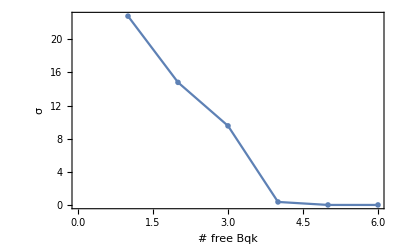

```mathematica
ListPlot[KeyValueMap[{Length[#1],#2}&,#["bestRMS"]&/@bestRungs],Joined->True,PlotMarkers->"OpenMarkers",Frame->True,FrameLabel->{"# free Bqk","σ"}]
```

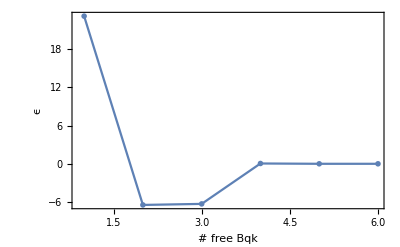

```mathematica
ListPlot[KeyValueMap[{Length[#1],#2}&,(ϵ)/.#["bestParams"]&/@bestRungs],Joined->True,PlotMarkers->"OpenMarkers",PlotRange->All,Frame->True,FrameLabel->{"# free Bqk","ϵ"}]
```

```mathematica
TableForm[Normal[#["bestParamsWithConstraints"]&/@bestRungs]]
```

{B26}→<|B02→-221.216,B04→737.938,B06→672.996,B22→-126.739,B24→420.805,B44→608.423,B46→-355.425,B66→-788.801,B26→-1665.78,ζ→633.145,ϵ→23.2042|>
{B26,B04}→<|B02→-221.216,B06→672.996,B22→-126.739,B24→420.805,B44→608.423,B46→-355.425,B66→-788.801,B04→984.502,B26→-1578.97,ζ→634.294,ϵ→-6.46433|>
{B26,B04,B02}→<|B06→672.996,B22→-126.739,B24→420.805,B44→608.423,B46→-355.425,B66→-788.801,B02→-123.964,B04→1004.36,B26→-1567.28,ζ→634.62,ϵ→-6.29967|>
{B26,B04,B02,B06}→<|B22→-126.739,B24→420.805,B44→608.423,B46→-355.425,B66→-788.801,B02→-90.1765,B04→949.653,B06→467.502,B26→-1652.81,ζ→633.764,ϵ→0.0494328|>
{B26,B04,B02,B06,B22}→<|B24→420.805,B44→608.423,B46→-355.425,B66→-788.801,B02→-79.8635,B04→952.743,B06→465.025,B22→-130.01,B26→-1650.96,ζ→633.814,ϵ→-1.14877×10^-13|>
{B26,B04,B02,B06,B22,B66}→<|B24→420.805,B44→608.423,B46→-355.425,B02→-217.692,B04→909.813,B06→537.321,B22→-68.0113,B26→-1556.1,B66→-933.262,ζ→634.189,ϵ→-6.03459×10^-11|>

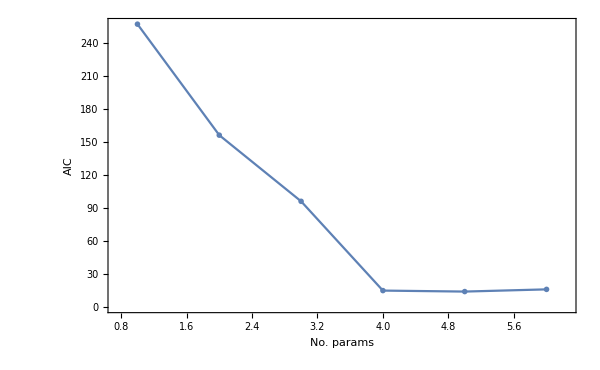

```mathematica
ListPlot[KeyValueMap[{Length[#1],2(Length[#1]+1+1)+2 1/2#2["bestRMS"]*#2["degreesOfFreedom"]}&,bestRungs],
Frame->True,
Joined->True,
PlotMarkers->"OpenMarkers",
FrameLabel->{"No. params","AIC"},
FrameStyle->Directive[13],
PlotRange->{{0.75,depths+0.25},All},
ImageSize->600]
```

```mathematica
bestSet=Keys[bestRungs][[4]];
standardValues=bestSet/.LoadLaF3Parameters["Ce"];
bestGreedy=bestSet/.bestRungs[bestSet]["bestParamsWithConstraints"];
standardValues/bestGreedy
```

{0.557234,0.777126,2.41748,1.4524}

```mathematica
bestRungs[bestSet]["bestParamsWithConstraints"]
```

<|B22→-126.739,B24→420.805,B44→608.423,B46→-355.425,B66→-788.801,B02→-90.1765,B04→949.653,B06→467.502,B26→-1652.81,ζ→633.764,ϵ→0.0494328|>

## --- Automatic Truncation Energy --- Adding a constant shift. Using Carnall1989 as starting values. Using spin-spin. Everything floats. Including Ce and Yb.

### Calculations

```mathematica
PrintAndDefine[message_]:=(
progressMessage=ToString[ln]<>": "<>message;
Print[message];
)
Off[N::preclg];
withSpinSin=1;
noconstraints=True;
saveEigenvectors=False;
filePrefix=If[withSpinSin==1,
"no-constraints-with-spinspin-and-automatic-truncation",
"no-constraints-without-spinspin-and-automatic-truncation"
];
σexp=2.0;
truncationEnergies={Automatic};
truncatedSols=<||>;
doThese=complementaryNumE;
Do[
(
Do[(
numE=numE0;
ln=theLanthanides[[numE]];
Print[ln];
pVars=variedSymbols[ln];
constraints=caseConstraints[ln];
If[ln=="Yb",
constraints=constraints/.(lhs_->rhs_):>(lhs->-rhs)
];
If[noconstraints,
(
constraints=Which[
ln=="Ce",
{B22->-126.,B24->420.,B44->608.,B46->-355.,B66->-788.},
True,
{}
];
pVars=Which[
ln=="Yb",
{ζ,B02,B04,B06,B22,B24,B26,B44,B46,B66},
ln=="Ce",
{ζ,B26,B04,B02,B06},
ln=="Pr",
{F2,F4,F6,ζ,α,β,γ,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66},
ln=="Tm",
{F2,F4,F6,ζ,α,β,γ,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66,T2},
True,
{B02,B04,B06,B22,B24,B26,B44,B46,B66,F2,F4,F6,M0,P2,T2,T3,T4,T6,T7,T8,α,β,γ,ζ}
];
)
];
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=If[OddQ[numE],
Flatten[Position[Flatten[{#,#}&/@(Last/@Carnall[carnalKey]),1],"not included"]],
Flatten[Position[Last/@Carnall[carnalKey],"not included"]]
];
independentVars=Variables[pVars/.constraints];
startValues=AssociationThread[independentVars,independentVars/.LoadLaF3Parameters[ln]];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
pVars,
startValues,
constraints,
"SaveEigenvectors"->saveEigenvectors,
"AddConstantShift"->True,
"SignatureCheck"->False,
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->withSpinSin)),
"MaxIterations"->1000,
"MaxHistory"->1000,
"FilePrefix"->filePrefix<>"/"<>ln<>"-"<>ToString[trunEnergy],
"TruncationEnergy"->trunEnergy,
"PrintFun"->PrintAndDefine];
truncatedSols[{numE0, trunEnergy}]=sol;
),
{trunEnergy,truncationEnergies}
];
Run["~/Scripts/pushover \"finished fitting "<>ln<>"\""];
)
,{numE0, doThese}]
```

Ce

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/no-constraints-with-spinspin-and-automatic-truncation/Ce-Automatic-sols-e53faa5c-d5e6-4927-955d-c2c9be675eb2.m

Finished ...

Yb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Inverse::luc: Result for Inverse of badly conditioned matrix {{-4.34565×10^6+0. ⅈ,473301.+0. ⅈ,792572.+0. ⅈ,-5.37301×10^6+0. ⅈ,645842.+0. ⅈ,-116846.+0. ⅈ,3.03793×10^6+0. ⅈ,-768562.+0. ⅈ,-704988.+0. ⅈ,2.1456×10^7+0. ⅈ},«8»,{2.1456×10^7+0. ⅈ,«8»,-8.21055×10^8+0. ⅈ}} may contain significant numerical errors.

Max::nord: Invalid comparison with 0.+643.133 ⅈ attempted.

Max::nord: Invalid comparison with 0.+19610.6 ⅈ attempted.

Max::nord: Invalid comparison with 0.-19881.9 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/no-constraints-with-spinspin-and-automatic-truncation/Yb-Automatic-sols-9e66173d-42c3-4826-be17-b8c7ebc6a480.m

Finished ...

Pr

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/no-constraints-with-spinspin-and-automatic-truncation/Pr-Automatic-sols-e0db1cd7-8beb-4bd2-a45a-f23cec002734.m

Finished ...

Tm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindMinimum::sszero will be suppressed during this calculation.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.00793515,-0.00052853,-0.000729071,0.00613395,-0.00113008,0.00403624,-0.000707415,0.00140027,0.00198053,-0.00183296,«9»},«9»,«9»} may contain significant numerical errors.

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/no-constraints-with-spinspin-and-automatic-truncation/Tm-Automatic-sols-a47b1c10-e7aa-49bb-b1bd-7ee39c0cc456.m

Finished ...

Nd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/no-constraints-with-spinspin-and-automatic-truncation/Nd-Automatic-sols-ee526a74-212a-422b-8347-fbbb627153ae.m

Finished ...

Er

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/no-constraints-with-spinspin-and-automatic-truncation/Er-Automatic-sols-eaa8d4fd-5efc-48c4-a265-d71d2815d0e1.m

Finished ...

Pm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.087972,0.00951984,0.00738717,0.0471737,0.00639112,-0.0265287,0.000790185,-0.00110486,-0.0351336,0.0267829,«14»},«9»,«14»} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/no-constraints-with-spinspin-and-automatic-truncation/Pm-Automatic-sols-bc5c0e47-f464-4a86-8293-829886804201.m

Finished ...

Ho

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/no-constraints-with-spinspin-and-automatic-truncation/Ho-Automatic-sols-75c913dd-d5a8-4855-bf91-f7340002ab47.m

Finished ...

Sm

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/no-constraints-with-spinspin-and-automatic-truncation/Sm-Automatic-sols-b52e2fca-ac54-4d88-8f1c-9966ed26ab3c.m

Finished ...

Dy

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/no-constraints-with-spinspin-and-automatic-truncation/Dy-Automatic-sols-f9ab13a6-af66-49ea-bcac-7d63922bf1d2.m

Finished ...

Eu

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/no-constraints-with-spinspin-and-automatic-truncation/Eu-Automatic-sols-e3772be6-dbde-4de5-a2ad-791a4e1039f9.m

Finished ...

Tb

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/no-constraints-with-spinspin-and-automatic-truncation/Tb-Automatic-sols-917ca351-a13f-42e4-bcbe-e06c012865dd.m

Finished ...

Gd

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/no-constraints-with-spinspin-and-automatic-truncation/Gd-Automatic-sols-a53d0529-2da1-4822-98e9-090333bc3adf.m

Finished ...

```mathematica
truncatedSols//Keys
```

{{12,Automatic}}

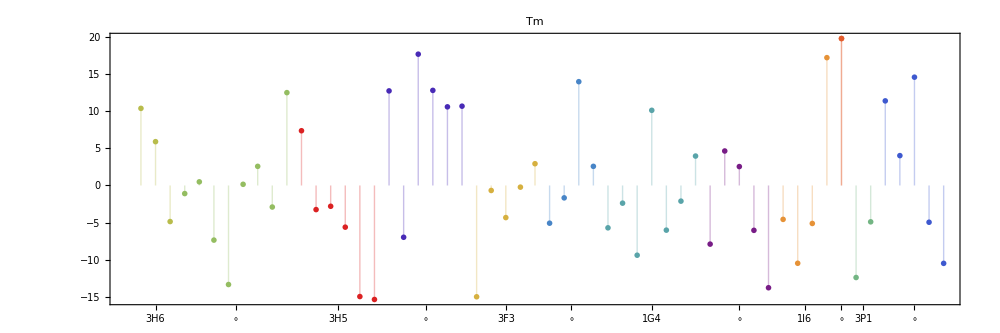

```mathematica
solution=truncatedSols[{numE, truncationEnergies[[1]]}];
solExpData=solution["expData"];
fitEnergies=If[saveEigenvectors,
First/@solution["states"],
solution["energies"]
];
picker=NumericQ[#[[1]]]&/@solExpData;
fitEnergies=PadRight[fitEnergies,Length[solExpData],""];
diffs=Pick[(First/@solExpData)-fitEnergies[[;;Length[solExpData]]],picker];
labels=Last/@solExpData;
stateLabels=#[[2]]&/@solExpData;
ListLabelPlot[diffs,Pick[stateLabels,picker],ImageSize->1000,Filling->Axis,AspectRatio->1/3,PlotMarkers->"OpenMarkers",PlotLabel->ln,PlotRange->Automatic]
```

```mathematica
params=solution["bestParamsWithConstraints"];
params[σSS]=1;
params[M2]=56/100 params[M0];
params[M4]=38/100 params[M0];
params[P4]=3/4 params[P2];
params[P6]=1/2 params[P2];
params[nE]=numE;
params[t2Switch]=If[numE>7,
0,
1
];
params=ParamPad[params];
```

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,E0,E1,E2,E3,F0,gs,P0,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,T3,T4,T6,T7,T8,wChErrA,wChErrB,Ω2,Ω4,Ω6}

File /Users/juan/ZiaLab/Codebase/qlanth/hams/D2d-SymbolicMatrix-f12.mx already exists, and option "Overwrite" is set to False, loading file ...

Following symbols were not given and are being set to 0: {}

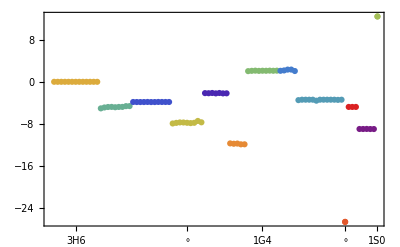

```mathematica
basis=BasisLSJMJ[numE];
solverStates=IonSolver[numE,params,"D2d-","Overwrite Hamiltonian"->False];
stateEnergies=Sort[#[[1]]&/@Chop[solverStates]][[;;Length[fitEnergies]]];
stateEnergies=stateEnergies-stateEnergies[[1]];
deltas=Chop[stateEnergies-Sort[(fitEnergies-fitEnergies[[1]])]];
ListLabelPlot[deltas[[;;Length[expData]]],stateLabels,PlotRange->{All,Automatic}]
```

### Plots

```mathematica
BetterSymbol::usage="BetterSymbol[symbol] takes a symbol and produces a string representation with superscripts if the string representation of the symbol has two characters, a symbol with subscript and a superscript if the string representation of the symbol has three characters, and the string version of the string otherwise.";
BetterSymbol[symbol_]:=(
stringSymbol=ToString[symbol];
stringLen=StringLength[stringSymbol];
Return@Which[stringLen==0,
"",
Or[stringLen==1,stringLen>3],
stringSymbol,
stringLen==2,
(
{letter,exponent}=Characters[stringSymbol];
Superscript[letter,exponent]
),
stringLen==3,
(
{letter,subsc,supsc}=Characters[stringSymbol];
Subsuperscript[letter,subsc,supsc]
)
]
);
ToSubSup[symbol_]:={
{x1,x2,x3}=Characters[ToString[symbol]];
Subsuperscript[x1,x2,x3]
}
FormatWithUncertainty[{val_,delta_}]:=(
FWUtemplate=StringTemplate["`val`±`delta`"];
FWUtemplate[<|"val"->val,"delta"->delta|>]
);
CopyToPdf[expr_,name_]:=(
exportFname="/Users/juan/Temp/"<>name<>".pdf";
Export[exportFname,expr];
command="/Users/juan/Scripts/copy2clip "<>exportFname;
Print[command];
Run[command]
);
allVars={F2,F4,F6,ζ,α,β,γ,T2,T3,T4,T6,T7,T8,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66,ϵ};
billsσ=<|"Ce"->51,"Pr"->16,"Nd"->14,"Pm"->0,"Sm"->13,"Eu"->16,"Gd"->10,"Tb"->12,"Dy"->12,"Ho"->10,"Er"->19,"Tm"->10,"Yb"->38|>;
billsn=<|"Ce"->7,"Pr"->75,"Nd"->146,"Pm"->0,"Sm"->232,"Eu"->29,"Gd"->70,"Tb"->146,"Dy"->198,"Ho"->204,"Er"->127,"Tm"->56,"Yb"->5|>;
```

```mathematica
legendAssoc=<|
"mirrored-constraints-with-spinspin-and-automatic-truncation"->"with-spin-spin-and-auto-truncation"
|>; 
colorAssoc=<|"mirrored-constraints-with-spinspin-and-automatic-truncation"->Red|>;
symbolPlotsAssoc=<||>;
paramPlotsAssoc=<||>;
paramTables=<||>;
allNumCols=<||>;
Do[
(
folder=FileNameJoin[{NotebookDirectory[],"log",filePrefix}]<>"/*.m";
fnames=FileNames[folder];
fnames=Association@Table[(
ln=StringSplit[StringSplit[fname,"/"][[-1]],"-"][[1]];
ln->Import[fname]
),{fname,fnames}];
fnames=Association[SortBy[Normal[fnames],Position[theLanthanides,#[[1]]][[1]]&]];
empty="---";
numCols={};
billsCols={};
comboCols={};
paramTable=Transpose@Table[
solwithDelta=fnames[ln]["solWithUncertainty"];
numE=Position[theLanthanides,ln][[1,1]];
thisCol=(If[Length[#]>0,
FormatWithUncertainty[
RoundValueWithUncertainty[#[[1]],#[[2]],"SetPrecision"->True]],#]&/@(allVars/.solwithDelta));
numCol=(allVars/.solwithDelta);
numCol=(If[Length[#]>0,
Around[#[[1]],#[[2]]],0]&/@(allVars/.solwithDelta));

thisCol=If[StringQ[#],#,""]&/@thisCol;
thisCol=Append[thisCol,Round[fnames[ln]["bestRMS"],1]];
thisCol=Append[thisCol,Round[billsσ[ln],1]];
thisCol=Join[thisCol,{Round[fnames[ln]["fittedLevels"]/If[OddQ[numE],2,1]],billsn[ln]}];
constrained=caseConstraints[ln];
thisColCon=(allVars/.constrained)/.fnames[ln]["bestParams"];
thisColCon=If[NumericQ[#],Style["["<>ToString[#]<>"]",Blue],""]&/@thisColCon;
thisColCon=Join[thisColCon,{"","","",""}];
thisColCon[[-5]]=ToString[Round[Last[(allVars/.constrained)/.fnames[ln]["bestParams"]],0.1]];
finalCol=If[Not[#[[1]]==""],Row[{#[[1]]}],Row[{#[[2]]}]]&/@Transpose[{thisCol,thisColCon}];

billCol=allVars/.LoadParameters[ln,"With Uncertainties"->True];
billsCols=Append[billsCols,billCol[[;;-2]]];
comboCol={ln,#}&/@allVars[[;;-2]];
comboCols=Append[comboCols,comboCol];

numCol=(numCol+((allVars/.constrained)/.fnames[ln]["bestParams"]));
numCol=If[Or[NumericQ[#],Head[#]===Around],#/2,Null]&/@numCol;
numCol=If[Head[#]===Around,#,#*2]&/@numCol;
numCol=If[Not@FreeQ[#,Null],Null,#]&/@numCol;
numCol=Join[numCol,{fnames[ln]["fittedLevels"],fnames[ln]["bestRMS"]}];
numCols=Append[numCols,numCol];

Map[If[#===Row[{""}],empty,#]&,finalCol]
,
{ln,Keys[fnames]}];
paramTables[filePrefix]=paramTable;
numCols=Transpose[numCols];
comboCols=Transpose[comboCols];
billsCols=Transpose[billsCols];
tabled=TableForm[paramTable,TableHeadings->{Join[allVars,{"σ","σBill","n","nBill"}],Keys[fnames]}];

div=(billsCols/numCols[[;;-4]]);
div=Map[If[Or[#===0.,#===1.],1,#]&,div,{2}];
divNums=Flatten[div];
div=Prepend[div,Keys[fnames]];
div=Transpose[Prepend[Transpose[div],Join[{""},allVars[[;;-2]]]]];
divTable=Framed[TextGrid[div,Dividers->{{2->Black},{2->Black}},Alignment->Center]];
diVV=Map[If[Head[#]===Around,#["Value"],#]&,div[[2;;,2;;]],{2}];
diVplot=ArrayPlot[diVV,Mesh->All,ColorFunction->"SunsetColors",PlotLegends->Automatic,ImageSize->400,Epilog->{MapIndexed[Text[#1,{0.5+#2[[1]]-1,24.5}]&,theLanthanides],
MapIndexed[Text[#1,{-0.5,24.5-#2[[1]]}]&,allVars[[;;-2]]]
},PlotRangePadding->{{2,2}}];

slashPlots=Table[Framed[
ListPlot[numCols[[idx]],Frame->True,FrameLabel->{"Ln",Row[{allVars[[idx]]," / cm^-1"}]},FrameTicks->{Transpose[{Range[Length[theLanthanides]],theLanthanides}],Automatic},Joined->True,FrameStyle->Directive[15,Bold],PlotStyle->Darker[Hue[Length[allVars]/idx]],PlotMarkers->Automatic,Background->White,PlotRange->{{0.9,13.1},All},ImageSize->700,Axes->None,PlotLabel->Style[ToString[allVars[[idx]]]<>"\n",20]],FrameMargins->60,FrameStyle->White,Background->White],{idx,1,Length[allVars]}];
paramGrid=Transpose[Prepend[Transpose[Prepend[paramTable,Keys[fnames]]],Join[{""},allVars,{"σ","σBill","n","nBill"}]]];
paramGrid[[2;;Length[allVars]+1,1]]=Table[Tooltip[BetterSymbol[allVars[[idx]]],slashPlots[[idx]]],{idx,1,Length[allVars]}];
betterTable=Framed[TextGrid[paramGrid,Dividers->{{2->Black},{2->Black,-5->Black,-3->Black}},Spacings->{{1,1.5},Join[{1,1.5},ConstantArray[0.25,24],{1.5,0.25,1.5,0.25}]},Alignment->Center]];
color=colorAssoc[filePrefix];
legend=legendAssoc[filePrefix];
paramPlots=Table[ListPlot[100*fun/@Abs[diVV-1],AspectRatio->1/5,ImageSize->1000,Filling->Axis,FrameLabel->{None,Row[{fun," / %"}]},PlotLabel->fun,Frame->True,PlotMarkers->"OpenMarkers",PlotStyle->color,PlotLegends->Style[legend,color],PlotRange->{All,{0,<|Max->100,Mean->10|>[fun]}},FrameTicks->{Transpose[{Range[1,Length[allVars[[;;-2]]]],allVars[[;;-2]]}],Automatic}],{fun,{Max,Mean}}];

allNumCols[filePrefix]=numCols;

symbolPlots=Table[
ListPlot[100*fun/@Abs[Transpose[diVV]-1],PlotLabel->fun,AspectRatio->1/5,ImageSize->1000,Filling->Axis,Frame->True,FrameLabel->{None,Row[{fun," / %"}]},PlotMarkers->"OpenMarkers",PlotRange->{{0.9,13.1},{0,<|Max->100,Mean->20|>[fun]}},FrameTicks->{Transpose[{Range[1,Length[theLanthanides]],theLanthanides}],Automatic},PlotStyle->color,PlotLegends->Style[legend,color]],{fun,{Max,Mean}}];
symbolPlotsAssoc[filePrefix]=symbolPlots;
paramPlotsAssoc[filePrefix]=paramPlots;
interestingRatios=Select[Sort[divNums],Not[#===1]&];
ratioPlot={ListPlot[interestingRatios,PlotRange->{All,{0.6,1.4}},AspectRatio->1/6,ImageSize->1000,Frame->True,FrameLabel->{"Ratio Index","Ratio"},Epilog->{Red,Dashed,Line[{{0,1},{200,1}}]}]};
bigCol=Column[Join[{betterTable},{divTable},{diVplot},paramPlots,symbolPlots,ratioPlot],Alignment->Center];
bigCol=Framed[Labeled[Framed[bigCol,FrameMargins->30,Background->White,FrameStyle->White],filePrefix,Top],FrameMargins->30,Background->White,FrameStyle->White];

picker={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,29};
betterTableWithoutSigmaFromCarnall=TextGrid[paramGrid[[picker]],Dividers->{{2->Black},{2->Black,-3->Black}},Spacings->{{1,1.5},Join[{1,1},ConstantArray[0.25,24],{1.5,0.25}]},Alignment->Center];

),
{filePrefix,{"mirrored-constraints-with-spinspin-and-automatic-truncation"}}
]
```

```mathematica
betterTableWithoutSigmaFromCarnall
```

| Ce | Pr | Nd | Pm | Sm | Eu | Gd | Tb | Dy | Ho | Er | Tm | Yb
F^2 | --- | 68860.±20. | 73020.±10. | [76400.] | 79720.±30. | 83010.±30. | 85680.±10. | 88870.±20. | 91820.±40. | 94570.±30. | 97580.±20. | 100130.±20. | ---
F^4 | --- | 50400.±70. | 52770.±40. | [54900.] | 57260.±30. | [59187.1] | [60833.8] | [62835.8] | 64350.±30. | 66470.±40. | 68040.±40. | 69660.±90. | ---
F^6 | --- | 32880.±60. | 35750.±50. | [37700.] | 40200.±20. | [42501.8] | 44780.±10. | 47180.±10. | 49240.±20. | 51880.±50. | 54160.±60. | 56030.±80. | ---
ζ | 647.±1. | 749.±1. | 885.1±0.8 | [1025.] | 1175.±1. | 1330.±2. | 1507.±3. | 1705.±2. | 1908.±1. | 2138.±1. | 2377.±1. | 2634.±1. | 2928.±1.
α | --- | 16.1±0.2 | 21.3±0.1 | [20.5] | 20.3±0.1 | [20.16] | 18.8±0.1 | 18.5±0.1 | 18.2±0.1 | 17.7±0.1 | 17.3±0.1 | 16.9±0.2 | ---
β | --- | -550.±10. | -580.±10. | [-560.] | -570.±5. | [-566.9] | [-600.] | -588.±4. | -638.±6. | -615.±8. | -580.±10. | -610.±10. | ---
γ | --- | 1360.±10. | 1430.±10. | [1475.] | [1500.] | [1500.] | [1575.] | [1650.] | 1802.±5. | [1800.] | [1800.] | [1820.] | ---
T^2 | --- | --- | 293.±4. | [300.] | [300.] | [300.] | [300.] | [320.] | 313.±5. | [400.] | [400.] | [400.] | ---
T^3 | --- | --- | 35.±9. | [35.] | [36.] | [40.] | [42.] | [40.] | 30.±10. | 36.±8. | 40.±10. | --- | ---
T^4 | --- | --- | 59.±8. | [58.] | [56.] | [60.] | [62.] | [50.] | 80.±40. | 94.±7. | 66.±9. | --- | ---
T^6 | --- | --- | -280.±20. | [-310.] | -330.±30. | [-300.] | [-295.] | -360.±40. | -300.±40. | -260.±50. | -280.±20. | --- | ---
T^7 | --- | --- | 330.±20. | [350.] | 360.±20. | [370.] | [350.] | 320.±30. | 370.±20. | 310.±40. | 330.±20. | --- | ---
T^8 | --- | --- | 300.±20. | [320.] | 340.±10. | [320.] | [310.] | 330.±10. | 320.±20. | 340.±20. | 370.±20. | --- | ---
M^0 | --- | 1.8±0.3 | 2.1±0.1 | [2.4] | 2.52±0.06 | [2.1] | 3.1±0.1 | 2.39±0.09 | 3.2±0.06 | 2.67±0.08 | 3.8±0.1 | 3.9±0.2 | ---
P^2 | --- | -30.±30. | 210.±10. | [275.] | 330.±10. | [360.] | 620.±40. | 390.±20. | 620.±10. | 560.±20. | 680.±20. | 670.±40. | ---
B_0^2 | [-218.] | -220.±20. | -250.±40. | [-245.] | -210.±30. | -220.±60. | [-231.] | -240.±40. | -230.±20. | [-240.] | -230.±30. | -250.±30. | [-249.]
B_0^4 | [738.] | 730.±30. | 500.±100. | [470.] | 300.±200. | 400.±100. | [604.] | 600.±100. | 560.±70. | 500.±100. | 300.±100. | 450.±60. | [457.]
B_0^6 | [679.] | 670.±40. | 640.±40. | [640.] | 600.±100. | 500.±100. | [280.] | 300.±100. | 170.±90. | 300.±100. | 440.±70. | 300.±60. | [282.]
B_2^2 | [-50.] | -120.±20. | -50.±30. | [-50.] | [-50.] | [-50.] | [-99.] | -90.±50. | -60.±10. | -100.±20. | -90.±30. | -100.±20. | [-105.]
B_2^4 | [431.] | 420.±50. | 500.±80. | [525.] | 620.±50. | [597.] | [340.] | 260.±70. | 190.±70. | 250.±60. | 350.±90. | 300.±40. | [320.]
B_2^6 | [-921.] | -910.±50. | -830.±40. | [-750.] | -680.±90. | [-706.] | [-721.] | -730.±80. | -670.±50. | -550.±60. | -480.±20. | -450.±20. | [-482.]
B_4^4 | [616.] | 600.±30. | 570.±50. | [490.] | 420.±60. | [408.] | [452.] | 480.±30. | 550.±30. | 460.±40. | 300.±100. | 430.±40. | [428.]
B_4^6 | [-348.] | -350.±20. | -400.±40. | [-450.] | -400.±100. | [-508.] | [-204.] | -240.±80. | -100.±100. | -190.±30. | -230.±30. | -240.±60. | [-234.]
B_6^6 | [-788.] | -780.±60. | -830.±30. | [-760.] | -730.±80. | [-692.] | [-509.] | -520.±90. | -540.±40. | -580.±30. | -500.±20. | -500.±30. | [-492.]
ϵ | -2.9 | -2.1 | -4.8 | -11.1 | -16.3 | -10.7 | 17.8 | -6.8 | -7. | -4.5 | -7.8 | -10.4 | 25.9
σ | 47 | 16 | 13 | 4 | 13 | 17 | 10 | 9 | 11 | 9 | 14 | 11 | 33
n | 7 | 75 | 146 | 284 | 233 | 29 | 70 | 146 | 198 | 204 | 127 | 56 | 5

## --- Automatic Truncation Energy --- Adding a constant shift. Using Carnall1989 as starting values. Using spin-spin. Varying all that was varied and fixing all that was fixed. Including Ce and Yb.

### Calculations

```mathematica
PrintAndDefine[message_]:=(
progressMessage=ToString[ln]<>": "<>message;
Print[message];
)
Off[N::preclg];
withSpinSin=1;
noconstraints=False;
saveEigenvectors=False;
filePrefix=If[withSpinSin==1,
"mirrored-constraints-with-spinspin-and-automatic-truncation",
"mirrored-constraints-without-spinspin-and-automatic-truncation"
];
σexp=2.0;
truncationEnergies={Automatic};
truncatedSols=<||>;
doThese=complementaryNumE;
doThese={12};
Do[
(
Do[(
numE=numE0;
ln=theLanthanides[[numE]];
Print[ln];
pVars=variedSymbols[ln];
constraints=caseConstraints[ln];
If[ln=="Yb",
constraints=constraints/.(lhs_->rhs_):>(lhs->-rhs)
];
If[noconstraints,
(
constraints={};
pVars=Which[
Or[ln=="Ce",ln=="Yb"],
{ζ,B02,B04,B06,B22,B24,B26,B44,B46,B66},
ln=="Pr",
{F2,F4,F6,ζ,α,β,γ,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66},
ln=="Tm",
{F2,F4,F6,ζ,α,β,γ,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66,T2},
True,
{B02,B04,B06,B22,B24,B26,B44,B46,B66,F2,F4,F6,M0,P2,T2,T3,T4,T6,T7,T8,α,β,γ,ζ}
];
)
];
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=If[OddQ[numE],
Flatten[Position[Flatten[{#,#}&/@(Last/@Carnall[carnalKey]),1],"not included"]],
Flatten[Position[Last/@Carnall[carnalKey],"not included"]]
];
independentVars=Variables[pVars/.constraints];
startValues=AssociationThread[independentVars,independentVars/.LoadLaF3Parameters[ln]];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
pVars,
startValues,
constraints,
"SaveEigenvectors"->saveEigenvectors,
"AddConstantShift"->True,
"SignatureCheck"->False,
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->withSpinSin)),
"MaxIterations"->1000,
"MaxHistory"->1000,
"FilePrefix"->filePrefix<>"/"<>ln<>"-"<>ToString[trunEnergy],
"TruncationEnergy"->trunEnergy,
"PrintFun"->PrintAndDefine];
truncatedSols[{numE0, trunEnergy}]=sol;
),
{trunEnergy,truncationEnergies}
];
Run["~/Scripts/pushover \"finished fitting "<>ln<>"\""];
)
,{numE0, doThese}]
```

Pr

Truncation energy set to Automatic, using the maximum energy (+20%) in the data ...

Determining gaps in the data ...

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,nE,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,t2Switch,wChErrA,wChErrB,ϵ,σSS,Ω2,Ω4,Ω6}

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Calculating the truncated numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-automatic-truncation-copy-paste/Pr-Automatic-sols-b4a8292e-a67d-4025-b47c-36b2ef84aff5.m

Finished ...

```mathematica
solution["truncationEnergy"]
```

∞

```mathematica
truncatedSols//Keys
```

{{12,Automatic}}

```mathematica
solution=truncatedSols[{numE, truncationEnergies[[1]]}];
solExpData=solution["expData"];
fitEnergies=If[saveEigenvectors,
First/@solution["states"],
solution["energies"]
];
picker=NumericQ[#[[1]]]&/@solExpData;
fitEnergies=PadRight[fitEnergies,Length[solExpData],""];
diffs=Pick[(First/@solExpData)-fitEnergies[[;;Length[solExpData]]],picker];
labels=Last/@solExpData;
stateLabels=#[[2]]&/@solExpData;
ListLabelPlot[diffs,Pick[stateLabels,picker],ImageSize->1000,Filling->Axis,AspectRatio->1/3,PlotMarkers->"OpenMarkers",PlotLabel->ln,PlotRange->Automatic]
```

-Graphics-

```mathematica
params=solution["bestParamsWithConstraints"];
params[σSS]=1;
params[M2]=56/100 params[M0];
params[M4]=38/100 params[M0];
params[P4]=3/4 params[P2];
params[P6]=1/2 params[P2];
params[nE]=numE;
params[t2Switch]=If[numE>7,
0,
1
];
params=ParamPad[params];
```

Following symbols were not given and are being set to 0: {B12,B14,B16,B34,B36,B56,Bx,By,Bz,E0,E1,E2,E3,F0,gs,P0,S12,S14,S16,S22,S24,S26,S34,S36,S44,S46,S56,S66,T11,T11p,T12,T14,T15,T16,T17,T18,T19,T2p,T3,T4,T6,T7,T8,wChErrA,wChErrB,Ω2,Ω4,Ω6}

```mathematica
basis=BasisLSJMJ[numE];
solverStates=IonSolver[numE,params,"D2d-","Overwrite Hamiltonian"->False];
stateEnergies=Sort[#[[1]]&/@Chop[solverStates]][[;;Length[fitEnergies]]];
stateEnergies=stateEnergies-stateEnergies[[1]];
deltas=Chop[stateEnergies-Sort[(fitEnergies-fitEnergies[[1]])]];
ListLabelPlot[deltas[[;;Length[expData]]],stateLabels,PlotRange->{All,Automatic}]
```

File /Users/juan/ZiaLab/Codebase/qlanth/hams/D2d-SymbolicMatrix-f12.mx already exists, and option "Overwrite" is set to False, loading file ...

Following symbols were not given and are being set to 0: {}

-Graphics-

### Plots

```mathematica
BetterSymbol::usage="BetterSymbol[symbol] takes a symbol and produces a string representation with superscripts if the string representation of the symbol has two characters, a symbol with subscript and a superscript if the string representation of the symbol has three characters, and the string version of the string otherwise.";
BetterSymbol[symbol_]:=(
stringSymbol=ToString[symbol];
stringLen=StringLength[stringSymbol];
Return@Which[stringLen==0,
"",
Or[stringLen==1,stringLen>3],
stringSymbol,
stringLen==2,
(
{letter,exponent}=Characters[stringSymbol];
Superscript[letter,exponent]
),
stringLen==3,
(
{letter,subsc,supsc}=Characters[stringSymbol];
Subsuperscript[letter,subsc,supsc]
)
]
);
ToSubSup[symbol_]:={
{x1,x2,x3}=Characters[ToString[symbol]];
Subsuperscript[x1,x2,x3]
}
FormatWithUncertainty[{val_,delta_}]:=(
FWUtemplate=StringTemplate["`val`±`delta`"];
FWUtemplate[<|"val"->val,"delta"->delta|>]
);
CopyToPdf[expr_,name_]:=(
exportFname="/Users/juan/Temp/"<>name<>".pdf";
Export[exportFname,expr];
command="/Users/juan/Scripts/copy2clip "<>exportFname;
Print[command];
Run[command]
);
allVars={F2,F4,F6,ζ,α,β,γ,T2,T3,T4,T6,T7,T8,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66,ϵ};
billsσ=<|"Ce"->51,"Pr"->16,"Nd"->14,"Pm"->0,"Sm"->13,"Eu"->16,"Gd"->10,"Tb"->12,"Dy"->12,"Ho"->10,"Er"->19,"Tm"->10,"Yb"->38|>;
billsn=<|"Ce"->7,"Pr"->75,"Nd"->146,"Pm"->0,"Sm"->232,"Eu"->29,"Gd"->70,"Tb"->146,"Dy"->198,"Ho"->204,"Er"->127,"Tm"->56,"Yb"->5|>;
```

```mathematica
legendAssoc=<|
"mirrored-constraints-with-spinspin-and-automatic-truncation"->"with-spin-spin-and-auto-truncation"
|>; 
colorAssoc=<|"mirrored-constraints-with-spinspin-and-automatic-truncation"->Red|>;
symbolPlotsAssoc=<||>;
paramPlotsAssoc=<||>;
paramTables=<||>;
allNumCols=<||>;
Do[
(
folder=FileNameJoin[{NotebookDirectory[],"log",filePrefix}]<>"/*.m";
fnames=FileNames[folder];
fnames=Association@Table[(
ln=StringSplit[StringSplit[fname,"/"][[-1]],"-"][[1]];
ln->Import[fname]
),{fname,fnames}];
fnames=Association[SortBy[Normal[fnames],Position[theLanthanides,#[[1]]][[1]]&]];
empty="---";
numCols={};
billsCols={};
comboCols={};
paramTable=Transpose@Table[
solwithDelta=fnames[ln]["solWithUncertainty"];
numE=Position[theLanthanides,ln][[1,1]];
thisCol=(If[Length[#]>0,
FormatWithUncertainty[
RoundValueWithUncertainty[#[[1]],#[[2]],"SetPrecision"->True]],#]&/@(allVars/.solwithDelta));
numCol=(allVars/.solwithDelta);
numCol=(If[Length[#]>0,
Around[#[[1]],#[[2]]],0]&/@(allVars/.solwithDelta));

thisCol=If[StringQ[#],#,""]&/@thisCol;
thisCol=Append[thisCol,Round[fnames[ln]["bestRMS"],1]];
thisCol=Append[thisCol,Round[billsσ[ln],1]];
thisCol=Join[thisCol,{Round[fnames[ln]["fittedLevels"]/If[OddQ[numE],2,1]],billsn[ln]}];
constrained=caseConstraints[ln];
thisColCon=(allVars/.constrained)/.fnames[ln]["bestParams"];
thisColCon=If[NumericQ[#],Style["["<>ToString[#]<>"]",Blue],""]&/@thisColCon;
thisColCon=Join[thisColCon,{"","","",""}];
thisColCon[[-5]]=ToString[Round[Last[(allVars/.constrained)/.fnames[ln]["bestParams"]],0.1]];
finalCol=If[Not[#[[1]]==""],Row[{#[[1]]}],Row[{#[[2]]}]]&/@Transpose[{thisCol,thisColCon}];

billCol=allVars/.LoadParameters[ln,"With Uncertainties"->True];
billsCols=Append[billsCols,billCol[[;;-2]]];
comboCol={ln,#}&/@allVars[[;;-2]];
comboCols=Append[comboCols,comboCol];

numCol=(numCol+((allVars/.constrained)/.fnames[ln]["bestParams"]));
numCol=If[Or[NumericQ[#],Head[#]===Around],#/2,Null]&/@numCol;
numCol=If[Head[#]===Around,#,#*2]&/@numCol;
numCol=If[Not@FreeQ[#,Null],Null,#]&/@numCol;
numCol=Join[numCol,{fnames[ln]["fittedLevels"],fnames[ln]["bestRMS"]}];
numCols=Append[numCols,numCol];

Map[If[#===Row[{""}],empty,#]&,finalCol]
,
{ln,Keys[fnames]}];
paramTables[filePrefix]=paramTable;
numCols=Transpose[numCols];
comboCols=Transpose[comboCols];
billsCols=Transpose[billsCols];
tabled=TableForm[paramTable,TableHeadings->{Join[allVars,{"σ","σBill","n","nBill"}],Keys[fnames]}];

div=(billsCols/numCols[[;;-4]]);
div=Map[If[Or[#===0.,#===1.],1,#]&,div,{2}];
divNums=Flatten[div];
div=Prepend[div,Keys[fnames]];
div=Transpose[Prepend[Transpose[div],Join[{""},allVars[[;;-2]]]]];
divTable=Framed[TextGrid[div,Dividers->{{2->Black},{2->Black}},Alignment->Center]];
diVV=Map[If[Head[#]===Around,#["Value"],#]&,div[[2;;,2;;]],{2}];
diVplot=ArrayPlot[diVV,Mesh->All,ColorFunction->"SunsetColors",PlotLegends->Automatic,ImageSize->400,Epilog->{MapIndexed[Text[#1,{0.5+#2[[1]]-1,24.5}]&,theLanthanides],
MapIndexed[Text[#1,{-0.5,24.5-#2[[1]]}]&,allVars[[;;-2]]]
},PlotRangePadding->{{2,2}}];

slashPlots=Table[Framed[
ListPlot[numCols[[idx]],Frame->True,FrameLabel->{"Ln",Row[{allVars[[idx]]," / cm^-1"}]},FrameTicks->{Transpose[{Range[Length[theLanthanides]],theLanthanides}],Automatic},Joined->True,FrameStyle->Directive[15,Bold],PlotStyle->Darker[Hue[Length[allVars]/idx]],PlotMarkers->Automatic,Background->White,PlotRange->{{0.9,13.1},All},ImageSize->700,Axes->None,PlotLabel->Style[ToString[allVars[[idx]]]<>"\n",20]],FrameMargins->60,FrameStyle->White,Background->White],{idx,1,Length[allVars]}];
paramGrid=Transpose[Prepend[Transpose[Prepend[paramTable,Keys[fnames]]],Join[{""},allVars,{"σ","σBill","n","nBill"}]]];
paramGrid[[2;;Length[allVars]+1,1]]=Table[Tooltip[BetterSymbol[allVars[[idx]]],slashPlots[[idx]]],{idx,1,Length[allVars]}];
betterTable=Framed[TextGrid[paramGrid,Dividers->{{2->Black},{2->Black,-5->Black,-3->Black}},Spacings->{{1,1.5},Join[{1,1.5},ConstantArray[0.25,24],{1.5,0.25,1.5,0.25}]},Alignment->Center]];
color=colorAssoc[filePrefix];
legend=legendAssoc[filePrefix];
paramPlots=Table[ListPlot[100*fun/@Abs[diVV-1],AspectRatio->1/5,ImageSize->1000,Filling->Axis,FrameLabel->{None,Row[{fun," / %"}]},PlotLabel->fun,Frame->True,PlotMarkers->"OpenMarkers",PlotStyle->color,PlotLegends->Style[legend,color],PlotRange->{All,{0,<|Max->100,Mean->10|>[fun]}},FrameTicks->{Transpose[{Range[1,Length[allVars[[;;-2]]]],allVars[[;;-2]]}],Automatic}],{fun,{Max,Mean}}];

allNumCols[filePrefix]=numCols;

symbolPlots=Table[
ListPlot[100*fun/@Abs[Transpose[diVV]-1],PlotLabel->fun,AspectRatio->1/5,ImageSize->1000,Filling->Axis,Frame->True,FrameLabel->{None,Row[{fun," / %"}]},PlotMarkers->"OpenMarkers",PlotRange->{{0.9,13.1},{0,<|Max->100,Mean->20|>[fun]}},FrameTicks->{Transpose[{Range[1,Length[theLanthanides]],theLanthanides}],Automatic},PlotStyle->color,PlotLegends->Style[legend,color]],{fun,{Max,Mean}}];
symbolPlotsAssoc[filePrefix]=symbolPlots;
paramPlotsAssoc[filePrefix]=paramPlots;
interestingRatios=Select[Sort[divNums],Not[#===1]&];
ratioPlot={ListPlot[interestingRatios,PlotRange->{All,{0.6,1.4}},AspectRatio->1/6,ImageSize->1000,Frame->True,FrameLabel->{"Ratio Index","Ratio"},Epilog->{Red,Dashed,Line[{{0,1},{200,1}}]}]};
bigCol=Column[Join[{betterTable},{divTable},{diVplot},paramPlots,symbolPlots,ratioPlot],Alignment->Center];
bigCol=Framed[Labeled[Framed[bigCol,FrameMargins->30,Background->White,FrameStyle->White],filePrefix,Top],FrameMargins->30,Background->White,FrameStyle->White];

picker={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,29};
betterTableWithoutSigmaFromCarnall=TextGrid[paramGrid[[picker]],Dividers->{{2->Black},{2->Black,-3->Black}},Spacings->{{1,1.5},Join[{1,1},ConstantArray[0.25,24],{1.5,0.25}]},Alignment->Center];

),
{filePrefix,{"mirrored-constraints-with-spinspin-and-automatic-truncation"}}
]
```

```mathematica
betterTableWithoutSigmaFromCarnall
```

| Ce | Pr | Nd | Pm | Sm | Eu | Gd | Tb | Dy | Ho | Er | Tm | Yb
F^2 | --- | 68860.±20. | 73020.±10. | [76400.] | 79720.±30. | 83010.±30. | 85680.±10. | 88870.±20. | 91820.±40. | 94570.±30. | 97580.±20. | 100130.±20. | ---
F^4 | --- | 50400.±70. | 52770.±40. | [54900.] | 57260.±30. | [59187.1] | [60833.8] | [62835.8] | 64350.±30. | 66470.±40. | 68040.±40. | 69660.±90. | ---
F^6 | --- | 32880.±60. | 35750.±50. | [37700.] | 40200.±20. | [42501.8] | 44780.±10. | 47180.±10. | 49240.±20. | 51880.±50. | 54160.±60. | 56030.±80. | ---
ζ | 647.±1. | 749.±1. | 885.1±0.8 | [1025.] | 1175.±1. | 1330.±2. | 1507.±3. | 1705.±2. | 1908.±1. | 2138.±1. | 2377.±1. | 2634.±1. | 2928.±1.
α | --- | 16.1±0.2 | 21.3±0.1 | [20.5] | 20.3±0.1 | [20.16] | 18.8±0.1 | 18.5±0.1 | 18.2±0.1 | 17.7±0.1 | 17.3±0.1 | 16.9±0.2 | ---
β | --- | -550.±10. | -580.±10. | [-560.] | -570.±5. | [-566.9] | [-600.] | -588.±4. | -638.±6. | -615.±8. | -580.±10. | -610.±10. | ---
γ | --- | 1360.±10. | 1430.±10. | [1475.] | [1500.] | [1500.] | [1575.] | [1650.] | 1802.±5. | [1800.] | [1800.] | [1820.] | ---
T^2 | --- | --- | 293.±4. | [300.] | [300.] | [300.] | [300.] | [320.] | 313.±5. | [400.] | [400.] | [400.] | ---
T^3 | --- | --- | 35.±9. | [35.] | [36.] | [40.] | [42.] | [40.] | 30.±10. | 36.±8. | 40.±10. | --- | ---
T^4 | --- | --- | 59.±8. | [58.] | [56.] | [60.] | [62.] | [50.] | 80.±40. | 94.±7. | 66.±9. | --- | ---
T^6 | --- | --- | -280.±20. | [-310.] | -330.±30. | [-300.] | [-295.] | -360.±40. | -300.±40. | -260.±50. | -280.±20. | --- | ---
T^7 | --- | --- | 330.±20. | [350.] | 360.±20. | [370.] | [350.] | 320.±30. | 370.±20. | 310.±40. | 330.±20. | --- | ---
T^8 | --- | --- | 300.±20. | [320.] | 340.±10. | [320.] | [310.] | 330.±10. | 320.±20. | 340.±20. | 370.±20. | --- | ---
M^0 | --- | 1.8±0.3 | 2.1±0.1 | [2.4] | 2.52±0.06 | [2.1] | 3.1±0.1 | 2.39±0.09 | 3.2±0.06 | 2.67±0.08 | 3.8±0.1 | 3.9±0.2 | ---
P^2 | --- | -30.±30. | 210.±10. | [275.] | 330.±10. | [360.] | 620.±40. | 390.±20. | 620.±10. | 560.±20. | 680.±20. | 670.±40. | ---
B_0^2 | [-218.] | -220.±20. | -250.±40. | [-245.] | -210.±30. | -220.±60. | [-231.] | -240.±40. | -230.±20. | [-240.] | -230.±30. | -250.±30. | [-249.]
B_0^4 | [738.] | 730.±30. | 500.±100. | [470.] | 300.±200. | 400.±100. | [604.] | 600.±100. | 560.±70. | 500.±100. | 300.±100. | 450.±60. | [457.]
B_0^6 | [679.] | 670.±40. | 640.±40. | [640.] | 600.±100. | 500.±100. | [280.] | 300.±100. | 170.±90. | 300.±100. | 440.±70. | 300.±60. | [282.]
B_2^2 | [-50.] | -120.±20. | -50.±30. | [-50.] | [-50.] | [-50.] | [-99.] | -90.±50. | -60.±10. | -100.±20. | -90.±30. | -100.±20. | [-105.]
B_2^4 | [431.] | 420.±50. | 500.±80. | [525.] | 620.±50. | [597.] | [340.] | 260.±70. | 190.±70. | 250.±60. | 350.±90. | 300.±40. | [320.]
B_2^6 | [-921.] | -910.±50. | -830.±40. | [-750.] | -680.±90. | [-706.] | [-721.] | -730.±80. | -670.±50. | -550.±60. | -480.±20. | -450.±20. | [-482.]
B_4^4 | [616.] | 600.±30. | 570.±50. | [490.] | 420.±60. | [408.] | [452.] | 480.±30. | 550.±30. | 460.±40. | 300.±100. | 430.±40. | [428.]
B_4^6 | [-348.] | -350.±20. | -400.±40. | [-450.] | -400.±100. | [-508.] | [-204.] | -240.±80. | -100.±100. | -190.±30. | -230.±30. | -240.±60. | [-234.]
B_6^6 | [-788.] | -780.±60. | -830.±30. | [-760.] | -730.±80. | [-692.] | [-509.] | -520.±90. | -540.±40. | -580.±30. | -500.±20. | -500.±30. | [-492.]
ϵ | -2.9 | -2.1 | -4.8 | -11.1 | -16.3 | -10.7 | 17.8 | -6.8 | -7. | -4.5 | -7.8 | -10.4 | 25.9
σ | 47 | 16 | 13 | 4 | 13 | 17 | 10 | 9 | 11 | 9 | 14 | 11 | 33
n | 7 | 75 | 146 | 284 | 233 | 29 | 70 | 146 | 198 | 204 | 127 | 56 | 5

## --- Variable Truncation Energy for Nd --- Adding a constant shift. Using Carnall1989 as starting values. Using spin-spin. Varying all that was varied and fixing all that was fixed.

### Calculations

```mathematica
PrintAndDefine[message_]:=(
progressMessage=ToString[ln]<>": "<>message;
Print[message];
)
Off[N::preclg];
withSpinSin=1;
noconstraints=False;
filePrefix=If[withSpinSin==1,
"mirrored-constraints-with-spinspin-and-variable-truncation",
"mirrored-constraints-without-spinspin-and-variable-truncation"
];
σexp=2.0;
truncationEnergies=Range[5,11,2]*10000;
truncatedSols=<||>;
doThese={3};
Do[
(
Do[(
numE=numE0;
ln=theLanthanides[[numE]];
Print[ln];
pVars=variedSymbols[ln];
constraints=caseConstraints[ln];
If[ln=="Yb",
constraints=constraints/.(lhs_->rhs_):>(lhs->-rhs)
];
If[noconstraints,
(
constraints={};
pVars=Which[
Or[ln=="Ce",ln=="Yb"],
{ζ,B02,B04,B06,B22,B24,B26,B44,B46,B66},
ln=="Pr",
{F2,F4,F6,ζ,α,β,γ,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66},
ln=="Tm",
{F2,F4,F6,ζ,α,β,γ,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66,T2},
True,
{B02,B04,B06,B22,B24,B26,B44,B46,B66,F2,F4,F6,M0,P2,T2,T3,T4,T6,T7,T8,α,β,γ,ζ}
];
)
];
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=If[OddQ[numE],
Flatten[Position[Flatten[{#,#}&/@(Last/@Carnall[carnalKey]),1],"not included"]],
Flatten[Position[Last/@Carnall[carnalKey],"not included"]]
];
independentVars=Variables[pVars/.constraints];
startValues=AssociationThread[independentVars,independentVars/.LoadParameters[ln]];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
pVars,
startValues,
σexp,
constraints,
"SaveEigenvectors"->False,
"AddConstantShift"->True,
"SignatureCheck"->False,
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->withSpinSin)),
"MaxIterations"->1000,
"MaxHistory"->1000,
"FilePrefix"->filePrefix<>"/"<>ln<>"-"<>ToString[trunEnergy],
"TruncationEnergy"->trunEnergy,
"PrintFun"->PrintAndDefine];
truncatedSols[{numE0, trunEnergy}]=sol;
),
{trunEnergy,truncationEnergies}
];
Run["~/Scripts/pushover \"finished fitting "<>ln<>"\""];
)
,{numE0, doThese}]
```

Nd

Determining gaps in the data ...

Simplifying using the aggregate set of simplification rules ...

Zeroing out every symbol in the Hamiltonian that is not a free-ion parameter ...

Grabbing the diagonal blocks of the Hamiltonian ...

Simplifying the diagonal blocks to only keep the free ion symbols ...

Contracting the basis vectors by removing the MJ quantum numbers from the diagonal blocks ...

(if the following fails, it might help to see if the arguments of TheIntermediateEigensystems match the ones shown above)

Compiling functions for the diagonal blocks of the Hamiltonian ...

Computing the block structure of the change of basis array ...

Changing the basis of the Hamiltonian to the intermediate coupling basis ...

Distributing products inside of symbolic matrix elements to keep complexity in check ...

Distributing products inside of symbolic matrix elements to keep complexity in check ...

Truncating the Hamiltonian ...

Saving the truncated intermediate basis ...

Compiling a function for the truncated Hamiltonian ...

Saving the compiled function for the truncated Hamiltonian and the truncated intermediate basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-variable-truncation/Nd-50000-sols-96dca3de-c624-467e-810b-e72386c21c3f.m

Finished ...

Nd

Determining gaps in the data ...

Simplifying using the aggregate set of simplification rules ...

Zeroing out every symbol in the Hamiltonian that is not a free-ion parameter ...

Grabbing the diagonal blocks of the Hamiltonian ...

Simplifying the diagonal blocks to only keep the free ion symbols ...

Contracting the basis vectors by removing the MJ quantum numbers from the diagonal blocks ...

(if the following fails, it might help to see if the arguments of TheIntermediateEigensystems match the ones shown above)

Compiling functions for the diagonal blocks of the Hamiltonian ...

Computing the block structure of the change of basis array ...

Changing the basis of the Hamiltonian to the intermediate coupling basis ...

Distributing products inside of symbolic matrix elements to keep complexity in check ...

Distributing products inside of symbolic matrix elements to keep complexity in check ...

Truncating the Hamiltonian ...

Saving the truncated intermediate basis ...

Compiling a function for the truncated Hamiltonian ...

Saving the compiled function for the truncated Hamiltonian and the truncated intermediate basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-variable-truncation/Nd-70000-sols-14850789-ed98-42cc-803e-780143bffca7.m

Finished ...

Nd

Determining gaps in the data ...

Simplifying using the aggregate set of simplification rules ...

Zeroing out every symbol in the Hamiltonian that is not a free-ion parameter ...

Grabbing the diagonal blocks of the Hamiltonian ...

Simplifying the diagonal blocks to only keep the free ion symbols ...

Contracting the basis vectors by removing the MJ quantum numbers from the diagonal blocks ...

(if the following fails, it might help to see if the arguments of TheIntermediateEigensystems match the ones shown above)

Compiling functions for the diagonal blocks of the Hamiltonian ...

Computing the block structure of the change of basis array ...

Changing the basis of the Hamiltonian to the intermediate coupling basis ...

Distributing products inside of symbolic matrix elements to keep complexity in check ...

Distributing products inside of symbolic matrix elements to keep complexity in check ...

Truncating the Hamiltonian ...

Saving the truncated intermediate basis ...

Compiling a function for the truncated Hamiltonian ...

Saving the compiled function for the truncated Hamiltonian and the truncated intermediate basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindMinimum::sszero will be suppressed during this calculation.

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-variable-truncation/Nd-90000-sols-a9fb9ff8-7189-452d-b04a-78ed749afc12.m

Finished ...

Nd

Determining gaps in the data ...

Simplifying using the aggregate set of simplification rules ...

Zeroing out every symbol in the Hamiltonian that is not a free-ion parameter ...

Grabbing the diagonal blocks of the Hamiltonian ...

Simplifying the diagonal blocks to only keep the free ion symbols ...

Contracting the basis vectors by removing the MJ quantum numbers from the diagonal blocks ...

(if the following fails, it might help to see if the arguments of TheIntermediateEigensystems match the ones shown above)

Compiling functions for the diagonal blocks of the Hamiltonian ...

Computing the block structure of the change of basis array ...

Changing the basis of the Hamiltonian to the intermediate coupling basis ...

Distributing products inside of symbolic matrix elements to keep complexity in check ...

Distributing products inside of symbolic matrix elements to keep complexity in check ...

Truncating the Hamiltonian ...

Saving the truncated intermediate basis ...

Compiling a function for the truncated Hamiltonian ...

Saving the compiled function for the truncated Hamiltonian and the truncated intermediate basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol) ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin-and-variable-truncation/Nd-110000-sols-7272a5e2-9dda-4d34-8a1b-1a6df60430fb.m

Finished ...

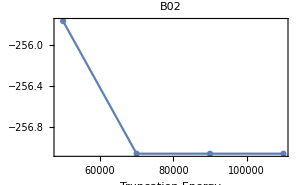
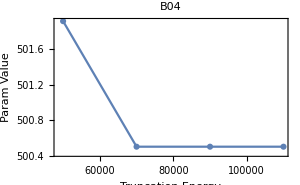
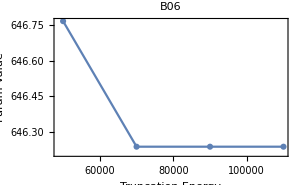
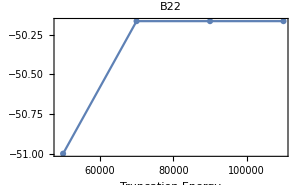
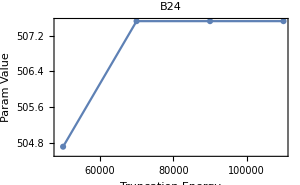
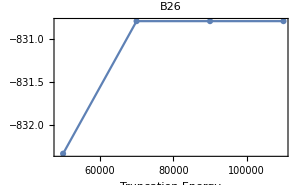
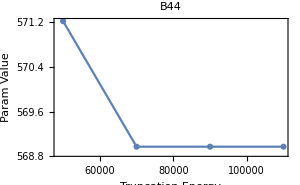
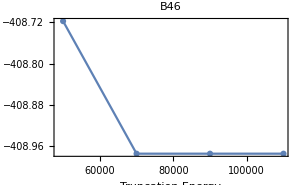
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- |  |

```mathematica
varNames=#[[1]]&/@(truncatedSols[{3,50000}]["bestParams"]);
summaryData=Transpose[Table[{trunEnergy,#[[2]]}&/@truncatedSols[{3,trunEnergy}]["bestParams"],{trunEnergy,truncationEnergies}]];
lPlots=MapIndexed[ListPlot[#1,
Joined->True,
PlotMarkers->Automatic,
PlotLabel->varNames[[#2[[1]]]],
FrameLabel->{"Truncation Energy","Param Value"},
Frame->True,ImageSize->300
]&,summaryData];
lPlots=Grid[Partition[lPlots,UpTo[3]]]
```

## Adding a constant shift. Using Carnall1989 as starting values. Using spin-spin. Varying all that was varied and fixing all that was fixed. Including Ce and Yb.

### Calculations

```mathematica
PrintAndDefine[message_]:=(
progressMessage=ToString[ln]<>": "<>message;
Print[message];
)
Off[N::preclg];
withSpinSin=1;
noconstraints=False;
filePrefix=If[withSpinSin==1,
"mirrored-constraints-with-spinspin",
"mirrored-constraints-without-spinspin"
];
σexp=2.0;
doThese=complementaryNumE;
doThese={3};
Do[(
numE=numE0;
ln=theLanthanides[[numE]];
Print[ln];
pVars=variedSymbols[ln];
constraints=caseConstraints[ln];
If[ln=="Yb",
constraints=constraints/.(lhs_->rhs_):>(lhs->-rhs)
];
If[noconstraints,
(
constraints={};
pVars=Which[
Or[ln=="Ce",ln=="Yb"],
{ζ,B02,B04,B06,B22,B24,B26,B44,B46,B66},
ln=="Pr",
{F2,F4,F6,ζ,α,β,γ,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66},
ln=="Tm",
{F2,F4,F6,ζ,α,β,γ,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66,T2},
True,
{B02,B04,B06,B22,B24,B26,B44,B46,B66,F2,F4,F6,M0,P2,T2,T3,T4,T6,T7,T8,α,β,γ,ζ}
];
)
];
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=If[OddQ[numE],
Flatten[Position[Flatten[{#,#}&/@(Last/@Carnall[carnalKey]),1],"not included"]],
Flatten[Position[Last/@Carnall[carnalKey],"not included"]]
];
independentVars=Variables[pVars/.constraints];
startValues=AssociationThread[independentVars,independentVars/.LoadParameters[ln]];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
pVars,
startValues,
σexp,
constraints,
"SaveEigenvectors"->False,
"AddConstantShift"->True,
"SignatureCheck"->False,
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->withSpinSin)),
"MaxIterations"->1000,
"MaxHistory"->1000,
"FilePrefix"->filePrefix<>"/"<>ln,
"TruncationEnergy"->60000,
"PrintFun"->PrintAndDefine]
),
{numE0, doThese}
];
```

Nd

Determining gaps in the data ...

Simplifying using the aggregate set of simplification rules ...

Zeroing out every symbol in the Hamiltonian that is not a free-ion parameter ...

Grabbing the diagonal blocks of the Hamiltonian ...

Simplifying the diagonal blocks to only keep the free ion symbols ...

Contracting the basis vectors by removing the MJ quantum numbers from the diagonal blocks ...

(if the following fails, it might help to see if the arguments of TheIntermediateEigensystems match the ones shown above)

Compiling functions for the diagonal blocks of the Hamiltonian ...

Computing the block structure of the change of basis array ...

Changing the basis of the Hamiltonian to the intermediate coupling basis ...

Distributing products inside of symbolic matrix elements to keep complexity in check ...

Distributing products inside of symbolic matrix elements to keep complexity in check ...

Truncating the Hamiltonian ...

Saving the truncated intermediate basis ...

Compiling a function for the truncated Hamiltonian ...

Saving the compiled function for the truncated Hamiltonian and the truncated intermediate basis ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Determining the free variables after constraints ...

Adding a constant shift to the fitting parameters ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/mirrored-constraints-with-spinspin/Nd-sols-1ca950d8-40c3-43a4-b805-37556cfd20c7.m

Finished ...

```mathematica
sol["bestParamsWithConstraints"]
```

<|B02→-255.761,B04→501.913,B06→646.767,B22→-50.9973,B24→504.709,B26→-832.339,B44→571.221,B46→-408.718,B66→-832.194,F2→73028.7,F4→52776.3,F6→35757.4,M0→2.15985,P2→211.293,T2→293.292,T3→35.7242,T4→59.8811,T6→-288.203,T7→339.324,T8→305.232,α→21.3669,β→-589.276,γ→1431.33,ζ→885.133,ϵ→-4.75331|>

### Plots

```mathematica
ToSubSup[symbol_]:={
{x1,x2,x3}=Characters[ToString[symbol]];
Subsuperscript[x1,x2,x3]
}
FormatWithUncertainty[{val_,delta_}]:=(
FWUtemplate=StringTemplate["`val`±`delta`"];
FWUtemplate[<|"val"->val,"delta"->delta|>]
);
CopyToPdf[expr_,name_]:=(
exportFname="/Users/juan/Temp/"<>name<>".pdf";
Export[exportFname,expr];
command="/Users/juan/Scripts/copy2clip "<>exportFname;
Print[command];
Run[command]
);
allVars={F2,F4,F6,ζ,α,β,γ,T2,T3,T4,T6,T7,T8,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66,ϵ};
billsσ=<|"Ce"->51,"Pr"->16,"Nd"->14,"Pm"->0,"Sm"->13,"Eu"->16,"Gd"->10,"Tb"->12,"Dy"->12,"Ho"->10,"Er"->19,"Tm"->10,"Yb"->38|>;
billsn=<|"Ce"->7,"Pr"->75,"Nd"->146,"Pm"->0,"Sm"->232,"Eu"->29,"Gd"->70,"Tb"->146,"Dy"->198,"Ho"->204,"Er"->127,"Tm"->56,"Yb"->5|>;
```

```mathematica
filePrefix="varied-and-fixed-with-shift";
filePrefix="varied-and-fixed-with-shift-and-no-spin-spin";
filePrefix="with-spinspin";
```

```mathematica
symbolPlotsAssoc=<||>;
paramPlotsAssoc=<||>;
paramTables=<||>;
allNumCols=<||>;
Do[
(
folder=FileNameJoin[{NotebookDirectory[],"log",filePrefix}]<>"/*.m";
fnames=FileNames[folder];
fnames=Association@Table[(
ln=StringSplit[StringSplit[fname,"/"][[-1]],"-"][[1]];
ln->Import[fname]
),{fname,fnames}];
fnames=Association[SortBy[Normal[fnames],Position[theLanthanides,#[[1]]][[1]]&]];
empty="---";
numCols={};
billsCols={};
comboCols={};
paramTable=Transpose@Table[
solwithDelta=fnames[ln]["solWithUncertainty"];
numE=Position[theLanthanides,ln][[1,1]];
thisCol=(If[Length[#]>0,
FormatWithUncertainty[
RoundValueWithUncertainty[#[[1]],#[[2]],"SetPrecision"->True]],#]&/@(allVars/.solwithDelta));
numCol=(allVars/.solwithDelta);
numCol=(If[Length[#]>0,
Around[#[[1]],#[[2]]],0]&/@(allVars/.solwithDelta));

thisCol=If[StringQ[#],#,""]&/@thisCol;
thisCol=Append[thisCol,Round[fnames[ln]["bestRMS"],1]];
thisCol=Append[thisCol,Round[billsσ[ln],1]];
thisCol=Join[thisCol,{Round[fnames[ln]["fittedLevels"]/If[OddQ[numE],2,1]],billsn[ln]}];
constrained=caseConstraints[ln];
thisColCon=(allVars/.constrained)/.fnames[ln]["bestParams"];
thisColCon=If[NumericQ[#],Style["["<>ToString[#]<>"]",Blue],""]&/@thisColCon;
thisColCon=Join[thisColCon,{"","","",""}];
thisColCon[[-5]]=ToString[Round[Last[(allVars/.constrained)/.fnames[ln]["bestParams"]],0.1]];
finalCol=If[Not[#[[1]]==""],Row[{#[[1]]}],Row[{#[[2]]}]]&/@Transpose[{thisCol,thisColCon}];

billCol=allVars/.LoadParameters[ln,"With Uncertainties"->True];
billsCols=Append[billsCols,billCol[[;;-2]]];
comboCol={ln,#}&/@allVars[[;;-2]];
comboCols=Append[comboCols,comboCol];

numCol=(numCol+((allVars/.constrained)/.fnames[ln]["bestParams"]));
numCol=If[Or[NumericQ[#],Head[#]===Around],#/2,Null]&/@numCol;
numCol=If[Head[#]===Around,#,#*2]&/@numCol;
numCol=If[Not@FreeQ[#,Null],Null,#]&/@numCol;
numCol=Join[numCol,{fnames[ln]["fittedLevels"],fnames[ln]["bestRMS"]}];
numCols=Append[numCols,numCol];

Map[If[#===Row[{""}],empty,#]&,finalCol]
,
{ln,Keys[fnames]}];
paramTables[filePrefix]=paramTable;
numCols=Transpose[numCols];
comboCols=Transpose[comboCols];
billsCols=Transpose[billsCols];
tabled=TableForm[paramTable,TableHeadings->{Join[allVars,{"σ","σBill","n","nBill"}],Keys[fnames]}];

div=(billsCols/numCols[[;;-4]]);
div=Map[If[Or[#===0.,#===1.],1,#]&,div,{2}];
divNums=Flatten[div];
div=Prepend[div,Keys[fnames]];
div=Transpose[Prepend[Transpose[div],Join[{""},allVars[[;;-2]]]]];
divTable=Framed[TextGrid[div,Dividers->{{2->Black},{2->Black}},Alignment->Center]];
diVV=Map[If[Head[#]===Around,#["Value"],#]&,div[[2;;,2;;]],{2}];
diVplot=ArrayPlot[diVV,Mesh->All,ColorFunction->"SunsetColors",PlotLegends->Automatic,ImageSize->400,Epilog->{MapIndexed[Text[#1,{0.5+#2[[1]]-1,24.5}]&,theLanthanides],
MapIndexed[Text[#1,{-0.5,24.5-#2[[1]]}]&,allVars[[;;-2]]]
},PlotRangePadding->{{2,2}}];

slashPlots=Table[Framed[
ListPlot[numCols[[idx]],Frame->True,FrameLabel->{"Ln",Row[{allVars[[idx]]," / cm^-1"}]},FrameTicks->{Transpose[{Range[Length[theLanthanides]],theLanthanides}],Automatic},Joined->True,FrameStyle->Directive[15,Bold],PlotStyle->Darker[Hue[Length[allVars]/idx]],PlotMarkers->Automatic,Background->White,PlotRange->{{0.9,13.1},All},ImageSize->700,Axes->None,PlotLabel->Style[ToString[allVars[[idx]]]<>"\n",20]],FrameMargins->60,FrameStyle->White,Background->White],{idx,1,Length[allVars]}];
paramGrid=Transpose[Prepend[Transpose[Prepend[paramTable,Keys[fnames]]],Join[{""},allVars,{"σ","σBill","n","nBill"}]]];
paramGrid[[2;;Length[allVars]+1,1]]=Table[Tooltip[allVars[[idx]],slashPlots[[idx]]],{idx,1,Length[allVars]}];
betterTable=Framed[TextGrid[paramGrid,Dividers->{{2->Black},{2->Black,-5->Black,-3->Black}},Spacings->{{1,1.5},Join[{1,1.5},ConstantArray[0.25,24],{1.5,0.25,1.5,0.25}]},Alignment->Center]];
color=<|"with-spinspin"->Red,
"without-spinspin"->Blue,
"no-constraints-with-spinspin"->Orange,
"no-constraints-without-spinspin"->Purple|>[filePrefix];
legend=<|"with-spinspin"->"with-spin-spin",
"without-spinspin"->"without-spin-spin",
"no-constraints-with-spinspin"->"no-constraints-with-spinspin",
"no-constraints-without-spinspin"->"no-constraints-without-spinspin"
|>[filePrefix];
paramPlots=Table[ListPlot[100*fun/@Abs[diVV-1],AspectRatio->1/5,ImageSize->1000,Filling->Axis,FrameLabel->{None,Row[{fun," / %"}]},PlotLabel->fun,Frame->True,PlotMarkers->"OpenMarkers",PlotStyle->color,PlotLegends->Style[legend,color],PlotRange->{All,{0,<|Max->100,Mean->10|>[fun]}},FrameTicks->{Transpose[{Range[1,Length[allVars[[;;-2]]]],allVars[[;;-2]]}],Automatic}],{fun,{Max,Mean}}];

allNumCols[filePrefix]=numCols;

symbolPlots=Table[
ListPlot[100*fun/@Abs[Transpose[diVV]-1],PlotLabel->fun,AspectRatio->1/5,ImageSize->1000,Filling->Axis,Frame->True,FrameLabel->{None,Row[{fun," / %"}]},PlotMarkers->"OpenMarkers",PlotRange->{{0.9,13.1},{0,<|Max->100,Mean->20|>[fun]}},FrameTicks->{Transpose[{Range[1,Length[theLanthanides]],theLanthanides}],Automatic},PlotStyle->color,PlotLegends->Style[legend,color]],{fun,{Max,Mean}}];
symbolPlotsAssoc[filePrefix]=symbolPlots;
paramPlotsAssoc[filePrefix]=paramPlots;
interestingRatios=Select[Sort[divNums],Not[#===1]&];
ratioPlot={ListPlot[interestingRatios,PlotRange->{All,{0.6,1.4}},AspectRatio->1/6,ImageSize->1000,Frame->True,FrameLabel->{"Ratio Index","Ratio"},Epilog->{Red,Dashed,Line[{{0,1},{200,1}}]}]};
bigCol=Column[Join[{betterTable},{divTable},{diVplot},paramPlots,symbolPlots,ratioPlot],Alignment->Center];
bigCol=Framed[Labeled[Framed[bigCol,FrameMargins->30,Background->White,FrameStyle->White],filePrefix,Top],FrameMargins->30,Background->White,FrameStyle->White];
CopyToPdf[bigCol,filePrefix]
),{filePrefix,{"with-spinspin",
"without-spinspin",
"no-constraints-with-spinspin",
"no-constraints-without-spinspin"}}
]
```

/Users/juan/Scripts/copy2clip /Users/juan/Temp/with-spinspin.pdf

/Users/juan/Scripts/copy2clip /Users/juan/Temp/without-spinspin.pdf

/Users/juan/Scripts/copy2clip /Users/juan/Temp/no-constraints-with-spinspin.pdf

/Users/juan/Scripts/copy2clip /Users/juan/Temp/no-constraints-without-spinspin.pdf

```mathematica
aFun=Which[
#===0.,
"",
Head[#]===Around,
ToString[#["Value"]]<>"("<>ToString[#["Uncertainty"]]<>")",
True,
"["<>ToString[Round[#,1]]<>"]"]&;
texTable=Map[aFun,billsCols,{2}];
trionRow=("\trion{"<>#<>"}")&/@theLanthanides;
trionRow=ToString/@theLanthanides;
texTable=Prepend[texTable,trionRow];
texTable=Transpose[texTable];
texTable=Prepend[texTable,Prepend[ToString/@allVars[[;;-2]],""]];
TableForm[Transpose[texTable]]//CopyToClipboard
```

```mathematica
stringTable=ToString[TeXForm[Transpose[texTable]]];
```

```mathematica
stringTable=StringReplace[stringTable,{".("->"(",".)"->")"}];
```

```mathematica
CopyToClipboard[stringTable]
```

```mathematica
Rasterize@Show[paramPlotsAssoc[[1]][[2]],paramPlotsAssoc[[2]][[2]]]
```

-Graphics-

```mathematica
Rasterize@Show[symbolPlotsAssoc[[1]][[2]],symbolPlotsAssoc[[2]][[2]]]
```

-Graphics-

```mathematica
yesSS=allNumCols["with-spinspin"][[;;-4]];
noSS=allNumCols["without-spinspin"][[;;-4]];
```

```mathematica
yesSS/noSS
```

{{1,0.999940.00028,1.000050.00016,1.,1.000030.00033,0.999620.00026,1.000150.00010,0.999030.00019,0.99950.0004,1.000070.00024,0.999990.00015,1.000180.00020,1},{1,1.00080.0011,0.99990.0006,1.,1.00030.0004,0.999621,1.00015,0.999031,0.99950.0004,0.99970.0005,1.00090.0005,1.00100.0009,1},{1,0.99990.0013,1.00010.0011,1.,1.00030.0004,0.999621,0.999990.00025,0.998810.00027,0.99880.0004,1.00010.0008,1.00090.0008,1.00210.0011,1},{1.00000.0017,0.99800.0010,0.99970.0007,1.,0.99920.0006,0.99600.0011,1.00160.0017,0.99830.0010,0.99800.0005,0.99880.0004,0.999600.00033,0.999650.00031,0.99580.0004},{1,0.9980.012,0.9990.006,1.,1.0020.005,1.,0.9950.005,0.9900.005,1.0010.007,1.0050.008,1.0000.008,0.9820.010,1},{1,0.9910.020,0.9990.016,1.,1.0120.007,1.,1.,0.9420.005,1.0070.008,1.0060.010,1.0100.016,0.9880.021,1},{1,0.9990.010,0.9990.005,1.,1.,1.,1.,1.,1.01260.0021,1.,1.,1.,1},{1,1,1.0000.012,1.,1.,1.,1.,1.,0.9880.011,1.,1.,1.,1},{1,1,1.010.18,1.,1.,1.,1.,1.,1.20.5,1.020.17,0.990.16,1,1},{1,1,1.010.10,1.,1.,1.,1.,1.,1.30.5,1.010.06,1.060.11,1,1},{1,1,1.000.05,1.,1.000.07,1.,1.,0.900.08,0.950.09,0.980.14,1.010.06,1,1},{1,1,1.000.05,1.,1.000.05,1.,1.,0.960.06,1.020.06,1.070.11,1.030.06,1,1},{1,1,1.000.05,1.,1.000.04,1.,1.,1.060.04,1.030.06,1.020.04,1.010.06,1,1},{1,0.880.10,0.990.04,1.,0.9590.017,1.,0.8530.018,0.9630.026,0.9440.014,0.9870.023,1.0020.027,1.020.05,1},{1,0.580.32,1.000.06,1.,0.9380.033,1.,0.7540.026,0.890.04,0.8890.018,0.9360.024,1.0100.025,0.970.04,1},{1.,1.000.07,1.000.14,1.,1.010.12,1.010.23,1.,0.970.13,1.000.09,1.,1.000.10,1.020.09,1.},{1.,0.9990.033,1.000.28,1.,1.00.4,1.000.20,1.,0.990.12,1.120.12,0.970.14,1.00.4,1.000.11,1.},{1.,1.000.05,0.990.05,1.,0.980.17,1.000.15,1.,1.030.28,0.480.14,0.970.19,0.990.12,1.010.15,1.},{1.,1.000.14,1.00.4,1.,1.,1.,1.,1.00.4,1.020.18,1.050.22,0.990.24,0.990.14,1.},{1.,1.000.09,0.990.12,1.,1.000.06,1.,1.,0.990.20,0.670.17,1.020.18,1.000.19,0.990.10,1.},{1.,1.000.04,1.000.04,1.,0.990.09,1.,1.,1.000.08,1.130.07,1.010.08,1.0050.032,0.9870.031,1.},{1.,1.000.04,1.000.06,1.,1.000.11,1.,1.,1.010.06,1.030.05,1.020.07,1.020.19,1.000.07,1.},{1.,1.010.06,1.000.08,1.,1.010.17,1.,1.,1.010.25,0.640.27,1.010.14,1.000.12,0.980.17,1.},{1.,1.000.06,0.9990.033,1.,0.990.08,1.,1.,1.010.13,0.990.06,0.990.04,0.9920.031,1.000.05,1.}}

```mathematica
aPlot=ArrayPlot[Map[If[Head[#]===Around,#["Value"],#]&,yesSS/noSS,{2}],Mesh->All,ColorFunction->"SunsetColors",PlotLegends->Automatic,ImageSize->400,
Epilog->{MapIndexed[Text[#1,{0.5+#2[[1]]-1,24.5}]&,theLanthanides],
MapIndexed[Text[#1,{-0.5,24.5-#2[[1]]}]&,allVars[[;;-2]]]
},PlotRangePadding->{{2,2}}]
```

-Graphics-

```mathematica
CopyToPdf[aPlot,"aPlot"]
```

/Users/juan/Scripts/copy2clip /Users/juan/Temp/aPlot.pdf

256

```mathematica
Transpose[yesSS/noSS]
```

{{1,0.999940.00028,1.000050.00016,1.,1.000030.00033,0.999620.00026,1.000150.00010,0.999030.00019,0.99950.0004,1.000070.00024,0.999990.00015,1.000180.00020,1},{1,1.00080.0011,0.99990.0006,1.,1.00030.0004,0.999621,1.00015,0.999031,0.99950.0004,0.99970.0005,1.00090.0005,1.00100.0009,1},{1,0.99990.0013,1.00010.0011,1.,1.00030.0004,0.999621,0.999990.00025,0.998810.00027,0.99880.0004,1.00010.0008,1.00090.0008,1.00210.0011,1},{1.00000.0017,0.99800.0010,0.99970.0007,1.,0.99920.0006,0.99600.0011,1.00160.0017,0.99830.0010,0.99800.0005,0.99880.0004,0.999600.00033,0.999650.00031,0.99580.0004},{1,0.9980.012,0.9990.006,1.,1.0020.005,1.,0.9950.005,0.9900.005,1.0010.007,1.0050.008,1.0000.008,0.9820.010,1},{1,0.9910.020,0.9990.016,1.,1.0120.007,1.,1.,0.9420.005,1.0070.008,1.0060.010,1.0100.016,0.9880.021,1},{1,0.9990.010,0.9990.005,1.,1.,1.,1.,1.,1.01260.0021,1.,1.,1.,1},{1,1,1.0000.012,1.,1.,1.,1.,1.,0.9880.011,1.,1.,1.,1},{1,1,1.010.18,1.,1.,1.,1.,1.,1.20.5,1.020.17,0.990.16,1,1},{1,1,1.010.10,1.,1.,1.,1.,1.,1.30.5,1.010.06,1.060.11,1,1},{1,1,1.000.05,1.,1.000.07,1.,1.,0.900.08,0.950.09,0.980.14,1.010.06,1,1},{1,1,1.000.05,1.,1.000.05,1.,1.,0.960.06,1.020.06,1.070.11,1.030.06,1,1},{1,1,1.000.05,1.,1.000.04,1.,1.,1.060.04,1.030.06,1.020.04,1.010.06,1,1},{1,0.880.10,0.990.04,1.,0.9590.017,1.,0.8530.018,0.9630.026,0.9440.014,0.9870.023,1.0020.027,1.020.05,1},{1,0.580.32,1.000.06,1.,0.9380.033,1.,0.7540.026,0.890.04,0.8890.018,0.9360.024,1.0100.025,0.970.04,1},{1.,1.000.07,1.000.14,1.,1.010.12,1.010.23,1.,0.970.13,1.000.09,1.,1.000.10,1.020.09,1.},{1.,0.9990.033,1.000.28,1.,1.00.4,1.000.20,1.,0.990.12,1.120.12,0.970.14,1.00.4,1.000.11,1.},{1.,1.000.05,0.990.05,1.,0.980.17,1.000.15,1.,1.030.28,0.480.14,0.970.19,0.990.12,1.010.15,1.},{1.,1.000.14,1.00.4,1.,1.,1.,1.,1.00.4,1.020.18,1.050.22,0.990.24,0.990.14,1.},{1.,1.000.09,0.990.12,1.,1.000.06,1.,1.,0.990.20,0.670.17,1.020.18,1.000.19,0.990.10,1.},{1.,1.000.04,1.000.04,1.,0.990.09,1.,1.,1.000.08,1.130.07,1.010.08,1.0050.032,0.9870.031,1.},{1.,1.000.04,1.000.06,1.,1.000.11,1.,1.,1.010.06,1.030.05,1.020.07,1.020.19,1.000.07,1.},{1.,1.010.06,1.000.08,1.,1.010.17,1.,1.,1.010.25,0.640.27,1.010.14,1.000.12,0.980.17,1.},{1.,1.000.06,0.9990.033,1.,0.990.08,1.,1.,1.010.13,0.990.06,0.990.04,0.9920.031,1.000.05,1.},{1.,-6.63228,14.1961,-23.6277,2.87712,0.987057,1.08587,1.56975,6.74129,3.65463,1.8896,1.74019,-1.2672},{1,1,1,1,1,1,1,1,1,1,1,1,1},{1.,1.04084,1.00673,2.66155,1.04791,1.03451,1.0158,1.01353,0.961066,0.969446,0.952266,1.11466,1.84971}}

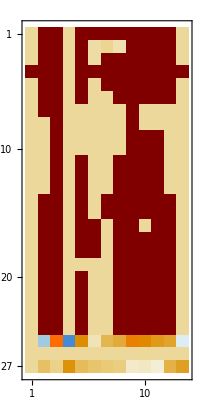

```mathematica
MatrixPlot[Transpose[yesSS/noSS]]
```

```mathematica
yesSS[[3]]/noSS[[3]]
```

{1.000050.00016,0.99990.0006,1.00010.0011,0.99970.0007,0.9990.006,0.9990.016,0.9990.005,1.0000.012,1.010.18,1.010.10,1.000.05,1.000.05,1.000.05,0.990.04,1.000.06,1.000.14,1.000.28,0.990.05,1.00.4,0.990.12,1.000.04,1.000.06,1.000.08,0.9990.033,14.1961,1,1.00673}

| Ce | Pr | Nd | Pm | Sm | Eu | Gd | Tb | Dy | Ho | Er | Tm | Yb
F2 | --- | 68870.±20. | 73020.±10. | [76400.] | 79700.±30. | 83110.±30. | 85630.±10. | 88960.±20. | 91870.±40. | 94550.±30. | 97570.±20. | 100110.±20. | ---
F4 | --- | 50360.±70. | 52780.±40. | [54900.] | 57240.±30. | [59262.7] | [60799.6] | [62895.6] | 64390.±30. | 66500.±40. | 67990.±40. | 69600.±90. | ---
F6 | --- | 32880.±60. | 35750.±50. | [37700.] | 40190.±20. | [42556.1] | 44790.±10. | 47240.±10. | 49310.±20. | 51890.±50. | 54130.±60. | 55910.±80. | ---
ζ | 647.±1. | 751.±1. | 885.4±0.8 | [1025.] | 1176.±1. | 1337.±2. | 1507.±3. | 1708.±2. | 1912.±1. | 2142.±1. | 2378.±1. | 2635.±1. | 2915.±1.
α | --- | 16.1±0.2 | 21.3±0.1 | [20.5] | 20.2±0.1 | [20.16] | 18.9±0.1 | 18.7±0.1 | 18.2±0.1 | 17.6±0.1 | 17.4±0.1 | 17.2±0.2 | ---
β | --- | -560.±10. | -580.±10. | [-560.] | -565.±5. | [-566.9] | [-600.] | -622.±4. | -634.±6. | -611.±8. | -580.±10. | -610.±10. | ---
γ | --- | 1360.±10. | 1430.±10. | [1475.] | [1500.] | [1500.] | [1575.] | [1650.] | 1779.±5. | [1800.] | [1800.] | [1820.] | ---
T2 | --- | --- | 293.±4. | [300.] | [300.] | [300.] | [300.] | [320.] | 319.±5. | [400.] | [400.] | [400.] | ---
T3 | --- | --- | 35.±8. | [35.] | [36.] | [40.] | [42.] | [40.] | 20.±10. | 36.±8. | 40.±10. | --- | ---
T4 | --- | --- | 59.±8. | [58.] | [56.] | [60.] | [62.] | [50.] | 70.±40. | 95.±7. | 60.±9. | --- | ---
T6 | --- | --- | -280.±20. | [-310.] | -320.±30. | [-300.] | [-295.] | -390.±40. | -310.±40. | -270.±50. | -280.±20. | --- | ---
T7 | --- | --- | 330.±20. | [350.] | 360.±20. | [370.] | [350.] | 330.±30. | 360.±20. | 280.±40. | 320.±20. | --- | ---
T8 | --- | --- | 300.±20. | [320.] | 340.±10. | [320.] | [310.] | 310.±10. | 310.±20. | 330.±20. | 360.±20. | --- | ---
M0 | --- | 2.1±0.3 | 2.1±0.1 | [2.4] | 2.62±0.06 | [2.1] | 3.9±0.1 | 2.49±0.09 | 3.41±0.07 | 2.64±0.08 | 3.8±0.1 | 3.8±0.2 | ---
P2 | --- | -60.±30. | 210.±10. | [275.] | 360.±10. | [360.] | 950.±30. | 440.±20. | 700.±10. | 590.±20. | 670.±20. | 690.±40. | ---
B02 | [-218.] | -220.±20. | -250.±40. | [-245.] | -200.±30. | -210.±60. | [-231.] | -240.±40. | -230.±20. | [-240.] | -230.±30. | -240.±30. | [-249.]
B04 | [738.] | 730.±30. | 500.±100. | [470.] | 300.±200. | 400.±100. | [604.] | 600.±100. | 500.±80. | 500.±100. | 300.±100. | 450.±60. | [457.]
B06 | [679.] | 670.±40. | 650.±40. | [640.] | 600.±100. | 500.±100. | [280.] | 300.±100. | 370.±80. | 390.±90. | 440.±70. | 300.±60. | [282.]
B22 | [-50.] | -120.±20. | -50.±30. | [-50.] | [-50.] | [-50.] | [-99.] | -90.±40. | -60.±10. | -90.±30. | -90.±30. | -100.±20. | [-105.]
B24 | [431.] | 420.±50. | 500.±80. | [525.] | 620.±50. | [597.] | [340.] | 260.±70. | 200.±100. | 240.±60. | 350.±90. | 300.±40. | [320.]
B26 | [-921.] | -910.±50. | -830.±40. | [-750.] | -690.±90. | [-706.] | [-721.] | -730.±80. | -590.±60. | -550.±60. | -480.±20. | -460.±20. | [-482.]
B44 | [616.] | 600.±30. | 560.±50. | [490.] | 430.±60. | [408.] | [452.] | 480.±30. | 530.±30. | 450.±40. | 300.±100. | 430.±40. | [428.]
B46 | [-348.] | -350.±20. | -400.±40. | [-450.] | -400.±100. | [-508.] | [-204.] | -240.±80. | -240.±90. | -200.±30. | -230.±30. | -240.±60. | [-234.]
B66 | [-788.] | -790.±60. | -830.±30. | [-760.] | -730.±80. | [-692.] | [-509.] | -510.±90. | -550.±40. | -590.±30. | -500.±20. | -490.±30. | [-492.]
ϵ | -2.9 | 0.3 | -0.3 | 0.3 | -5.7 | -12.6 | 19.2 | -3.8 | -1. | -1.3 | -3.8 | -6. | -32.8
σ | 47 | 16 | 13 | 1 | 13 | 16 | 10 | 8 | 12 | 10 | 14 | 10 | 61
σBill | 51 | 16 | 14 | 0 | 13 | 16 | 10 | 12 | 12 | 10 | 19 | 10 | 38
n | 7 | 75 | 146 | 284 | 233 | 29 | 70 | 146 | 198 | 204 | 127 | 56 | 5
nBill | 7 | 75 | 146 | 0 | 232 | 29 | 70 | 146 | 198 | 204 | 127 | 56 | 5

## Running over the Lanthanide Row, using Carnall1989 as starting values. Using spin-spin. Varying all that was varied and fixing all that was fixed. Including Ce and Yb

```mathematica
Import["inhomConstraints.m"];
```

```mathematica
filePrefix="varied-and-fixed";
filePrevix="trashcan";
σexp=2.0;
Do[(
numE=numE0;
ln=theLanthanides[[numE]];
Print[ln];
pVars=variedSymbols[ln];
constraints=caseConstraints[ln];

carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=If[OddQ[numE],
Flatten[Position[Flatten[{#,#}&/@(Last/@Carnall[carnalKey]),1],"not included"]],
Flatten[Position[Last/@Carnall[carnalKey],"not included"]]
];
independentVars=Variables[pVars/.constraints];
startValues=AssociationThread[independentVars,independentVars/.LoadParameters[ln]];
sol=FixingFit[numE,
expData,
excludedDataIndices,
pVars,
startValues,
σexp,
constraints,
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->1)),
"MaxIterations"->1000,
"MaxHistory"->1000,
"FilePrefix"->filePrefix<>"/"<>ln,
"TruncationEnergy"->50000,
"PrintFun"->Print]
),
{numE0,   {2}}
];
Run["~/Scripts/pushover done"];
```

Pr

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^2 ...

Getting reference free-ion parameters for Pr using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy,simplifier}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /Users/juan/ZiaLab/Codebase/qlanth/compiled/Pr-compiled-intermediate-truncated-ham-7085466368566688849.mx

The truncated Hamiltonian has a dimension of 91x91 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Fitting for 75 data points with 18 free parameters. The effective degrees of freedom are 57 ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Solution found in 1.22475s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/varied-and-fixed/Pr-sols-86901058-6c34-46cd-92f3-94dc47afc1df.m

```mathematica
sol
```

<|simplifier→{M2→(14 M0)/25,M4→(31 M0)/100,P4→P2/2,P6→P2/10,Bx→0,By→0,Bz→0,B12→0,B14→0,B16→0,B34→0,B36→0,B56→0,S12→0,S14→0,S16→0,S22→0,S24→0,S26→0,S34→0,S36→0,S44→0,S46→0,S56→0,S66→0,T2→0,T3→0,T4→0,T6→0,T7→0,T8→0,T11p→0,T11→0,T12→0,T14→0,T15→0,T16→0,T18→0,T17→0,T19→0,T2p→0,F0→0,P0→0,σSS→1,T11p→0,T11→0,T12→0,T14→0,T15→0,T16→0,T18→0,T17→0,T19→0,T2p→0},freeIonSymbols→{F0,F2,F4,F6,ζ},truncationEnergy→50000,numE→2,expData→{{0.,3H4,0.2},{57.,3H4,71.},{71.,3H4,95.},{136.,3H4,138.},{195.,3H4,183.},{204.,3H4,221.},{322.,3H4,333.},{,3H4,444.},{508.,3H4,463.},{,3H5,2126.},{,3H5,2158.},{2179.,3H5,2191.},{2272.,3H5,2284.},{2299.,3H5,2290.},{2304.,3H5,2295.},{2354.,3H5,2318.},{2412.,3H5,2399.},{2431.,3H5,2412.},{2457.,3H5,2438.},{2567.,3H5,2540.},{,3H6,4179.},{4223.,3H6,4200.},{4268.,3H6,4283.},{4305.,3H6,4321.},{4388.,3H6,4384.},{4440.,3H6,4467.},{,3H6,4478.},{4508.,3H6,4496.},{4529.,3H6,4508.},{4581.,3H6,4590.},{4673.,3H6,4693.},{,3H6,4712.},{4785.,3H6,4814.},{5137.,3F2,5145.},{5182.,3F2,5182.},{5201.,3F2,5185.},{5275.,3F2,5270.},{5280.,3F2,5276.},{6453.,3F3,6456.},{6495.,3F3,6490.},{6499.,3F3,6508.},{6587.,3F3,6579.},{6602.,3F3,6600.},{6622.,3F3,6628.},{6722.,3F3,6740.},{6927.,3F4,6918.},{,3F4,6936.},{6946.,3F4,6950.},{,3F4,6952.},{6946.,3F4,6953.},{6980.,3F4,6983.},{7029.,3F4,7034.},{7104.,3F4,7096.},{7165.,3F4,7152.},{9716.,1G4,9721.},{9751.,1G4,9762.},{9876.,1G4,9860.},{9912.,1G4,9927.},{,1G4,9958.},{10005.,1G4,9996.},{10042.,1G4,10030.},{10163.,1G4,10150.},{10499.,1G4,10516.},{16873.,1D2,16887.},{16893.,1D2,16895.},{17083.,1D2,17082.},{,1D2,17117.},{17183.,1D2,17170.},{20927.,3P0,20911.},{21279.,1I6,21284.},{,1I6,21304.},{21331.,1I6,21340.},{21404.,1I6,21390.},{21418.,1I6,21406.},{,1I6,21481.},{21475.,3P1,21487.},{21522.,3P1,21519.},{,1I6,21570.},{21567.,3P1,21592.},{21585.,1I6,21588.},{,1I6,21637.},{21668.,1I6,21666.},{,1I6,21804.},{21897.,1I6,21889.},{21942.,1I6,21958.},{22691.,3P2,22668.},{22714.,3P2,22704.},{22734.,3P2,22738.},{22772.,3P2,22787.},{22819.,3P2,22817.},{46965.,1S0,46965.}},problemVars→{B02,B04,B06,B22,B24,B26,B44,B46,B66,F2,F4,F6,M0,P2,α,β,γ,ζ},maxIterations→1000,hamDim→91,allVars→{B02,B04,B06,B22,B24,B26,B44,B46,B66,F2,F4,F6,M0,P2,α,β,γ,ζ},freeBies→{2,0,68878.,50347.,32901.,751.7},truncatedDim→91,fittedLevels→75,actualSteps→8,bestRMS→16.1502,solWithUncertainty→{B02→{-220.666,21.9613},B04→{734.537,34.8541},B06→{668.796,49.5284},B22→{-127.279,24.3801},B24→{421.118,52.5595},B26→{-920.465,56.7525},B44→{607.564,32.8165},B46→{-350.718,29.0123},B66→{-789.87,63.4763},F2→{68866.7,27.3857},F4→{50408.,77.2549},F6→{32887.3,61.9188},M0→{1.8707,0.331061},P2→{-40.638,36.3631},α→{16.1451,0.266032},β→{-556.991,16.1965},γ→{1363.81,19.2323},ζ→{749.718,1.01553}},paramSols→{{-221.175,734.572,669.532,-127.339,421.555,-920.137,607.29,-350.317,-789.026,68866.5,50408.6,32886.3,1.87713,-39.9822,16.1394,-556.798,1363.54,749.715},{-220.666,734.514,668.761,-127.24,421.111,-920.445,607.657,-350.683,-789.851,68866.7,50408.,32887.3,1.87068,-40.6607,16.1452,-556.999,1363.82,749.719},{-220.671,734.526,668.8,-127.276,421.124,-920.464,607.567,-350.716,-789.86,68866.7,50408.,32887.3,1.8707,-40.6346,16.1451,-556.991,1363.81,749.718},{-220.667,734.533,668.798,-127.278,421.119,-920.465,607.567,-350.72,-789.867,68866.7,50408.,32887.3,1.87071,-40.65,16.1451,-556.992,1363.81,749.719},{-220.666,734.538,668.796,-127.278,421.118,-920.465,607.565,-350.718,-789.871,68866.7,50408.,32887.3,1.87072,-40.649,16.1451,-556.991,1363.81,749.719},{-220.666,734.538,668.797,-127.279,421.118,-920.464,607.563,-350.715,-789.873,68866.7,50408.,32887.3,1.87069,-40.6338,16.1451,-556.991,1363.81,749.718},{-220.665,734.538,668.797,-127.278,421.119,-920.464,607.564,-350.717,-789.871,68866.7,50408.,32887.3,1.8707,-40.6379,16.1451,-556.991,1363.81,749.718},{-220.666,734.537,668.796,-127.279,421.118,-920.465,607.564,-350.718,-789.87,68866.7,50408.,32887.3,1.8707,-40.638,16.1451,-556.991,1363.81,749.718}},rmsHistory→{16.1516,16.1502,16.1502,16.1502,16.1502,16.1502,16.1502,16.1502},Appendix→<||>,timeTaken/s→1.22475,bestParams→{B02→-220.666,B04→734.537,B06→668.796,B22→-127.279,B24→421.118,B26→-920.465,B44→607.564,B46→-350.718,B66→-789.87,F2→68866.7,F4→50408.,F6→32887.3,M0→1.8707,P2→-40.638,α→16.1451,β→-556.991,γ→1363.81,ζ→749.718}|>

### Plots

```mathematica
ToSubSup[symbol_]:={
{x1,x2,x3}=Characters[ToString[symbol]];
Subsuperscript[x1,x2,x3]
}
FormatWithUncertainty[{val_,delta_}]:=(
FWUtemplate=StringTemplate["`val`(`delta`)"];
FWUtemplate[<|"val"->val,"delta"->delta|>]
);
allVars={F2,F4,F6,ζ,α,β,γ,T2,T3,T4,T6,T7,T8,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66};
billsσ=<|"Ce"->51,"Pr"->16,"Nd"->14,"Pm"->"","Sm"->13,"Eu"->16,"Gd"->10,"Tb"->12,"Dy"->12,"Ho"->10,"Er"->19,"Tm"->10,"Yb"->38|>;
billsn=<|"Ce"->7,"Pr"->75,"Nd"->146,"Pm"->"","Sm"->232,"Eu"->29,"Gd"->70,"Tb"->146,"Dy"->198,"Ho"->204,"Er"->127,"Tm"->56,"Yb"->5|>;
```

```mathematica
folder=FileNameJoin[{NotebookDirectory[],"log",filePrefix}]<>"/*.m";
fnames=FileNames[folder];
fnames=Association@Table[(
ln=StringSplit[StringSplit[fname,"/"][[-1]],"-"][[1]];
ln->Import[fname]
),{fname,fnames}];
fnames=Association[SortBy[Normal[fnames],Position[theLanthanides,#[[1]]][[1]]&]];
```

```mathematica
paramTable=Transpose@Table[
solwithDelta=fnames[ln]["solWithUncertainty"];
numE=Position[theLanthanides,ln][[1,1]];
{#,0}&/@Association[caseConstraints[ln]];
thisCol=(If[Length[#]>0,FormatWithUncertainty[
RoundValueWithUncertainty[#[[1]],#[[2]],"SetPrecision"->True]],#]&/@(allVars/.solwithDelta));
thisCol=If[StringQ[#],#,""]&/@thisCol;
thisCol=Append[thisCol,Round[fnames[ln]["bestRMS"],1]];
thisCol=Append[thisCol,Round[billsσ[ln],1]];
thisCol=Join[thisCol,{Round[fnames[ln]["fittedLevels"]/If[OddQ[numE],2,1]],billsn[ln]}];
constrained=caseConstraints[ln];
thisColCon=(allVars/.constrained)/.fnames[ln]["bestParams"];
thisColCon=If[NumericQ[#],Style["["<>ToString[#]<>"]",Blue],""]&/@thisColCon;
thisColCon=Join[thisColCon,{"","","",""}];
If[Not[#[[1]]==""],Row[{#[[1]]}],Row[{#[[2]]}]]&/@Transpose[{thisCol,thisColCon}]
,
{ln,Keys[fnames]}];
TableForm[paramTable,TableHeadings->{Join[allVars,{"σ","σBill","n","nBill"}],Keys[fnames]}]
```

| Pr | Nd | Sm | Eu | Gd | Tb | Dy | Ho | Er | Tm
F2 | 68860.(20.) | 73020.(30.) | 79700.(200.) | 83000.(100.) | 85640.(10.) | 88870.(20.) | 91830.(40.) | 94560.(30.) | 97570.(20.) | 100100.(100.)
F4 | 50400.(70.) | 52700.(100.) | 57200.(200.) | [59240.2] | [60809.] | [62834.6] | 64350.(30.) | 66480.(40.) | 68050.(40.) | 69600.(300.)
F6 | 32880.(60.) | 35750.(70.) | 40200.(100.) | [42539.9] | 44790.(10.) | 47190.(10.) | 49260.(20.) | 51900.(50.) | 54180.(60.) | 56000.(200.)
ζ | 749.(1.) | 885.(2.) | 1175.(7.) | 1332.(9.) | 1509.(3.) | 1705.(2.) | 1908.(1.) | 2139.(1.) | 2377.(1.) | 2634.(5.)
α | 16.1(0.2) | 21.3(0.3) | 20.3(0.5) | [20.16] | 18.8(0.1) | 18.5(0.1) | 18.2(0.1) | 17.7(0.1) | 17.4(0.1) | 16.9(0.9)
β | -550.(10.) | -580.(10.) | -570.(30.) | [-566.9] | [-600.] | -586.(4.) | -638.(6.) | -615.(8.) | -580.(10.) | -610.(50.)
γ | 1360.(10.) | 1430.(20.) | [1500.] | [1500.] | [1575.] | [1650.] | 1802.(5.) | [1800.] | [1800.] | [1820.]
T2 |  | 290.(10.) | [300.] | [300.] | [300.] | [320.] | 315.(5.) | [400.] | [400.] | [400.]
T3 |  | 30.(10.) | [36.] | [40.] | [42.] | [40.] | 30.(10.) | 36.(8.) | 40.(10.) | 
T4 |  | 50.(10.) | [56.] | [60.] | [62.] | [50.] | 90.(40.) | 96.(7.) | 63.(9.) | 
T6 |  | -280.(20.) | -330.(40.) | [-300.] | [-295.] | -350.(40.) | -290.(40.) | -260.(50.) | -280.(20.) | 
T7 |  | 330.(20.) | 360.(40.) | [370.] | [350.] | 320.(30.) | 370.(20.) | 300.(40.) | 330.(20.) | 
T8 |  | 300.(20.) | 340.(20.) | [320.] | [310.] | 330.(10.) | 320.(20.) | 340.(20.) | 360.(20.) | 
M0 | 1.8(0.3) | 2.1(0.3) | 2.5(0.5) | [2.1] | 3.3(0.1) | 2.4(0.09) | 3.22(0.06) | 2.61(0.08) | 3.8(0.1) | 3.(1.)
P2 | -30.(30.) | 210.(40.) | 300.(100.) | [360.] | 720.(40.) | 390.(20.) | 620.(10.) | 550.(20.) | 680.(20.) | 600.(100.)
B02 | -220.(20.) | -250.(40.) | -200.(200.) | -200.(100.) | [-231.] | -240.(40.) | -230.(20.) | [-240.] | -230.(30.) | -250.(50.)
B04 | 730.(30.) | 500.(100.) | 300.(400.) | 400.(100.) | [604.] | 600.(100.) | 560.(70.) | 500.(100.) | 300.(100.) | 400.(100.)
B06 | 670.(40.) | 600.(100.) | 600.(500.) | 500.(100.) | [280.] | 300.(100.) | 170.(90.) | 300.(100.) | 440.(70.) | 300.(200.)
B22 | -120.(20.) | -50.(40.) | [-50.] | [-50.] | [-99.] | -100.(50.) | -60.(10.) | -100.(20.) | -90.(30.) | -100.(40.)
B24 | 420.(50.) | 500.(100.) | 600.(300.) | [597.] | [340.] | 260.(70.) | 190.(70.) | 240.(60.) | 350.(90.) | 300.(100.)
B26 | -910.(50.) | -800.(100.) | -600.(400.) | [-706.] | [-721.] | -730.(80.) | -670.(50.) | -550.(60.) | -480.(20.) | -400.(100.)
B44 | 600.(30.) | 500.(100.) | 400.(400.) | [408.] | [452.] | 480.(30.) | 550.(30.) | 460.(40.) | 300.(100.) | 400.(100.)
B46 | -350.(20.) | -400.(100.) | -400.(400.) | [-508.] | [-204.] | -240.(80.) | -100.(100.) | -200.(30.) | -230.(30.) | -200.(200.)
B66 | -780.(60.) | -830.(80.) | -700.(400.) | [-692.] | [-509.] | -520.(90.) | -540.(40.) | -580.(30.) | -500.(20.) | -500.(100.)
σ | 16 | 14 | 21 | 22 | 10 | 9 | 11 | 9 | 14 | 17
σBill | 16 | 14 | 13 | 16 | 10 | 12 | 12 | 10 | 19 | 10
n | 75 | 146 | 233 | 29 | 70 | 146 | 198 | 204 | 127 | 56
nBill | 75 | 146 | 232 | 29 | 70 | 146 | 198 | 204 | 127 | 56

## Running over the Lanthanide Row, using Carnall1989 as starting values. Using spin-spin. Varying F2,F4,F6,ζ,α,β,γ,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66

```mathematica
filePrefix="carnall-all-params";
Do[(
cfVars={F2,F4,F6,ζ,α,β,γ,M0,P2,B02,B04,B06,B22,B24,B26,B44,B46,B66};
numE=numE0;
σexp=2.0;
ln=theLanthanides[[numE]];
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=Flatten[Position[Last/@Carnall[carnalKey],"not included"]];
problemVars=cfVars;
startValues=problemVars/.LoadParameters[ln];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
problemVars,
startValues,
σexp,
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->1)),
"MaxIterations"->1000,
"MaxHistory"->1000,
"FilePrefix"->filePrefix<>"/"<>ln,
"TruncationEnergy"->50000,
"PrintFun"->Print]
),
{numE0,  {2,12,3,11,4,10,5,9,6,8,7}}
];
Run["~/Scripts/pushover done"];
```

```mathematica
ResourceFunction["DarkMode"][False]
```

### Plots

```mathematica
ToSubSup[symbol_]:={
{x1,x2,x3}=Characters[ToString[symbol]];
Subsuperscript[x1,x2,x3]
}
FormatWithUncertainty[{val_,delta_}]:=(
FWUtemplate=StringTemplate["`val`±`delta`"];
FWUtemplate[<|"val"->val,"delta"->delta|>]
)
```

```mathematica
folder=FileNameJoin[{NotebookDirectory[],"log",filePrefix}]<>"/*.m";
```

```mathematica
fnames=FileNames[folder];
fnames=Association@Table[(
ln=StringSplit[StringSplit[fname,"/"][[-1]],"-"][[1]];
ln->Import[fname]
),{fname,fnames}];
fnames=Association[SortBy[Normal[fnames],Position[theLanthanides,#[[1]]][[1]]&]];
```

```mathematica
fittedSymbols=fnames["Pr"]["problemVars"];
```

```mathematica
billsσ=Association@@{"Pr"->16,"Nd"->14,"Pm"->"","Sm"->13,"Eu"->16,"Gd"->10,"Tb"->12,"Dy"->12,"Ho"->10,"Er"->19,"Tm"->10};
```

```mathematica
bills=Transpose[Table[fittedSymbols/.LoadParameters[ln],{ln,Keys[fnames]}]];
```

```mathematica
valsWithσ=<||>;
roundedTable=Table[(
sol=fnames[ln];
fitted={#[[1]],#[[2]]}&/@sol["solWithUncertainty"];
fittedSymbols=First/@fitted;
fittedValues=Last/@fitted;
valsWithσ[ln]=Map[RoundValueWithUncertainty@@#&,fittedValues];
fittedValues=Table[FormatWithUncertainty[RoundValueWithUncertainty[val[[1]],val[[2]],"SetPrecision"->True]],{val,fittedValues}];
σBest=Round[sol["rmsHistory"][[-1]],1.];
fittedSymbols=Join[fittedSymbols,{σ,SuperStar[σ]}];
Join[fittedValues,{ToString[σBest],billsσ[ln]}]
),{ln,Keys[fnames]}];
TableForm[Transpose[roundedTable],TableHeadings->{Row[{#," / cm^-1"}]&/@fittedSymbols,Keys[fnames]}]
```

| Pr | Nd | Pm | Sm | Eu | Gd | Tb | Dy | Ho | Er | Tm
F2 / cm^-1 | 68860.±20. | 73010.±10. | 76400.±30. | 79450.±30. | 90800.±200. | 87900.±20. | 89090.±50. | 91860.±40. | 94490.±30. | 97860.±20. | 100350.±20.
F4 / cm^-1 | 50400.±70. | 52720.±40. | 55060.±40. | 56650.±30. | 106520.±40. | 67300.±20. | 63200.±20. | 64390.±30. | 66330.±40. | 69280.±40. | 70230.±90.
F6 / cm^-1 | 32880.±60. | 35740.±50. | 37760.±50. | 39740.±20. | 53370.±20. | 45910.±10. | 47470.±10. | 49410.±20. | 51860.±50. | 55360.±60. | 56780.±80.
ζ / cm^-1 | 749.±1. | 885.3±0.8 | 1022.±1. | 1173.±1. | 1351.±2. | 1491.±3. | 1707.±2. | 1907.±1. | 2139.±1. | 2374.±1. | 2634.±1.
α / cm^-1 | 16.1±0.2 | 21.3±0.1 | 20.7±0.2 | 19.4±0.1 | 436.±1. | 35.1±0.1 | 19.3±0.1 | 18.4±0.1 | 17.5±0.1 | 17.8±0.1 | 16.7±0.2
β / cm^-1 | -550.±10. | -590.±10. | -567.±8. | -552.±5. | 18762.±7. | 197.±3. | -624.±4. | -638.±6. | -618.±8. | -590.±10. | -600.±10.
γ / cm^-1 | 1360.±10. | 1440.±10. | 1444.±8. | 1694.±4. | -27732.±7. | -814.±2. | 1530.±3. | 1775.±5. | 1838.±9. | 1410.±10. | 1600.±20.
M0 / cm^-1 | 1.8±0.3 | 2.1±0.1 | 2.33±0.07 | 2.59±0.06 | -7.6±0.1 | 2.0±0.1 | 2.5±0.09 | 3.32±0.06 | 2.51±0.08 | 3.5±0.1 | 3.9±0.2
P2 / cm^-1 | -40.±30. | 190.±10. | 280.±10. | 350.±10. | -2280.±30. | 160.±40. | 440.±20. | 640.±10. | 530.±20. | 550.±20. | 710.±40.
B02 / cm^-1 | -220.±20. | -250.±40. | -200.±100. | -200.±30. | -210.±60. | -230.±70. | -230.±40. | -240.±20. | -220.±50. | -230.±30. | -250.±30.
B04 / cm^-1 | 730.±30. | 500.±100. | 460.±90. | 400.±100. | 400.±100. | 600.±300. | 640.±90. | 500.±80. | 500.±100. | 300.±100. | 450.±60.
B06 / cm^-1 | 660.±40. | 620.±50. | 630.±70. | 600.±100. | 500.±100. | 0±300. | 300.±100. | 360.±80. | 300.±100. | 430.±70. | 290.±60.
B22 / cm^-1 | -120.±20. | -50.±30. | -50.±50. | -30.±50. | -50.±40. | -50.±50. | -100.±50. | -60.±20. | -100.±20. | -90.±30. | -100.±20.
B24 / cm^-1 | 420.±50. | 510.±90. | 520.±60. | 570.±50. | 400.±100. | 300.±300. | 260.±70. | 300.±100. | 240.±60. | 360.±90. | 300.±40.
B26 / cm^-1 | -920.±50. | -840.±40. | -730.±20. | -700.±90. | -710.±90. | -1000.±100. | -720.±80. | -600.±50. | -550.±60. | -480.±20. | -440.±20.
B44 / cm^-1 | 600.±30. | 550.±50. | 480.±50. | 380.±60. | 460.±70. | 400.±200. | 460.±30. | 520.±40. | 460.±40. | 300.±100. | 430.±40.
B46 / cm^-1 | -350.±20. | -400.±40. | -440.±60. | -500.±100. | -500.±100. | 300.±200. | -250.±80. | -250.±90. | -190.±30. | -230.±30. | -240.±60.
B66 / cm^-1 | -780.±60. | -820.±30. | -740.±20. | -700.±90. | -480.±90. | -700.±100. | -520.±90. | -530.±40. | -570.±30. | -500.±20. | -490.±30.
σ / cm^-1 | 16. | 13. | 4. | 13. | 10. | 4. | 9. | 12. | 9. | 15. | 11.
σ^* / cm^-1 | 16 | 14 |  | 13 | 16 | 10 | 12 | 12 | 10 | 19 | 10

```mathematica
sorter=fittedSymbols;
```

```mathematica
Length[fittedSymbols]
```

20

```mathematica
rowSlashWithUncertainty=Transpose[Table[Around[#[[1]],#[[2]]]&/@row,{row,Values[valsWithσ]}]];
```

```mathematica
rowSlash=Transpose[Table[First/@row,{row,Values[valsWithσ]}]];
fig2=ListPlot[rowSlashWithUncertainty,
FrameTicks->{Transpose[{Range[1,11],Keys[fnames]}],Automatic},
Frame->True,
FrameLabel->{"","B_q^(k) / cm^-1"},
PlotLegends->fittedSymbols[[;;-3]],
Joined->True,
PlotMarkers->Automatic,
ImageSize->800,
FrameStyle->Directive[Black,15],
PlotLabel->Style["Crystal field parameters in LaF_3 (start Morrison)\n",20,Black],
PlotRange->{{0.9,8.1},{-1000,1000}},
FrameStyle->Directive[15]];
fig2=ColorNegate[Rasterize[Framed[fig2,FrameMargins->40,FrameStyle->White]]]
(*fig2//CopyToClipboard*)
```

-Graphics-

```mathematica
figs=Table[
p=ListPlot[
{((#[[1]]-#[[2]])&)/@rowSlashWithUncertainty[[idx]],
((#[[1]]+#[[2]])&)/@rowSlashWithUncertainty[[idx]]
},
Joined->True,
FrameTicks->{
Transpose[{Range[1,Length[fnames]],Keys[fnames]}],
Automatic},
PlotStyle->Hue[Length[fittedSymbols]/idx],
Filling->{1->{2}},
ImageSize->800,
Frame->True,
PlotRange->{{0.9,8.1},All},
FrameStyle->Directive[Black,15],
FrameLabel->{"",Row[{fittedSymbols[[idx]]," / cm^-1"}]},
Epilog->{Point/@(Transpose[{Range[1,11],bills[[idx]]}]),
{Dotted,Line[(Transpose[{Range[1,11],bills[[idx]]}])]}
}
],
{idx,1,Length[rowSlashWithUncertainty]}];
figs=ColorNegate[Rasterize[Framed[#,FrameMargins->40,FrameStyle->White],ImageResolution->100]]&/@figs;
imDims=ImageDimensions[figs[[1]]];
```

```mathematica
figs=ImageResize[#,imDims]&/@figs;
figs=PadRight[figs,20,ImageResize[Image[{{0,0},{0,0}}],ImageDimensions[figs[[1]]]]];
figs=Partition[figs,4];
```

```mathematica
Export["~/temp/panel2.jpg",ImagePad[ImageAssemble[figs],100,Black]]
```

~/temp/panel2.jpg

```mathematica
fig3=ListPlot[bills,FrameTicks->{Transpose[{Range[1,Length[fnames]],Keys[fnames]}],Automatic},Frame->True,
FrameLabel->{"","B_q^(k) / cm^-1"},
PlotLegends->Flatten[ToSubSup/@fittedSymbols[[;;9]]],
Joined->True,
PlotMarkers->Automatic,
ImageSize->800,
FrameStyle->Directive[Black,15],
PlotLabel->Style["Crystal field parameters in LaF_3 (Carnall)\n",20,Black],
PlotRange->{{0.9,8.1},{-1000,1000}},FrameStyle->Directive[15]];
fig3=ColorNegate[Rasterize[Framed[fig3,FrameMargins->40,FrameStyle->White]]]
```

-Graphics-

```mathematica
Export["~/clyde-vs-bill.gif",Rasterize/@Table[Show[{fig2,fig3}[[Mod[i,2,1]]],ImageSize->800],{i,1,2,1}],"DisplayDurations"->2]
```

~/clyde-vs-bill.gif

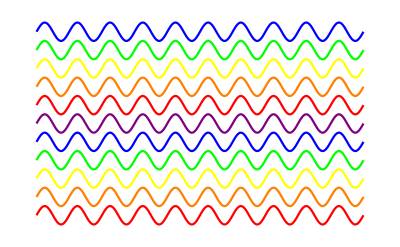

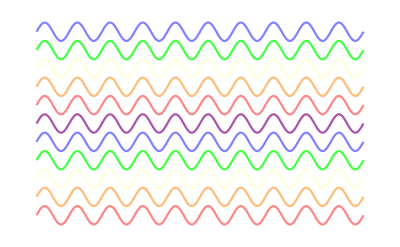

```mathematica
ms={-5,-4,-3,-2,-1,0,1,2,3,4,5};
colors={Red,Orange,Yellow,Green,Blue,Purple};
dimcolors=({Opacity[RandomReal[{0,0.75}]],#}&/@colors);
funs=Table[{0.5Sin[x]+m},{m,ms}];
Plot[funs,{x,0,20π},Axes->None,PlotStyle->colors]
Plot[funs,{x,0,20π},Axes->None,PlotStyle->dimcolors]
```

## Running over the Lanthanide Row, using Carnall1989 as starting values. Using spin-spin.

```mathematica
ResourceFunction["DarkMode"][True]
```

```mathematica
filePrefix="carnall-with-spin-spin";
Do[(
cfVars={B02,B04,B06,B22,B24,B26,B44,B46,B66};
numE=numE0;
σexp=2.0;
ln=theLanthanides[[numE]];
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=Flatten[Position[Last/@Carnall[carnalKey],"not included"]];
problemVars=cfVars;
startValues=problemVars/.LoadParameters[ln];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
problemVars,
startValues,
σexp,
"OtherSimplifier"->(("OtherSimplifier"/.Options[ClassicalFit])/.(σSS->_):> (σSS->1)),
"MaxIterations"->1000,
"MaxHistory"->1000,
"FilePrefix"->filePrefix<>"/"<>ln,
"TruncationEnergy"->50000,
"PrintFun"->PrintTemporary]
),
{numE0, {2,12,3,11,4,10,5,9,6,8,7}}
];
Run["~/Scripts/pushover done"];
```

### Plots

```mathematica
ToSubSup[symbol_]:={
{x1,x2,x3}=Characters[ToString[symbol]];
Subsuperscript[x1,x2,x3]
}
FormatWithUncertainty[{val_,delta_}]:=(
FWUtemplate=StringTemplate["`val`±`delta`"];
FWUtemplate[<|"val"->val,"delta"->delta|>]
)
```

```mathematica
folder=FileNameJoin[{NotebookDirectory[],"log",filePrefix}]<>"/*.m";
```

```mathematica
fnames=FileNames[folder];
fnames=Association@Table[(
ln=StringSplit[StringSplit[fname,"/"][[-1]],"-"][[1]];
ln->Import[fname]
),{fname,fnames}];
fnames=Association[SortBy[Normal[fnames],Position[theLanthanides,#[[1]]][[1]]&]];
```

```mathematica
fittedSymbols=fnames["Pr"]["problemVars"];
```

```mathematica
billsσ=Association@@{"Pr"->16,"Nd"->14,"Pm"->"","Sm"->13,"Eu"->16,"Gd"->10,"Tb"->12,"Dy"->12,"Ho"->10,"Er"->19,"Tm"->10};
```

```mathematica
bills=Transpose[Table[fittedSymbols[[;;9]]/.LoadParameters[ln],{ln,Keys[fnames]}]];
```

```mathematica
valsWithσ=<||>;
roundedTable=Table[(
sol=fnames[ln];
fitted={#[[1]],#[[2]]}&/@sol["solWithUncertainty"];
fittedSymbols=First/@fitted;
fittedValues=Last/@fitted;
valsWithσ[ln]=Map[RoundValueWithUncertainty@@#&,fittedValues];
fittedValues=Table[FormatWithUncertainty[RoundValueWithUncertainty[val[[1]],val[[2]],"SetPrecision"->True]],{val,fittedValues}];
σBest=Round[sol["rmsHistory"][[-1]],1.];
fittedSymbols=Join[fittedSymbols,{σ,SuperStar[σ]}];
Join[fittedValues,{ToString[σBest],billsσ[ln]}]
),{ln,Keys[fnames]}];
TableForm[Transpose[roundedTable],TableHeadings->{Row[{#," / cm^-1"}]&/@fittedSymbols,Keys[fnames]}]
```

| Pr | Nd | Pm | Sm | Eu | Gd | Tb | Dy | Ho | Er | Tm
B02 / cm^-1 | -210.±20. | -250.±40. | -200.±100. | -180.±60. | -130.±60. | -220.±70. | -90.±60. | -220.±30. | -220.±50. | -230.±30. | -260.±30.
B04 / cm^-1 | 730.±30. | 500.±100. | 450.±90. | 800.±90. | 300.±100. | 500.±300. | 510.±80. | 510.±80. | 600.±100. | 300.±100. | 450.±60.
B06 / cm^-1 | 660.±40. | 590.±50. | 630.±70. | 500.±100. | 100.±100. | -100.±400. | 300.±100. | 100.±90. | 300.±100. | 420.±80. | 300.±60.
B22 / cm^-1 | -120.±20. | -40.±30. | -60.±50. | -50.±40. | -20.±40. | -110.±40. | -90.±60. | -80.±10. | -80.±20. | -90.±30. | -90.±20.
B24 / cm^-1 | 420.±50. | 500.±100. | 510.±60. | 300.±80. | 410.±90. | 200.±200. | 150.±60. | 210.±80. | 200.±60. | 380.±90. | 300.±40.
B26 / cm^-1 | -920.±50. | -840.±40. | -720.±20. | -700.±90. | -1300.±80. | -800.±100. | -760.±80. | -700.±40. | -570.±50. | -490.±20. | -410.±20.
B44 / cm^-1 | 600.±30. | 520.±50. | 480.±50. | 290.±60. | 500.±70. | 500.±200. | 300.±50. | 550.±40. | 450.±40. | 300.±100. | 430.±40.
B46 / cm^-1 | -340.±20. | -390.±50. | -440.±60. | -500.±100. | -1000.±80. | -300.±300. | -350.±90. | -100.±100. | -150.±40. | -240.±30. | -220.±60.
B66 / cm^-1 | -780.±60. | -810.±40. | -740.±20. | -690.±90. | 210.±90. | -200.±500. | -580.±80. | -480.±40. | -540.±30. | -520.±20. | -500.±30.
σ / cm^-1 | 15. | 13. | 4. | 16. | 23. | 20. | 18. | 15. | 12. | 19. | 11.
σ^* / cm^-1 | 16 | 14 |  | 13 | 16 | 10 | 12 | 12 | 10 | 19 | 10

```mathematica
sorter=fittedSymbols;
```

```mathematica
rowSlashWithUncertainty=Transpose[Table[Around[#[[1]],#[[2]]]&/@row,{row,Values[valsWithσ]}]];
```

```mathematica
rowSlash=Transpose[Table[First/@row,{row,Values[valsWithσ]}]];
fig2=ListPlot[rowSlashWithUncertainty,
FrameTicks->{Transpose[{Range[1,11],Keys[fnames]}],Automatic},
Frame->True,
FrameLabel->{"","B_q^(k) / cm^-1"},
PlotLegends->Flatten[ToSubSup/@fittedSymbols[[;;9]]],
Joined->True,
PlotMarkers->Automatic,
ImageSize->800,
FrameStyle->Directive[Black,15],
PlotLabel->Style["Crystal field parameters in LaF_3 (start Morrison)\n",20,Black],
PlotRange->{{0.9,8.1},{-1000,1000}},
FrameStyle->Directive[15]];
fig2=ColorNegate[Rasterize[Framed[fig2,FrameMargins->40,FrameStyle->White]]]
(*fig2//CopyToClipboard*)
```

-Graphics-

```mathematica
figs=Table[
p=ListPlot[
{((#[[1]]-#[[2]])&)/@rowSlashWithUncertainty[[idx]],
((#[[1]]+#[[2]])&)/@rowSlashWithUncertainty[[idx]]
},
Joined->True,
FrameTicks->{
Transpose[{Range[1,Length[fnames]],Keys[fnames]}],
Automatic},
PlotStyle->Hue[9/idx],
Filling->{1->{2}},
ImageSize->800,
Frame->True,
PlotRange->{{0.9,8.1},{-1000,1000}},
FrameStyle->Directive[Black,15],
FrameLabel->{"",Row[{Flatten[ToSubSup/@fittedSymbols[[;;9]]][[idx]]," / cm^-1"}]},
Epilog->{Point/@(Transpose[{Range[1,11],bills[[idx]]}]),
{Dotted,Line[(Transpose[{Range[1,11],bills[[idx]]}])]}
}
],
{idx,1,Length[rowSlashWithUncertainty]}];
figs=ColorNegate[Rasterize[Framed[#,FrameMargins->40,FrameStyle->White],ImageResolution->100]]&/@figs;
figs=Partition[figs,3]
```

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Export["~/temp/panel.jpg",ImagePad[ImageAssemble[figs],100,Black]]
```

~/temp/panel.jpg

```mathematica
fig3=ListPlot[bills,FrameTicks->{Transpose[{Range[1,Length[fnames]],Keys[fnames]}],Automatic},Frame->True,
FrameLabel->{"","B_q^(k) / cm^-1"},
PlotLegends->Flatten[ToSubSup/@fittedSymbols[[;;9]]],
Joined->True,
PlotMarkers->Automatic,
ImageSize->800,
FrameStyle->Directive[Black,15],
PlotLabel->Style["Crystal field parameters in LaF_3 (Carnall)\n",20,Black],
PlotRange->{{0.9,8.1},{-1000,1000}},FrameStyle->Directive[15]];
fig3=ColorNegate[Rasterize[Framed[fig3,FrameMargins->40,FrameStyle->White]]]
```

-Graphics-

```mathematica
Export["~/clyde-vs-bill.gif",Rasterize/@Table[Show[{fig2,fig3}[[Mod[i,2,1]]],ImageSize->800],{i,1,2,1}],"DisplayDurations"->2]
```

~/clyde-vs-bill.gif

```mathematica
ms={-5,-4,-3,-2,-1,0,1,2,3,4,5};
colors={Red,Orange,Yellow,Green,Blue,Purple};
dimcolors=({Opacity[RandomReal[{0,0.75}]],#}&/@colors);
funs=Table[{0.5Sin[x]+m},{m,ms}];
Plot[funs,{x,0,20π},Axes->None,PlotStyle->colors]
Plot[funs,{x,0,20π},Axes->None,PlotStyle->dimcolors]
```

-Graphics-

-Graphics-

## Running over the Lanthanide Row, using Morrison1979 as starting values, and no spin-spin contributions

```mathematica
Do[(
cfVars={B02,B04,B06,B22,B24,B26,B44,B46,B66};
numE=numE0;
σexp=2.0;
ln=theLanthanides[[numE]];
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=Flatten[Position[Last/@Carnall[carnalKey],"not included"]];
problemVars=cfVars;
startValues=Re[cfVars/.morrison[ln]];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
problemVars,
startValues,
σexp,
"MaxIterations"->10000,
"FilePrefix"->"morrison-"<>ln,
"TruncationEnergy"->50000,
"PrintFun"->Print]
),
{numE0, {(*2,12,3,11,10,*)5,9,6,7}}
];
(*Run["~/Scripts/pushover done"];*)
```

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^5 ...

Getting reference free-ion parameters for Sm using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /Users/juan/ZiaLab/Codebase/qlanth/compiled/Sm-compiled-intermediate-truncated-ham-2412893238857387527.mx

The truncated Hamiltonian has a dimension of 1267x1267 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Fitting for 467 data points with 9 free parameters. The effective degrees of freedom are 458 ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Solution found in 44.9338s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/morrison-Sm-sols-05596575-8394-42b5-8091-074c89173a35.m

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^9 ...

Getting reference free-ion parameters for Dy using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /Users/juan/ZiaLab/Codebase/qlanth/compiled/Dy-compiled-intermediate-truncated-ham-4408876277833367877.mx

The truncated Hamiltonian has a dimension of 983x983 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Fitting for 396 data points with 9 free parameters. The effective degrees of freedom are 387 ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Solution found in 29.1375s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/morrison-Dy-sols-d919fd4c-7886-4b6c-beea-f13fcfab59c2.m

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^6 ...

Getting reference free-ion parameters for Eu using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /Users/juan/ZiaLab/Codebase/qlanth/compiled/Eu-compiled-intermediate-truncated-ham-411786770890005432.mx

The truncated Hamiltonian has a dimension of 1129x1129 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Fitting for 29 data points with 9 free parameters. The effective degrees of freedom are 20 ...

Starting the fitting process ...

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindMinimum::sszero will be suppressed during this calculation.

Solution found in 25.6316s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/morrison-Eu-sols-e2b79c52-4243-4669-920d-ab6c34f546c4.m

Using a truncation energy of 50000 K

Determining gaps in the data ...

Retrieving the LSJMJ basis for f^7 ...

Getting reference free-ion parameters for Gd using LaF3 ...

This ion, free-ion params, and full set of variables have been used before (as determined by {numE, allVars, freeBies, truncationEnergy}). Loading the previously saved compiled function and intermediate coupling basis ...

Using : /Users/juan/ZiaLab/Codebase/qlanth/compiled/Gd-compiled-intermediate-truncated-ham-3936091488839025389.mx

The truncated Hamiltonian has a dimension of 189x189 ...

Starting up the fitting process using the Levenberg-Marquardt method ...

Fitting for 140 data points with 9 free parameters. The effective degrees of freedom are 131 ...

Starting the fitting process ...

Solution found in 0.819516s

Calculating the numerical Hamiltonian corresponding to the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

Calculating the linear approximant to each eigenvalue ...

Removing the gradient of the ground state ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

Calculating the difference between eigenvalues at solution ...

Calculating the sum of squares of differences around solution ...

Calculating the minimum (which should coincide with sol ...

Calculating the uncertainty in the parameters ...

Calculating the covariance matrix ...

Saving solution to: ./log/morrison-Gd-sols-e3a48fbf-2733-4302-baf6-30eb313de10a.m

## Running over the Lanthanide Row, using Carnall as the starting values, and no spin-spin contributions

```mathematica
Do[(
cfVars={B02,B04,B06,B22,B24,B26,B44,B46,B66};
numE=numE0;
σexp=2.0;
ln=theLanthanides[[numE]];
carnalKey="appendix:"<>ln<>":RawTable";
expData={#[[2]],#[[1]],#[[3]]}&/@Carnall[carnalKey];
If[OddQ[numE],
expData=Flatten[{#,#}&/@expData,1]
];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=Flatten[Position[Last/@Carnall[carnalKey],"not included"]];
problemVars=cfVars;
startValues=problemVars/.LoadParameters[ln];
sol=ClassicalFit[numE,
expData,
excludedDataIndices,
problemVars,
startValues,
σexp,
"MaxIterations"->10000,
"TruncationEnergy"->50000,
"PrintFun"->Print]
),
{numE0,{2,12,3,11,4,10,5,9,6,8,7}}
];
(*Run["~/Scripts/pushover done"];*)
```

## N at a time

```mathematica
Get["misc.m"]
```

```mathematica
numE=2;
ln=theLanthanides[[numE]];
maxHistory=100;
maxIterations=10;
numReps=1;
cfVars={B02, B04, B06, B22, B24, B26, B44, B46, B66};
problemVars={B02, B04, B06, B22, B24, B26, B44, B46, B66};
standardValues={-218.,738.,679.,-120.,431.,-921.,616.,-348.,-788.,68878.,50347.,32901.,2.08,-88.6,16.23,-566.6,1371.,751.7};
PrintFun=Print;
σexp=2;
```

```mathematica
allVars/.LoadParameters["Pr"]
```

allVars

```mathematica
carnalKey = "appendix:" <> ln <> ":RawTable";
expData = {#[[3]], #[[1]], #[[4]]} & /@ Carnall[carnalKey];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
excludedDataIndices=Flatten[Position[Last/@ Carnall[carnalKey],"not included"]];
(*remove the indices for data not included in fitting *)
presentDataIndices=Complement[presentDataIndices,excludedDataIndices];
```

```mathematica
(* I need to define the function that returns the sorted eigenvalues of x *)
(* for definining the squared difference I shall use an iterator that runs over the good indices, I think that what NMinimize expects for LM should allow for this initially I will do this with the full Hamiltonian *)
ham=HamMatrixAssembly[numE];
simplifier={
F0->0,
M2->0.56 M0,
M4->0.31M0,
P4->0.4 P2,
P6->0.1 P2,
B12->0,B14->0,B16->0,B34->0,B36->0,B56->0,
S12->0,S14->0,S16->0,S22->0,S24->0,S26->0,S34->0,S36->0,
S44->0,S46->0,S56->0,S66->0,T11p->0,T11->0,T12->0,T14->0,T15->0,
T16->0,T18->0,T17->0,T19->0,T2p->0,σSS->0};
ham=ReplaceInSparseArray[ham,simplifier];
allVars=Variables[Normal[ham]];
(*compile the hamiltonian with all variables*)
compiledHam=Compile[Evaluate[allVars],Evaluate[N[Normal[ham]]]];
```

```mathematica
(* using the problemVars I need to create the argument list with NumericQ*)
problemVarsQ=(ToString[#]<>"_?NumericQ")&/@problemVars;
problemVarsQString=StringJoin[Riffle[problemVarsQ,", "]];
(* I also need to have the padded arguments with the variables in the right position and the fixed values in the remaining ones *)
problemVarsPositions=Position[allVars,#][[1,1]]&/@problemVars;
problemVarsString=StringJoin[Riffle[ToString/@problemVars,", "]];
varsWithConstants=standardValues;
varsWithConstants[[problemVarsPositions]] = problemVars;
varsWithConstantsString=ToString[varsWithConstants];
(* I need to define now the function that *)
Clear[HamSortedEigenvalues];
hamEigenvaluesTemplate=StringTemplate["
HamSortedEigenvalues[`problemVarsQ`]:=(
ham=compiledHam@@`varsWithConstants`;
eigenValues = Sort@Eigenvalues@ham;
eigenValues = eigenValues - Min[eigenValues];
HamSortedEigenvalues[`problemVarsString`] = eigenValues;
Return[eigenValues]
)"];
hamString=hamEigenvaluesTemplate[<|
"problemVarsQ"->problemVarsQString,
"varsWithConstants"->varsWithConstantsString,
"problemVarsString"->problemVarsString
 |>];
ToExpression[hamString];
costFuncTemplate=StringTemplate["
PartialHamEigenvalues[`problemVarsQ`][i_]:=(
eigenVals = HamSortedEigenvalues[`problemVarsString`];
eigenVals[[i]]
)
"];
costFuncString=costFuncTemplate[<|"problemVarsQ"->problemVarsQString,
"problemVarsString"->problemVarsString
|>];
ToExpression[costFuncString];
```

```mathematica
startValues=Re[problemVars/.morrison[ln]];
startValues=problemVars/.LoadParameters["Pr"];
history={};
problemVarsWithStartValues=Transpose[{problemVars,startValues}];
fmSol=FindMinimum[
Sum[(expData[[j]][[1]]-(PartialHamEigenvalues@@problemVars)[j])^2,{j,presentDataIndices}],
problemVarsWithStartValues,
Method->"LevenbergMarquardt",
MaxIterations->100000,
EvaluationMonitor:>(
history=Append[history,problemVars]
)
];
```

```mathematica
solVec=Last/@fmSol[[-1]];
fullSolVec=standardValues;
fullSolVec[[problemVarsPositions]]=solVec;
PrintFun["Calculating the numerical hamiltonian of the solution ..."];
fullHam=compiledHam@@fullSolVec;
PrintFun["Calculating energies and eigenvectors ..."];
{eigenEnergies,eigenVectors}=Eigensystem[fullHam];
states=Transpose[{eigenEnergies,eigenVectors}];
states=SortBy[states,First];
eigenEnergies=First/@states;
PrintFun["Shifting energies to make ground state zero of energy ..."];
eigenEnergies=eigenEnergies-eigenEnergies[[1]];
states=Transpose[{eigenEnergies,Last/@states}];
```

Calculating the numerical hamiltonian of the solution ...

Calculating energies and eigenvectors ...

Shifting energies to make ground state zero of energy ...

```mathematica
(*PrintFun["Calculating the quadratic approximation to each eigenvalue ... "]
allVarsVec=Transpose[{allVars}];
p0=Transpose[{fullSolVec}];
linMat={};
quadMat={};
Table[(
aVarPosition=Position[allVars,aVar][[1,1]];
isolationValues=ConstantArray[0,Length[allVars]];
isolationValues[[aVarPosition]]=1;
perHam=compiledHam@@isolationValues;
lin=FirstOrderPerturbation[First/@states,Last/@states,perHam];
quad=SecondOrderPerturbation[First/@states,Last/@states,perHam];
linMat=Append[linMat,lin];
quadMat=Append[quadMat,quad];
),
{aVar, problemVars}
];
PrintFun["Transposing derivative matrices into columns ..."]
linMat=Transpose[linMat];
quadMat=Transpose[quadMat];*)

PrintFun["Calculating the eigenvalue vector at solution ..."]
λ0Vec=Transpose[{eigenEnergies[[presentDataIndices]]}];
PrintFun["Putting together the experimental vector ..."]
λexp=Transpose[{First/@expData[[presentDataIndices]]}];
```

Calculating the quadratic approximation to each eigenvalue ...

Transposing derivative matrices into columns ...

Calculating the eigenvalue vector at solution ...

Putting together the experimental vector ...

```mathematica
(λ0Vec-λexp)
```

{{-0.2},{0.733599},{0.18551},{-0.0390499},{-0.267283},{-0.00359881},{0.970028},{0.307813},{0.500422},{-0.0314925},{-0.798709},{0.481039},{-0.237374},{-0.11515},{-0.474073},{-0.139816},{-0.1123},{-0.605776},{0.0128187},{-0.337821},{-0.55139},{-0.142717},{0.0941018},{-0.298981},{-0.305996},{0.00201579},{-0.498362},{-0.9065},{-0.427839},{-0.465704},{-0.783051},{-0.956203},{-0.15898},{0.547996},{-0.236847},{-0.652837},{-0.650045},{0.683859},{0.0782522},{-0.600706},{0.148407},{0.430186},{0.231963},{0.363956},{-0.0176059},{0.277776},{0.158663},{0.298312},{0.93642},{0.805358},{0.628339},{0.809889},{0.494585},{-0.26393},{-0.113955},{-0.692574},{-0.790135},{-1.03033},{-0.84146},{-0.283473},{-0.126977},{-0.140645},{-0.0438853},{0.139319},{0.36832},{0.591187},{-0.00680393},{-3.55668},{-0.252929},{-0.152769},{-0.26933},{0.313507},{0.292118},{0.156402},{-1.34547},{-1.13696},{0.534845},{-2.81189},{2.45948},{0.325738},{0.528441},{-0.128175},{-0.208145},{-0.560834},{2.13666},{2.24123},{1.40082},{0.876211},{1.54674},{-0.361821}}

```mathematica
chosenVar
```

B66

```mathematica
Get["misc.m"]
```

```mathematica
PrintFun["Calculating the quadratic approximation to each eigenvalue ... "]
allVarsVec=Transpose[{allVars}];
p0=Transpose[{fullSolVec}];
linMat={};
quadMat={};
Table[(
aVarPosition=Position[allVars,aVar][[1,1]];
isolationValues=ConstantArray[0,Length[allVars]];
isolationValues[[aVarPosition]]=1;
perHam=compiledHam@@isolationValues;
(*Print[MatrixPlot[perHam]];*)
lin=FirstOrderPerturbation[Last/@states,perHam];
quad=SecondOrderPerturbation[First/@states,Last/@states,perHam];
linMat=Append[linMat,lin];
quadMat=Append[quadMat,quad];
),
{aVar, problemVars}
];
PrintFun["Transposing derivative matrices into columns ..."]
linMat=Transpose[linMat];
quadMat=Transpose[quadMat];
```

Calculating the quadratic approximation to each eigenvalue ...

Transposing derivative matrices into columns ...

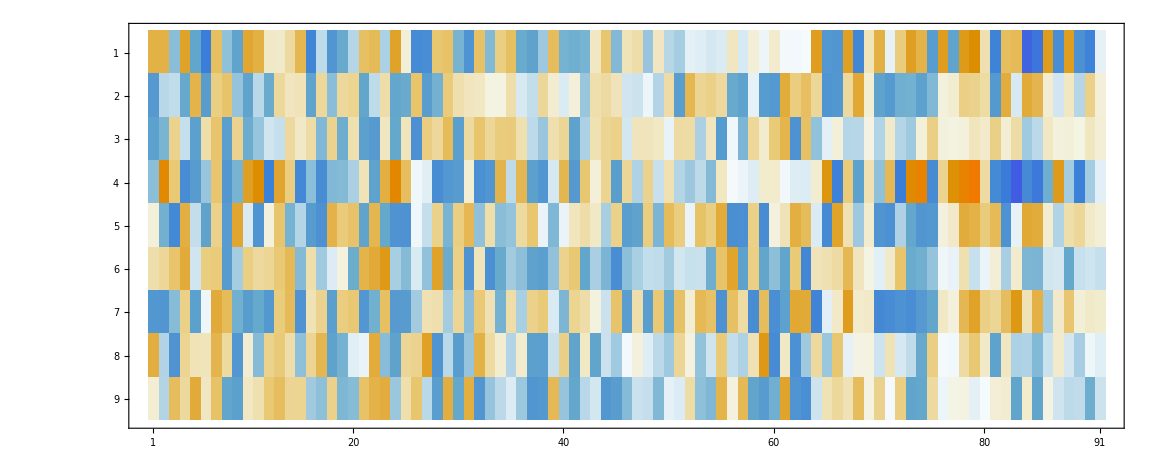

```mathematica
MatrixPlot[Transpose[linMat]]
```

```mathematica
linMatT=Transpose[linMat];
linMatT=(#-#[[1]])&/@linMatT;
linMat=Transpose[linMatT];
```

```mathematica
(*Table[(
aVar=problemVars[[varIdx]];
paramBest=aVar/.fmSolAssoc;
othersFixed=AssociationThread[Delete[problemVars,varIdx]->Delete[solVec,varIdx]];
thisPoly=sqdiff/.othersFixed;
polySols=Last/@Last/@Solve[thisPoly==minpoly+1*totalVariance];
polySols=Select[polySols,Im[#]==0&];
paramSigma=Max[polySols]-Min[polySols];
(aVar->{paramBest,paramSigma})
),
{varIdx,1,Length[problemVars]}];*)

(*{constant,grad,hess}=FromPolynomialToSecondOrder[sqdiff,problemVars];*)
```

```mathematica
simplisqdiff/.{B66^2->5 B66^2}
```

{204607.+520.102 B66+3.3062 B66^2}

```mathematica
λ0Vec
```

{{0.},{71.7336},{95.1855},{137.961},{182.733},{220.996},{333.97},{444.308},{2126.5},{2157.97},{2190.2},{2284.48},{2289.76},{2294.88},{2317.53},{2398.86},{2411.89},{2437.39},{2540.01},{4178.66},{4199.45},{4282.86},{4321.09},{4383.7},{4466.69},{4478.},{4495.5},{4507.09},{4589.57},{4692.53},{4711.22},{4813.04},{5144.84},{5182.55},{5184.76},{5269.35},{5275.35},{6456.68},{6490.08},{6507.4},{6579.15},{6600.43},{6628.23},{6740.36},{6917.98},{6936.28},{6950.16},{6952.3},{6953.94},{6983.81},{7034.63},{7096.81},{7152.49},{9720.74},{9761.89},{9859.31},{9926.21},{9956.97},{9995.16},{10029.7},{10149.9},{10515.9},{16887.},{16895.1},{17082.4},{17117.6},{17170.},{20907.4},{21283.7},{21303.8},{21339.7},{21390.3},{21406.3},{21481.2},{21485.7},{21517.9},{21570.5},{21589.2},{21590.5},{21637.3},{21666.5},{21803.9},{21888.8},{21957.4},{22670.1},{22706.2},{22739.4},{22787.9},{22818.5},{46964.6}}

```mathematica
sqdiff
```

{6.93423×10^9+366.762 B02+1.51202 B02^2-1327.64 B04-0.192675 B02 B04+0.282997 B04^2+285.891 B06-0.022234 B02 B06-0.0137977 B04 B06+0.15913 B06^2+1019.46 B22+1.36115 B02 B22-0.246126 B04 B22-0.0777906 B06 B22+2.72676 B22^2+1819.92 B24-0.287584 B02 B24+0.225146 B04 B24-0.0281981 B06 B24-0.375832 B22 B24+0.536711 B24^2+735.813 B26+0.219907 B02 B26-0.128238 B04 B26-0.13264 B06 B26+0.0440767 B22 B26-0.0101825 B24 B26+0.37487 B26^2-2229.92 B44-0.152633 B02 B44+0.268812 B04 B44+0.0689779 B06 B44-0.493725 B22 B44+0.288428 B24 B44-0.0207652 B26 B44+0.643596 B44^2-1472.51 B46+0.0928816 B02 B46-0.0457809 B04 B46+0.00203781 B06 B46-0.00472607 B22 B46-0.049911 B24 B46+0.00964018 B26 B46+0.0387331 B44 B46+0.303052 B46^2-317.23 B66+0.00496721 B02 B66+0.0651513 B04 B66-0.0137675 B06 B66+0.0563993 B22 B66-0.0464329 B24 B66+0.216932 B26 B66-0.252221 B44 B66+0.095259 B46 B66+0.33062 B66^2}

```mathematica
λexp
```

{{0.2},{71.},{95.},{138.},{183.},{221.},{333.},{444.},{2126.},{2158.},{2191.},{2284.},{2290.},{2295.},{2318.},{2399.},{2412.},{2438.},{2540.},{4179.},{4200.},{4283.},{4321.},{4384.},{4467.},{4478.},{4496.},{4508.},{4590.},{4693.},{4712.},{4814.},{5145.},{5182.},{5185.},{5270.},{5276.},{6456.},{6490.},{6508.},{6579.},{6600.},{6628.},{6740.},{6918.},{6936.},{6950.},{6952.},{6953.},{6983.},{7034.},{7096.},{7152.},{9721.},{9762.},{9860.},{9927.},{9958.},{9996.},{10030.},{10150.},{10516.},{16887.},{16895.},{17082.},{17117.},{17170.},{20911.},{21284.},{21304.},{21340.},{21390.},{21406.},{21481.},{21487.},{21519.},{21570.},{21592.},{21588.},{21637.},{21666.},{21804.},{21889.},{21958.},{22668.},{22704.},{22738.},{22787.},{22817.},{46965.}}

```mathematica
λexp
```

{{0.2},{71.},{95.},{138.},{183.},{221.},{333.},{444.},{2126.},{2158.},{2191.},{2284.},{2290.},{2295.},{2318.},{2399.},{2412.},{2438.},{2540.},{4179.},{4200.},{4283.},{4321.},{4384.},{4467.},{4478.},{4496.},{4508.},{4590.},{4693.},{4712.},{4814.},{5145.},{5182.},{5185.},{5270.},{5276.},{6456.},{6490.},{6508.},{6579.},{6600.},{6628.},{6740.},{6918.},{6936.},{6950.},{6952.},{6953.},{6983.},{7034.},{7096.},{7152.},{9721.},{9762.},{9860.},{9927.},{9958.},{9996.},{10030.},{10150.},{10516.},{16887.},{16895.},{17082.},{17117.},{17170.},{20911.},{21284.},{21304.},{21340.},{21390.},{21406.},{21481.},{21487.},{21519.},{21570.},{21592.},{21588.},{21637.},{21666.},{21804.},{21889.},{21958.},{22668.},{22704.},{22738.},{22787.},{22817.},{46965.}}

```mathematica
linMat[[presentDataIndices]]//Dimensions
```

{90,9}

```mathematica
diff/.fmSol[[2]]
```

{-0.2,0.733599,0.18551,-0.0390499,-0.267283,-0.00359881,0.970028,0.307813,0.500422,-0.0314925,-0.798709,0.481039,-0.237374,-0.11515,-0.474073,-0.139816,-0.1123,-0.605776,0.0128187,-0.337821,-0.55139,-0.142717,0.0941018,-0.298981,-0.305996,0.00201579,-0.498362,-0.9065,-0.427839,-0.465704,-0.783051,-0.956203,-0.15898,0.547996,-0.236847,-0.652837,-0.650045,0.683859,0.0782522,-0.600706,0.148407,0.430186,0.231963,0.363956,-0.0176059,0.277776,0.158663,0.298312,0.93642,0.805358,0.628339,0.809889,0.494585,-0.26393,-0.113955,-0.692574,-0.790135,-1.03033,-0.84146,-0.283473,-0.126977,-0.140645,-0.0438853,0.139319,0.36832,0.591187,-0.00680393,-3.55668,-0.252929,-0.152769,-0.26933,0.313507,0.292118,0.156402,-1.34547,-1.13696,0.534845,-2.81189,2.45948,0.325738,0.528441,-0.128175,-0.208145,-0.560834,2.13666,2.24123,1.40082,0.876211,1.54674,-0.361821}

```mathematica
FromPolynomialToSecondOrder[sqdiff,problemVars][[-1]]//MatrixForm
```

(5.36811 | -2.14125 | -1.42229 | 0.6925 | -0.184409 | 0.61691 | -2.23372 | 2.63458 | 0.0894767
-2.14125 | 2.18566 | 1.15004 | 0.309603 | 0.139662 | -0.458276 | 1.9986 | -2.15869 | -0.00521721
-1.42229 | 1.15004 | 1.15448 | 0.321578 | -0.089828 | -0.369759 | 1.31196 | -1.51605 | -0.0642402
0.6925 | 0.309603 | 0.321578 | 5.64418 | -0.405055 | -0.069183 | 0.099778 | -0.729792 | 0.0322067
-0.184409 | 0.139662 | -0.089828 | -0.405055 | 1.07739 | 0.00733295 | 0.197178 | 0.062096 | -0.0424735
0.61691 | -0.458276 | -0.369759 | -0.069183 | 0.00733295 | 0.816975 | -0.373252 | 0.440102 | 0.231228
-2.23372 | 1.9986 | 1.31196 | 0.099778 | 0.197178 | -0.373252 | 3.13458 | -2.21788 | -0.327394
2.63458 | -2.15869 | -1.51605 | -0.729792 | 0.062096 | 0.440102 | -2.21788 | 3.36204 | 0.186837
0.0894767 | -0.00521721 | -0.0642402 | 0.0322067 | -0.0424735 | 0.231228 | -0.327394 | 0.186837 | 0.664187)

```mathematica
2*Transpose[linMat[[presentDataIndices]]].linMat[[presentDataIndices]]//MatrixForm
```

(5.36811 | -2.14125 | -1.42229 | 0.6925 | -0.184409 | 0.61691 | -2.23372 | 2.63458 | 0.0894767
-2.14125 | 2.18566 | 1.15004 | 0.309603 | 0.139662 | -0.458276 | 1.9986 | -2.15869 | -0.00521721
-1.42229 | 1.15004 | 1.15448 | 0.321578 | -0.089828 | -0.369759 | 1.31196 | -1.51605 | -0.0642402
0.6925 | 0.309603 | 0.321578 | 5.64418 | -0.405055 | -0.069183 | 0.099778 | -0.729792 | 0.0322067
-0.184409 | 0.139662 | -0.089828 | -0.405055 | 1.07739 | 0.00733295 | 0.197178 | 0.062096 | -0.0424735
0.61691 | -0.458276 | -0.369759 | -0.069183 | 0.00733295 | 0.816975 | -0.373252 | 0.440102 | 0.231228
-2.23372 | 1.9986 | 1.31196 | 0.099778 | 0.197178 | -0.373252 | 3.13458 | -2.21788 | -0.327394
2.63458 | -2.15869 | -1.51605 | -0.729792 | 0.062096 | 0.440102 | -2.21788 | 3.36204 | 0.186837
0.0894767 | -0.00521721 | -0.0642402 | 0.0322067 | -0.0424735 | 0.231228 | -0.327394 | 0.186837 | 0.664187)

Calculating the sum of squares of differences around solution ...

B02

Calculating the difference between eigenvalues at solution ...

127355.+1169.03 B02+2.68406 B02^2

B04

Calculating the difference between eigenvalues at solution ...

127355.+1169.03 B02+2.68406 B02^2

B06

Calculating the difference between eigenvalues at solution ...

596080.-1614.12 B04+1.09283 B04^2

B22

Calculating the difference between eigenvalues at solution ...

266149.-783.826 B06+0.577239 B06^2

B24

Calculating the difference between eigenvalues at solution ...

40215.3+673.248 B22+2.82209 B22^2

B26

Calculating the difference between eigenvalues at solution ...

99989.8-464.028 B24+0.538694 B24^2

B44

Calculating the difference between eigenvalues at solution ...

346630.+752.512 B26+0.408487 B26^2

B46

Calculating the difference between eigenvalues at solution ...

598413.-1936.79 B44+1.56729 B44^2

B66

Calculating the difference between eigenvalues at solution ...

203110.+1168.47 B46+1.68102 B46^2

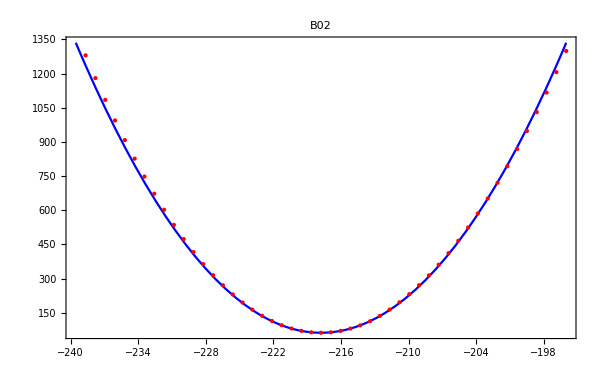
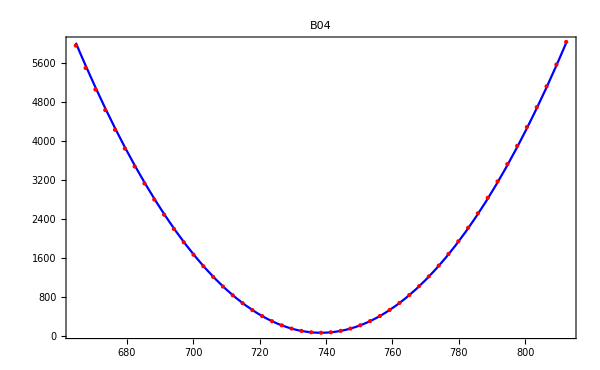
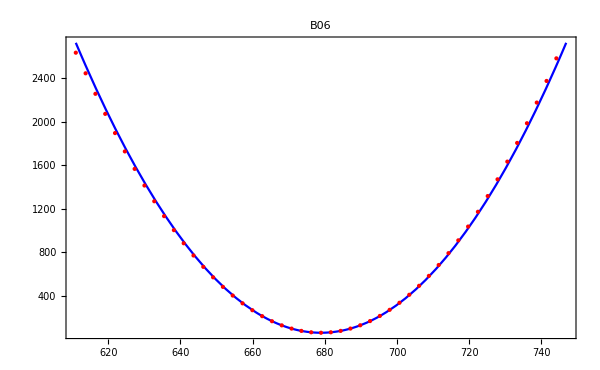
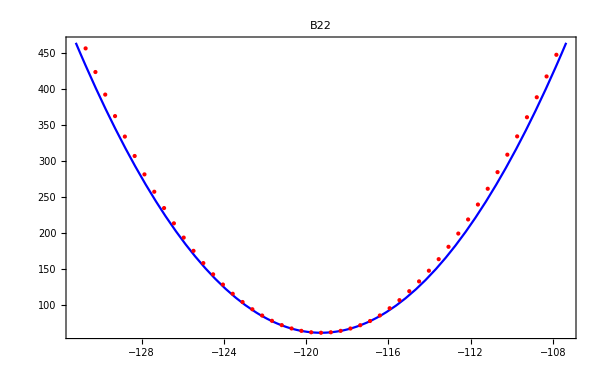
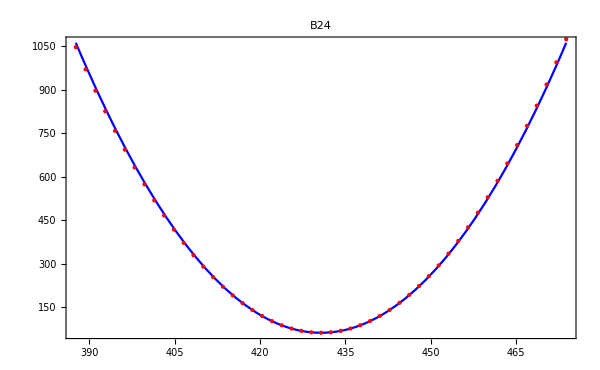
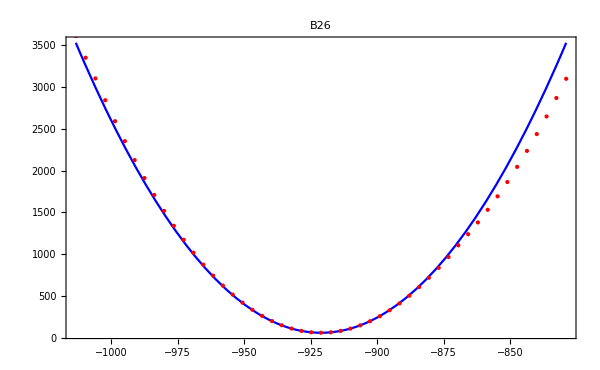
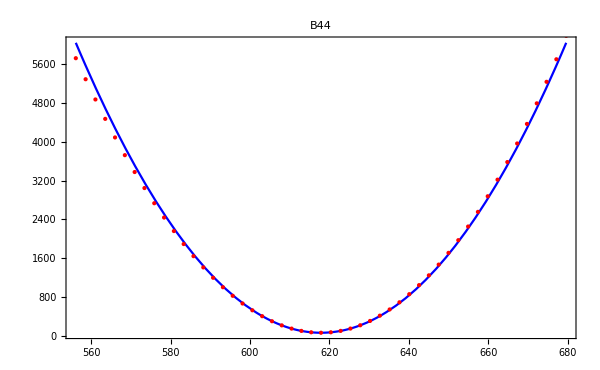
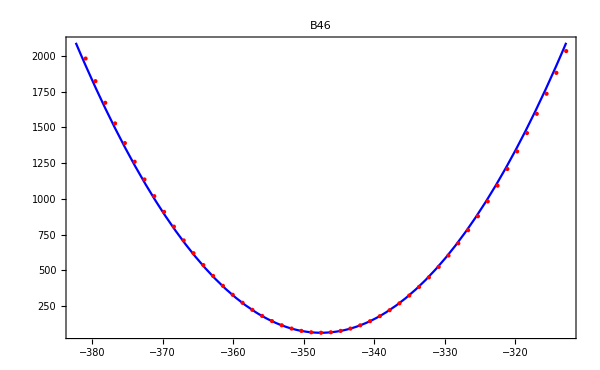

```mathematica
λexp=Transpose[{First/@expData[[presentDataIndices]]}];
λ0Vec=Transpose[{eigenEnergies[[presentDataIndices]]}];
λ0Vec=λ0Vec-Min[λ0Vec];
solVec=Last/@fmSol[[-1]];
problemVarsVec=Transpose[{problemVars}];
solVecVec=Transpose[{solVec}];
fmSolAssoc=Association[fmSol[[2]]];
(*totalVariance=Length[presentDataIndices]*σexp^2;*)
linearEigenValues=Expand[λ0Vec+linMat[[presentDataIndices]].(problemVarsVec-solVecVec)];
diff=Flatten[linearEigenValues-λexp];
PrintFun["Calculating the sum of squares of differences around solution ... "];
sqdiff=Expand[Total[diff^2]];
plots=Table[(
chosenVar=problemVars[[testVarIdx]];
Print[chosenVar];
{paramMin,paramMax}=MinMax[{0.90solVec[[testVarIdx]],1.10solVec[[testVarIdx]]}];
PrintFun["Calculating the difference between eigenvalues at solution ..."];
(*diff=(λ0Vec-λexp)+linMat[[presentDataIndices]].(problemVarsVec-solVecVec)+quadMat[[presentDataIndices]].(Map[#^2&,(problemVarsVec-solVecVec)]);*)
(*diff=(λ0Vec-λexp)+linMat[[presentDataIndices]].(problemVarsVec-solVecVec)+1*quadMat[[presentDataIndices]].(Map[#^2&,(problemVarsVec-solVecVec)]);*)

(*Print["Calculating the minimum (which should coincide to sol) ..."];
minpoly=sqdiff/.AssociationThread[cfVars->solVec];*)
Print[simplisqdiff];
otherVars=Complement[problemVars,{chosenVar}];
simpler=(AssociationThread[otherVars->(otherVars/.fmSol[[2]])]);
simplisqdiff=sqdiff/.simpler;
(*Print[simplisqdiff];*)
testRange=Subdivide[paramMin,paramMax,50];
(*simplisqdiff=simplisqdiff/.{chosenVar^2->1.0*(chosenVar+solVec[[testVarIdx]])^2};*)
plotArg={chosenVar,Min[testRange],Max[testRange]};
numerical=Table[(
repVars=problemVars/.fmSol[[2]];
repVars[[testVarIdx]]=testValue;
theSum=(Sum[(expData[[j]][[1]]-(PartialHamEigenvalues@@repVars)[j])^2,{j,presentDataIndices}]);
{testValue,theSum}
),{testValue,testRange}];

plot1=Plot[simplisqdiff,
plotArg,
PlotStyle->Blue,
Frame->True,
PlotRange->{All,All},
PlotLabel->chosenVar,
FrameStyle->Directive[16],
PlotLegends->Style["linear",Blue],
Epilog->{Red,Point[numerical]},ImageSize->600]
)
,{testVarIdx,1,9}];
plots
```

```mathematica
Rasterize[Grid[Partition[plots,3]]]//CopyToClipboard
```

```mathematica
(*Table[(
aVar=problemVars[[varIdx]];
paramBest=aVar/.fmSolAssoc;
othersFixed=AssociationThread[Delete[problemVars,varIdx]->Delete[solVec,varIdx]];
thisPoly=sqdiff/.othersFixed;
polySols=Last/@Last/@Solve[thisPoly==minpoly+1*totalVariance];
polySols=Select[polySols,Im[#]==0&];
paramSigma=Max[polySols]-Min[polySols];
(aVar->{paramBest,paramSigma})
),
{varIdx,1,Length[problemVars]}]*)
```

```mathematica
solVec=Last/@fmSol[[-1]];
fullSolVec=standardValues;
fullSolVec[[problemVarsPositions]]=solVec;
PrintFun["Calculating the numerical hamiltonian of the solution ..."];
fullHam=compiledHam@@fullSolVec;
PrintFun["Calculating energies and eigenvectors ..."];
{eigenEnergies,eigenVectors}=Eigensystem[fullHam];
eigenEnergies=Sort[eigenEnergies];
(*eigenEnergies=eigenEnergies-Min[eigenEnergies];*)
```

Calculating the numerical hamiltonian of the solution ...

Calculating energies and eigenvectors ...

```mathematica
vareigen={};
lineigen={};
solVec=Last/@fmSol[[-1]];
problemVarIndex=1;
points={solVec[[problemVarIndex]],0.9*solVec[[problemVarIndex]],1.10*solVec[[problemVarIndex]]};
testRange=Subdivide[Min[points],Max[points],50];
Do[(
B02val=testRange[[idx]];
fullSolVec=standardValues;
fullSolVec[[problemVarsPositions]]=solVec;
fullSolVec[[problemVarIndex]]=B02val;
fullHam=compiledHam@@fullSolVec;
directEigen=Sort[Eigenvalues[fullHam]];
(*directEigen=directEigen-Min[directEigen];*)
directEigen={B02val,#}&/@directEigen;
vareigen=Append[vareigen,directEigen];
linearEigen=Table[linMat[[idx]][[problemVarIndex]](B02val-solVec[[problemVarIndex]])+eigenEnergies[[idx]],{idx,1,91}];
lineigen=Append[lineigen,{B02val,#}&/@linearEigen]
)
,{idx,1,Length[testRange]}];
Manipulate[ListPlot[{#[[idx]]&/@vareigen,#[[idx]]&/@lineigen},PlotStyle->{Blue,Red}],{idx,1,Length[vareigen],1}]
```

```mathematica
numsumHere=Total[((#-Min[#]-Flatten[λexp])^2)]&/@Transpose[Transpose[Map[Last,vareigen,{2}]][[presentDataIndices]]];
linsumHere=Total[((#-Min[#]-Flatten[λexp])^2)]&/@Transpose[Transpose[Map[Last,lineigen,{2}]][[presentDataIndices]]];
```

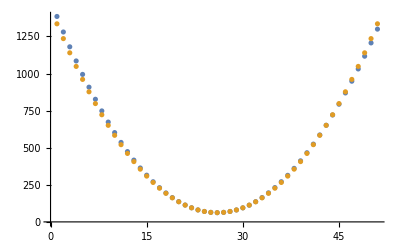

```mathematica
ListPlot[{numsumHere,linsumHere}]
```

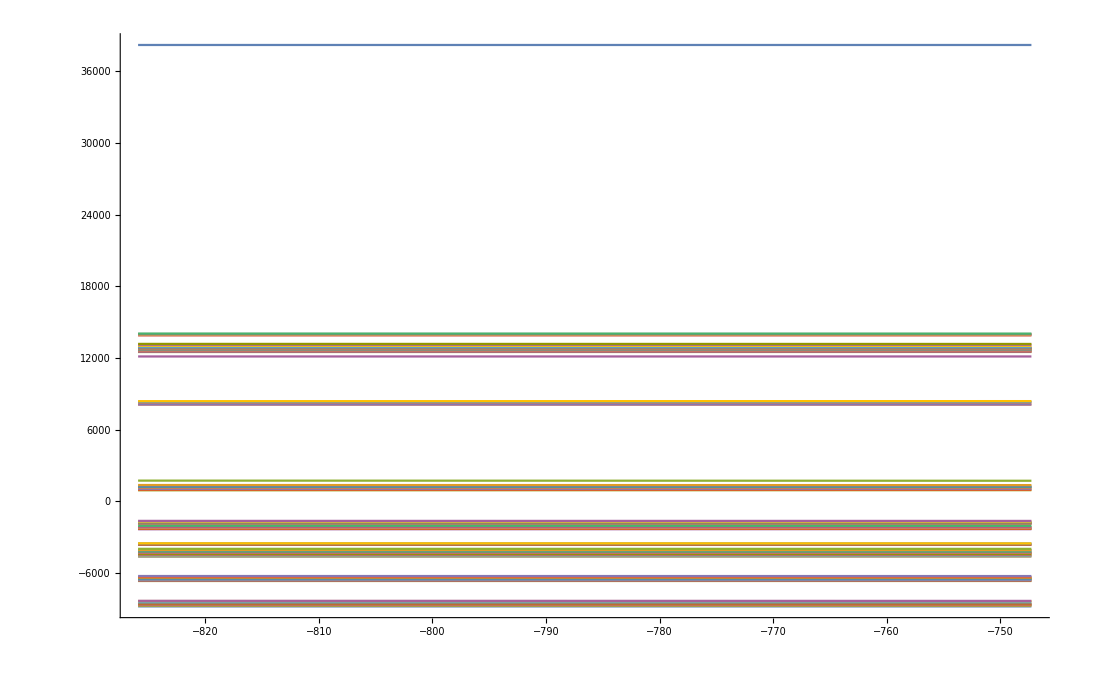

```mathematica
ListPlot[Transpose[lineigen],Joined->True]
```

```mathematica
linMat
```

```mathematica
linearEigen
```

-8811.01

```mathematica
linMat[[1]]*(B02val-solVec[[1]])
```

{14.9471,-8.63865,-7.14875,6.3548,-0.726584,2.06544,-6.50458,7.69003,-0.667852}

-8811.01

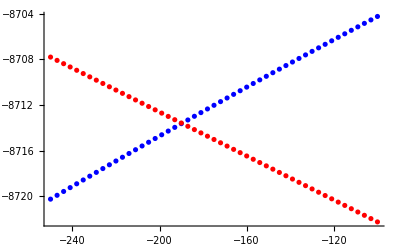

```mathematica
linearEigen
```

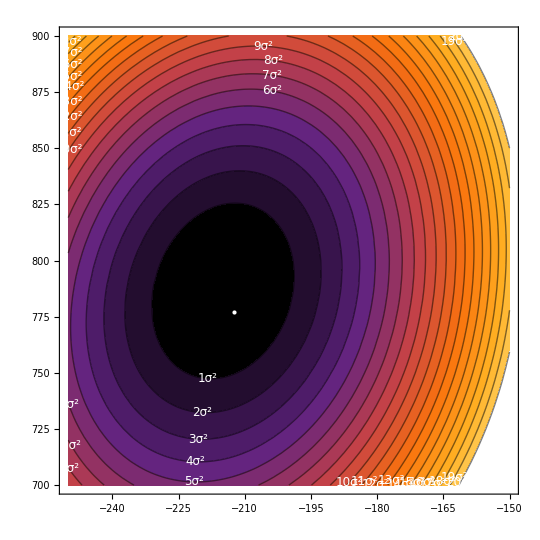

```mathematica
numContours=20;
totalVariance=Length[presentDataIndices]*σexp^2;
contourLevels=(minpoly+(totalVariance*Range[1,numContours]));
contourLabels=ToString/@Range[1,numContours];
contourLabelFunction=(Text[Style[contourLabels[[Position[contourLevels,Nearest[contourLevels,#3][[1]]][[1,1]]]]<>"σ^2",12,FontFamily->"Times",White],{#1,#2}]&);
thisPoly=sqdiff/.AssociationThread[{B06,B22,B24,B26,B44,B46,B66}->solVec[[3;;]]];

ContourPlot[thisPoly,{B02,-250,-150},{B04,700,900},Epilog->{White,Point[solVec[[;;2]]]},ColorFunction->"SunsetColors",
Contours->contourLevels,ContourLabels->contourLabelFunction]
```

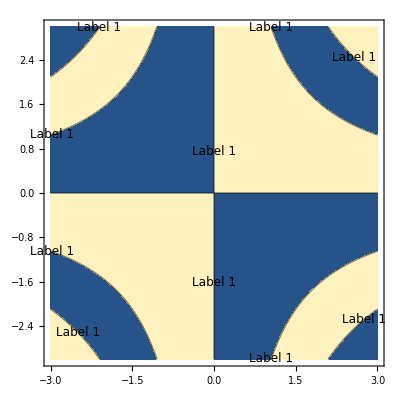

```mathematica
(*Define the function to be contoured*)f[x_,y_]:=Sin[x y]

(*Define a list of custom labels*)
customLabels={"Label 1","Label 2","Label 3","Label 4","Label 5"};

(*Determine the contour levels for the custom labels*)
(*For this example,I'm generating them automatically.*)
(*Replace this with your specific contour levels if needed.*)
contourLevels=Table[f[0,pi*(i-1)/4],{i,Length[customLabels]}];

(*Create a function to map contour levels to custom labels*)
contourLabelFunction=(Text[Style[customLabels[[Position[contourLevels,Nearest[contourLevels,#3][[1]]][[1,1]]]],12,FontFamily->"Times"],{#1,#2}]&);

(*Create the contour plot with custom labels*)
ContourPlot[f[x,y],{x,-3,3},{y,-3,3},Contours->contourLevels,ContourLabels->contourLabelFunction]
```

Function::fpct: Too many parameters in {x,y,z,n} to be filled from Function[{x,y,z,n},Text[customLabels⟦n⟧,{x,y}]][-1.88685,-2.04756,-0.66].

Function::fpct: Too many parameters in {x,y,z,n} to be filled from Function[{x,y,z,n},Text[customLabels⟦n⟧,{x,y}]][2.99546,-0.808113,-0.66].

Function::fpct: Too many parameters in {x,y,z,n} to be filled from Function[{x,y,z,n},Text[customLabels⟦n⟧,{x,y}]][-0.808113,2.99546,-0.66].

General::stop: Further output of Function::fpct will be suppressed during this calculation.

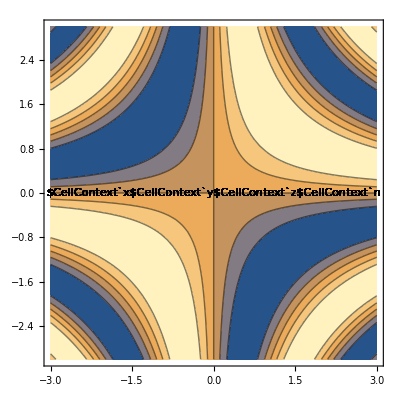

```mathematica
(*Define the function to be contoured*)f[x_,y_]:=Sin[x y]

(*Define a list of custom labels*)
customLabels={"Label 1","Label 2","Label 3","Label 4","Label 5"};

(*Create the contour plot with custom labels*)
ContourPlot[f[x,y],{x,-3,3},{y,-3,3},Contours->Length[customLabels],(*Ensure the number of contours matches the number of labels*)ContourLabels->(Function[{x,y,z,n},Text[Style[customLabels[[n]],12,FontFamily->"Times"],{x,y}]])]
```

```mathematica
(ToString[#]&/@Range[0,numContours])
```

{0,1,2,3,4,5,6,7,8,9,10}

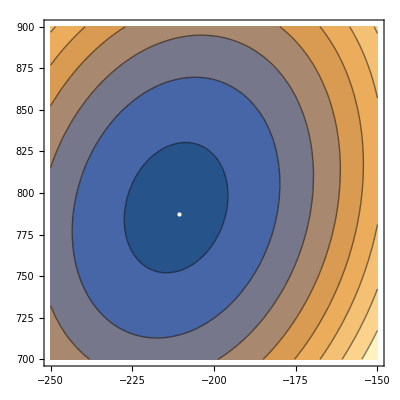

```mathematica
ContourPlot[poly/.AssociationThread[{B06,B22,B24,B26,B44,B46,B66}->solVec[[3;;]]],{B02,-250,-150},{B04,700,900},Epilog->{White,Point[solVec[[;;2]]]}]
```

```mathematica
Length[solVec[[3;;]]]
```

7

```mathematica
(*Define your multivariate polynomial*)polynomial=x^3+x^2 y+x y^2+y^3;

(*Truncate the polynomial to a given order,say 2*)
truncatedPolynomial=Normal[Series[polynomial,{x,0,2},{y,0,2}]];

(*The result is the polynomial truncated to second order*)
truncatedPolynomial
```

x^2 y+x y^2

```mathematica
(*Example usage*)
polynomial=x+x^3+x^2 y+x y^2+y^3;
truncatedPolynomial=truncatePolynomial[polynomial,1];  (*Truncate to total order 2*)

truncatedPolynomial
```

x

```mathematica
Series[sqdiff,problemVars]
```

```mathematica
standardValues[[Flatten[Position[allVars,#]&/@irrelevantVars]]]
```

{68878.,50347.,32901.,2.08,-88.6,16.23,-566.6,1371.,751.7}

```mathematica
Series[sqdiff,{B02,0,2},{B04,0,2},{B06,0,2}]
```

(((2.15421×10^12+9.72449×10^6 B22+38980.9 B22^2+0.224514 B22^3+0.000502353 B22^4-904862. B24-9.76352 B22 B24-0.0428709 B22^2 B24+1319.42 B24^2+0.0101926 B22 B24^2+0.0000461146 B22^2 B24^2-0.0032736 B24^3+1.94318×10^-6 B24^4+208609. B26+0.219615 B22 B26+0.0020445 B22^2 B26-0.147709 B24 B26+0.000487869 B24^2 B26+67.887 B26^2+0.00021744 B22 B26^2+1.52722×10^-6 B22^2 B26^2-0.000117155 B24 B26^2+3.13889×10^-7 B24^2 B26^2+0.00071652 B26^3+1.94487×10^-7 B26^4-190004. B44-2.75445 B22 B44-0.0134615 B22^2 B44+0.565396 B24 B44-0.00109171 B24^2 B44-1.40782 B26 B44-0.000727668 B26^2 B44+519.877 B44^2+0.00239613 B22 B44^2+0.0000123283 B22^2 B44^2-0.000597191 B24 B44^2+1.27729×10^-6 B24^2 B44^2+0.00136219 B26 B44^2+7.0156×10^-7 B26^2 B44^2-0.00358077 B44^3+1.71919×10^-6 B44^4+31123.7 B46-0.424032 B22 B46-0.00154299 B22^2 B46-0.0921977 B24 B46+0.000100985 B24^2 B46-0.188737 B26 B46-0.0000645381 B26^2 B46-0.287868 B44 B46+0.000348783 B44^2 B46+24.3524 B46^2+0.000253203 B22 B46^2+2.21871×10^-6 B22^2 B46^2-0.000502923 B24 B46^2+6.03055×10^-7 B24^2 B46^2+0.000219058 B26 B46^2+1.90671×10^-7 B26^2 B46^2-0.00132725 B44 B46^2+1.3413×10^-6 B44^2 B46^2+0.00131082 B46^3+1.50259×10^-6 B46^4-54972.3 B66-0.0105602 B22 B66+0.000959208 B22^2 B66-0.0287417 B24 B66+0.000427083 B24^2 B66+0.68929 B26 B66+0.000293375 B26^2 B66-0.569526 B44 B66+0.000404065 B44^2 B66+0.00597912 B46 B66+0.000327467 B46^2 B66-24.6398 B66^2-0.0000932539 B22 B66^2+2.37699×10^-7 B22^2 B66^2-0.0000601659 B24 B66^2+4.55565×10^-7 B24^2 B66^2+0.00063031 B26 B66^2+3.54613×10^-7 B26^2 B66^2-0.00050994 B44 B66^2+4.91876×10^-7 B44^2 B66^2-0.0000445915 B46 B66^2+3.21826×10^-7 B46^2 B66^2+0.000843971 B66^3+4.39096×10^-7 B66^4-6.47777×10^7 F2-146.245 B22 F2-0.58566 B22^2 F2+13.563 B24 F2-0.0198011 B24^2 F2-3.1398 B26 F2-0.00102219 B26^2 F2+2.91596 B44 F2-0.00784723 B44^2 F2-0.495042 B46 F2-0.000469247 B46^2 F2+0.83347 B66 F2+0.000379449 B66^2 F2+959.897 F2^2+0.00107078 B22 F2^2+4.28288×10^-6 B22^2 F2^2-0.000100195 B24 F2^2+1.45424×10^-7 B24^2 F2^2+0.0000230361 B26 F2^2+8.11062×10^-9 B26^2 F2^2-0.0000217336 B44 F2^2+5.75162×10^-8 B44^2 F2^2+3.41884×10^-6 B46 F2^2+3.65726×10^-9 B46^2 F2^2-5.7312×10^-6 B66 F2^2-2.00549×10^-9 B66^2 F2^2-0.00711144 F2^3+2.59998×10^-8 F2^4-2.89805×10^6 F4-6.37934 B22 F4-0.0256908 B22^2 F4+0.441504 B24 F4-0.000660113 B24^2 F4-0.155498 B26 F4+0.0000108446 B26^2 F4+0.161104 B44 F4-0.000322771 B44^2 F4-0.10139 B46 F4-0.000214909 B46^2 F4+0.0272923 B66 F4+0.0000871482 B66^2 F4+43.5619 F2 F4-0.000316024 F2^2 F4+30.9279 F4^2+0.0000653212 B22 F4^2+2.62645×10^-7 B22^2 F4^2-4.2805×10^-6 B24 F4^2+7.20988×10^-9 B24^2 F4^2+2.03955×10^-6 B26 F4^2+5.52702×10^-10 B26^2 F4^2-2.82377×10^-6 B44 F4^2+4.49974×10^-9 B44^2 F4^2+1.44663×10^-6 B46 F4^2+3.76801×10^-9 B46^2 F4^2+2.73141×10^-7 B66 F4^2-1.02805×10^-10 B66^2 F4^2-0.00044491 F2 F4^2+3.24834×10^-9 F2^2 F4^2-0.0000288317 F4^3+1.55425×10^-10 F4^4-1.19079×10^8 F6-270.172 B22 F6-1.08121 B22^2 F6+25.6209 B24 F6-0.0370419 B24^2 F6-5.77514 B26 F6-0.00205756 B26^2 F6+5.32789 B44 F6-0.0144152 B44^2 F6-0.845546 B46 F6-0.000469869 B46^2 F6+1.53629 B66 F6+0.000509089 B66^2 F6+1790.85 F2 F6-0.0130975 F2^2 F6+78.3844 F4 F6-0.000804809 F4^2 F6+3456.97 F6^2+0.00409976 B22 F6^2+0.0000164056 B22^2 F6^2-0.000389079 B24 F6^2+5.61671×10^-7 B24^2 F6^2+0.0000866573 B26 F6^2+3.01522×10^-8 B26^2 F6^2-0.0000796206 B44 F6^2+2.17281×10^-7 B44^2 F6^2+0.0000126639 B46 F6^2+6.3042×10^-9 B46^2 F6^2-0.0000239626 B66 F6^2-8.97003×10^-9 B66^2 F6^2-0.027162 F2 F6^2+1.98629×10^-7 F2^2 F6^2-0.00118852 F4 F6^2+1.22005×10^-8 F4^2 F6^2-0.0500724 F6^3+3.79677×10^-7 F6^4-2.70815×10^7 M0-85.6294 B22 M0-0.397794 B22^2 M0+15.7986 B24 M0-0.0232255 B24^2 M0-0.530993 B26 M0+0.00205373 B26^2 M0-4.40537 B44 M0-0.00286656 B44^2 M0+6.47174 B46 M0+0.0189486 B46^2 M0+10.2417 B66 M0+0.00681662 B66^2 M0+416.85 F2 M0-0.00304134 F2^2 M0-17.3567 F4 M0+0.000168258 F4^2 M0+857.97 F6 M0-0.0130333 F6^2 M0+1.37943×10^7 M0^2+31.5336 B22 M0^2+0.126435 B22^2 M0^2-2.98864 B24 M0^2+0.00437074 B24^2 M0^2+0.695311 B26 M0^2+0.000290971 B26^2 M0^2-0.639247 B44 M0^2+0.00168969 B44^2 M0^2+0.0431222 B46 M0^2+0.000101983 B46^2 M0^2-0.136426 B66 M0^2+9.60019×10^-6 B66^2 M0^2-207.445 F2 M0^2+0.00151763 F2^2 M0^2-9.05147 F4 M0^2+0.0000935967 F4^2 M0^2-382.299 F6 M0^2+0.0057972 F6^2 M0^2-97.1493 M0^3+22.2645 M0^4+78996.7 P2+0.155818 B22 P2+0.00052547 B22^2 P2-0.0143249 B24 P2+3.05364×10^-6 B24^2 P2+0.000546298 B26 P2-6.29033×10^-6 B26^2 P2-0.0316547 B44 P2+0.0000373972 B44^2 P2+0.00202537 B46 P2+0.0000196989 B46^2 P2-0.0679207 B66 P2-0.000039359 B66^2 P2-1.29058 F2 P2+8.37637×10^-6 F2^2 P2-0.165761 F4 P2+1.17611×10^-6 F4^2 P2-1.86782 F6 P2+0.0000295602 F6^2 P2-3.55899 M0 P2+0.172028 M0^2 P2+99.5932 P2^2+0.00022831 B22 P2^2+9.24633×10^-7 B22^2 P2^2-0.0000212124 B24 P2^2+3.2187×10^-8 B24^2 P2^2+6.54368×10^-6 B26 P2^2+3.59257×10^-9 B26^2 P2^2-4.54979×10^-6 B44 P2^2+1.25367×10^-8 B44^2 P2^2+7.83423×10^-7 B46 P2^2+2.03099×10^-9 B46^2 P2^2-4.04435×10^-7 B66 P2^2+1.44978×10^-9 B66^2 P2^2-0.00149933 F2 P2^2+1.10026×10^-8 F2^2 P2^2-0.0000623884 F4 P2^2+6.95106×10^-10 F4^2 P2^2-0.00277172 F6 P2^2+4.20721×10^-8 F6^2 P2^2-0.00146046 M0 P2^2+0.000324446 M0^2 P2^2-6.89405×10^-6 P2^3+1.43256×10^-9 P2^4-3.01964×10^9 α-6802.06 B22 α-27.1506 B22^2 α+645.926 B24 α-0.939644 B24^2 α-128.753 B26 α-0.0523904 B26^2 α+131.334 B44 α-0.375198 B44^2 α-6.58522 B46 α-0.0123017 B46^2 α+35.6472 B66 α-0.00131464 B66^2 α+45354.5 F2 α-0.33209 F2^2 α+1957.67 F4 α-0.020243 F4^2 α+83739.3 F6 α-1.26956 F6^2 α+21113.8 M0 α-9686.72 M0^2 α-53.9137 P2 α-0.0702571 P2^2 α+9.53029×10^7 α^2+214.093 B22 α^2+0.856522 B22^2 α^2-20.3827 B24 α^2+0.0293611 B24^2 α^2+4.47734 B26 α^2+0.00155336 B26^2 α^2-4.1414 B44 α^2+0.0113189 B44^2 α^2+0.619076 B46 α^2+0.000302342 B46^2 α^2-1.267 B66 α^2-0.00049113 B66^2 α^2-1416.91 F2 α^2+0.0103606 F2^2 α^2-61.9498 F4 α^2+0.00063504 F4^2 α^2-2611.44 F6 α^2+0.039606 F6^2 α^2-664.394 M0 α^2+302.431 M0^2 α^2+1.69176 P2 α^2+0.00218956 P2^2 α^2-66213.5 α^3+1033.02 α^4+4.37095×10^6 β+11.7984 B22 β+0.0478146 B22^2 β-1.20803 B24 β+0.00140587 B24^2 β+0.810475 B26 β+0.0000413059 B26^2 β-1.27464 B44 β+0.00123755 B44^2 β+0.570756 B46 β+0.000629657 B46^2 β-0.0477515 B66 β-0.000440072 B66^2 β-68.3871 F2 β+0.000500673 F2^2 β-4.68265 F4 β+0.0000446933 F4^2 β-124.149 F6 β+0.00188291 F6^2 β-62.5177 M0 β+14.9414 M0^2 β-0.00312249 P2 β+0.0000909376 P2^2 β-28.5923 α β+98.2282 α^2 β+1723.11 β^2+0.00370261 B22 β^2+0.0000148094 B22^2 β^2-0.000282346 B24 β^2+4.50188×10^-7 B24^2 β^2+0.000101954 B26 β^2+4.17724×10^-8 B26^2 β^2-0.00012464 B44 β^2+2.3461×10^-7 B44^2 β^2+0.0000289079 B46 β^2+1.33363×10^-7 B46^2 β^2+9.57533×10^-6 B66 β^2+1.02804×10^-8 B66^2 β^2-0.024958 F2 β^2+1.82266×10^-7 F2^2 β^2-0.00138915 F4 β^2+1.45957×10^-8 F4^2 β^2-0.045326 F6 β^2+6.8752×10^-7 F6^2 β^2+0.00815501 M0 β^2+0.00532903 M0^2 β^2+0.0000532941 P2 β^2+3.85018×10^-8 P2^2 β^2-1.14577 α β^2+0.0358824 α^2 β^2+0.00225534 β^3+3.83073×10^-7 β^4-2.31002×10^7 γ-49.8537 B22 γ-0.199648 B22^2 γ+4.41051 B24 γ-0.00663763 B24^2 γ+0.0157523 B26 γ+0.0000953954 B26^2 γ-0.511397 B44 γ-0.00150541 B44^2 γ+0.559093 B46 γ+0.00121652 B46^2 γ+0.556943 B66 γ+0.000233405 B66^2 γ+344.104 F2 γ-0.00251676 F2^2 γ+14.2895 F4 γ-0.000148383 F4^2 γ+636.237 F6 γ-0.00964925 F6^2 γ+117.351 M0 γ-72.6931 M0^2 γ-0.36046 P2 γ-0.000547132 P2^2 γ+19748.6 α γ-502.84 α^2 γ+128.447 β γ-0.00825242 β^2 γ+9554.02 γ^2+0.0213421 B22 γ^2+0.0000853923 B22^2 γ^2-0.00201072 B24 γ^2+2.90591×10^-6 B24^2 γ^2+0.000451451 B26 γ^2+1.51635×10^-7 B26^2 γ^2-0.000429779 B44 γ^2+1.13935×10^-6 B44^2 γ^2+0.0000783449 B46 γ^2+6.66745×10^-8 B46^2 γ^2-0.000121187 B66 γ^2-5.28303×10^-8 B66^2 γ^2-0.141415 F2 γ^2+1.03399×10^-6 F2^2 γ^2-0.00628607 F4 γ^2+6.45949×10^-8 F4^2 γ^2-0.260488 F6 γ^2+3.95062×10^-6 F6^2 γ^2-0.0632016 M0 γ^2+0.0301598 M0^2 γ^2+0.000177164 P2 γ^2+2.18555×10^-7 P2^2 γ^2-6.60314 α γ^2+0.206062 α^2 γ^2+0.0099441 β γ^2+3.61323×10^-6 β^2 γ^2-0.0501266 γ^3+0.0000102833 γ^4-3.65231×10^7 ζ-80.926 B22 ζ-0.316699 B22^2 ζ+6.44418 B24 ζ-0.010917 B24^2 ζ-2.28807 B26 ζ-0.00392267 B26^2 ζ+0.093701 B44 ζ-0.00319522 B44^2 ζ+3.61397 B46 ζ-0.00232094 B46^2 ζ-2.99949 B66 ζ-0.00492632 B66^2 ζ+545.04 F2 ζ-0.00400825 F2^2 ζ+19.8386 F4 ζ-0.000192983 F4^2 ζ+989.798 F6 ζ-0.0149836 F6^2 ζ-1821.84 M0 ζ-127.428 M0^2 ζ+8.60373 P2 ζ-0.000916227 P2^2 ζ+25360.7 α ζ-788.968 α^2 ζ-41.4448 β ζ-0.0180344 β^2 ζ+157.632 γ ζ-0.0772662 γ^2 ζ+24625.3 ζ^2+0.0528682 B22 ζ^2+0.000213628 B22^2 ζ^2-0.00304208 B24 ζ^2+6.68663×10^-6 B24^2 ζ^2+0.00217698 B26 ζ^2+2.92219×10^-6 B26^2 ζ^2-0.0013805 B44 ζ^2+3.50686×10^-6 B44^2 ζ^2-0.00176188 B46 ζ^2+3.75467×10^-6 B46^2 ζ^2+0.00102962 B66 ζ^2+2.78611×10^-6 B66^2 ζ^2-0.358594 F2 ζ^2+2.64731×10^-6 F2^2 ζ^2-0.0180346 F4 ζ^2+2.03119×10^-7 F4^2 ζ^2-0.650342 F6 ζ^2+9.83642×10^-6 F6^2 ζ^2+0.388428 M0 ζ^2+0.0832171 M0^2 ζ^2-0.00158011 P2 ζ^2+6.66661×10^-7 P2^2 ζ^2-16.6061 α ζ^2+0.515027 α^2 ζ^2+0.0380798 β ζ^2+0.0000131126 β^2 ζ^2-0.0978533 γ ζ^2+0.0000513934 γ^2 ζ^2-0.756617 ζ^3+0.000234883 ζ^4)+(-97859.7-0.237894 B22-0.000713667 B22^2+0.257017 B24-0.000476259 B24^2-0.269839 B26-0.000137481 B26^2+0.137086 B44-0.0000527756 B44^2+0.0862431 B46-0.000204824 B46^2-0.635531 B66-0.00058387 B66^2+1.48286 F2-0.0000114603 F2^2+0.0563976 F4-1.10529×10^-6 F4^2+2.69512 F6-0.0000402184 F6^2-6.97564 M0-0.391353 M0^2+0.0286568 P2-3.45294×10^-6 P2^2+83.0844 α-2.11168 α^2+0.304012 β-0.0000835664 β^2+0.617274 γ-0.000209965 γ^2+7.38617 ζ-0.00439546 ζ^2) B06+(56.6231+0.000354732 B22+1.49307×10^-6 B22^2-0.000271304 B24+4.15496×10^-7 B24^2+0.000200004 B26+1.31523×10^-7 B26^2-0.000237192 B44+1.86343×10^-7 B44^2+0.0000811349 B46+3.84531×10^-7 B46^2+0.000481235 B66+4.42337×10^-7 B66^2-0.000853504 F2+6.52497×10^-9 F2^2-0.0000216637 F4+6.96547×10^-10 F4^2-0.00158263 F6+2.33293×10^-8 F6^2+0.0046906 M0+0.000220343 M0^2-0.0000106132 P2+2.38097×10^-9 P2^2-0.0456823 α+0.0012092 α^2-0.0000690165 β+4.48222×10^-8 β^2-0.000102743 γ+1.21044×10^-7 γ^2-0.00359729 ζ+2.33309×10^-6 ζ^2) B06^2+O[B06]^3)+((374738.+1.14527 B22+0.00588277 B22^2-0.0775632 B24+0.000110931 B24^2+0.0697154 B26-0.0000291823 B26^2+0.579644 B44-0.000475193 B44^2-0.188278 B46-0.000406958 B46^2-0.00181432 B66-0.000137924 B66^2-5.65345 F2+0.0000418622 F2^2-0.355833 F4+3.41327×10^-6 F4^2-10.5047 F6+0.000160059 F6^2+4.04499 M0+1.19157 M0^2+0.0236794 P2+8.18885×10^-6 P2^2-234.666 α+8.37886 α^2+1.42357 β+0.000156799 β^2-1.07962 γ+0.000845826 γ^2-1.96347 ζ+0.00161317 ζ^2)+0.147057 B06-0.00011353 B06^2+O[B06]^3) B04+((-155.571-0.0000521374 B22+8.96485×10^-8 B22^2-0.000116141 B24+2.72488×10^-7 B24^2+0.0000289907 B26+9.32308×10^-8 B26^2-0.000451239 B44+4.88575×10^-7 B44^2+0.0000387628 B46+1.68742×10^-7 B46^2+0.0000923052 B66+1.41931×10^-7 B66^2+0.00232652 F2-1.68748×10^-8 F2^2+0.000207026 F4-1.80745×10^-9 F4^2+0.00421034 F6-6.42785×10^-8 F6^2-0.00494339 M0-0.000460117 M0^2-9.32059×10^-6 P2-3.20051×10^-9 P2^2+0.0927644 α-0.00335195 α^2-0.00041327 β-7.03946×10^-8 β^2+0.000822165 γ-3.44153×10^-7 γ^2-0.0000864862 ζ-1.07483×10^-7 ζ^2)-0.0000898762 B06+6.95066×10^-8 B06^2+O[B06]^3) B04^2+O[B04]^3)+(((2.55567×10^6+7.45199 B22+0.027408 B22^2-1.33806 B24+0.0017167 B24^2+0.281251 B26+0.000152926 B26^2-0.825402 B44+0.000979498 B44^2-0.106934 B46-0.0000617617 B46^2+0.171289 B66+0.000297347 B66^2-38.4009 F2+0.00028021 F2^2-1.70998 F4+0.0000171318 F4^2-70.7766 F6+0.00107483 F6^2-35.5938 M0+8.30916 M0^2+0.0534008 P2+0.0000605881 P2^2-1801.62 α+56.1698 α^2+2.43273 β+0.000965192 β^2-13.7964 γ+0.00559867 γ^2-18.5791 ζ+0.0132179 ζ^2)-0.239348 B06+0.000179429 B06^2+O[B06]^3)+0.00704056 B04+0.0000714109 B04^2+O[B04]^3) B02+(((5067.62+0.015135 B22+0.0000640628 B22^2-0.00328713 B24+4.51171×10^-6 B24^2+0.0000774979 B26+2.46415×10^-7 B26^2-0.00140231 B44+2.17644×10^-6 B44^2-0.000114245 B46+3.40638×10^-7 B46^2+0.000164855 B66+5.26083×10^-7 B66^2-0.0761322 F2+5.56471×10^-7 F2^2-0.00335288 F4+3.42005×10^-8 F4^2-0.14054 F6+2.13251×10^-6 F6^2-0.0749343 M0+0.0165837 M0^2+6.16172×10^-6 P2+1.23457×10^-7 P2^2-3.56823 α+0.111309 α^2+0.00509282 β+1.93426×10^-6 β^2-0.0270955 γ+0.0000110952 γ^2-0.0423699 ζ+0.0000303358 ζ^2)-0.000488169 B06+3.96653×10^-7 B06^2+O[B06]^3)+7.89993×10^-6 B04+4.81848×10^-7 B04^2+O[B04]^3) B02^2+O[B02]^3

```mathematica
allCoefficients=CoefficientList[sqdiff,allVars];
```

```mathematica
allCoefficients[[1,1]]
```

$Aborted

```mathematica
CoefficientList[Expand[(Transpose[diff].diff)[[1,1]]],allVars]
```

$Aborted

```mathematica
Dimensions[λexp]
```

{75,1}

```mathematica
linMat.(allVarsVec-p0)
```

```mathematica
lin
```

```mathematica
FirstOrderPerturbation[First/@states,Last/@states,perHam]
```

{-0.0965587,-0.0102561,-0.0205173,-0.0374455,-0.0619796,0.0940544,0.0297138,0.0650845,-0.0188218,-0.0669569,-0.0106892,-0.0494953,-0.00998469,-0.0558034,0.0209457,0.0130225,0.0353206,0.034364,-0.00892042,0.0284978,-0.0569654,-0.025513,0.00700344,-0.0518556,-0.0635924,-0.0194866,0.0705922,-0.0635329,0.0537461,0.029704,0.0107076,0.0000891324,-0.00292163,-0.00599178,0.0235846,-0.00856264,-0.00179485,0.0281823,0.00262086,0.0112757,-0.00863274,-0.00997465,0.0176859,0.00314501,0.0169154,-0.00769687,-0.00781165,-0.0133408,-0.0215451,0.000729767,-0.0284298,0.0952571,0.0369134,0.04078,-0.0440697,0.0280896,-0.0744887,0.00648237,-0.0611239,-0.119087,0.0587681,0.130825,0.066999,-0.110266,0.0312406,0.0298655,-0.100163,0.144225,0.00474808,-0.0677944,-0.100582,-0.0883827,-0.0742974,-0.0186263,0.00250386,-0.00730434,0.00659346,0.0208372,0.0258868,0.0500646,-0.0940769,0.148575,-0.00486681,0.134565,0.112071,0.00473866,-0.00673524,0.00826981,-0.0147638,0.0429523,0.00346801}

```mathematica
billsBest=Sum[(expData[[j]][[1]]-(PartialHamEigenvalues@@billVec)[j])^2,{j,presentDataIndices}];
√(billsBest/Length[presentDataIndices])
√(fmSol[[1]]/Length[presentDataIndices])
```

13.6715

17.7661

```mathematica
solVec=Round/@Last/@fmSol[[-1]]
billVec=Round/@(problemVars/.AssociationThread[allVars->standardValues])
Correlation[solVec,billVec]//N
```

{-211,787,809,-105,496,-1085,507,-264,-528}

{-218,738,679,-120,431,-921,616,-348,-788}

0.981168

```mathematica
paramHistory={};
rmsHistory={};
Dynamic[ListLogPlot[Abs[Differences[rmsHistory]],Frame->True,FrameLabel->{"iteration","Δ"}]]
```

```mathematica
problemVarsWithRanges=Flatten[{#[[1]],Sort[{#[[2]]*0.9,#[[2]]*1.1}]}]&/@Transpose[{problemVars,startValues}]
```

{{B02,-132.,-108.},{B04,579.6,708.4},{B06,452.7,553.3},{B22,-107.8,-88.2},{B24,337.5,412.5},{B26,-1100.,-900.},{B44,434.7,531.3},{B46,-144.1,-117.9},{B66,-419.1,-342.9}}

```mathematica
problemVarsWithStartValues=Transpose[{problemVars,startValues}];
nminSol=NMinimize[
Sum[(expData[[j]][[1]]-(PartialHamEigenvalues@@problemVars)[j])^2,{j,presentDataIndices}],
problemVarsWithRanges,
Method->"DifferentialEvolution",
MaxIterations->20000,
StepMonitor:>(
paramHistory=Append[paramHistory,problemVars];
val=Sum[(expData[[j]][[1]]-(PartialHamEigenvalues@@problemVars)[j])^2,{j,presentDataIndices}];
rmsHistory=Append[rmsHistory,Sqrt[val/Length[presentDataIndices]]];
)
];
```

$Aborted

```mathematica
solVec=paramHistory[[-1]]
```

{-203.097,816.386,539.535,-121.679,485.256,-1000.47,553.804,-407.966,-684.646}

```mathematica
solVec
billVec=Round/@(problemVars/.AssociationThread[allVars->standardValues])
Correlation[solVec,billVec]//N
```

{-203.097,816.386,539.535,-121.679,485.256,-1000.47,553.804,-407.966,-684.646}

{-218,738,679,-120,431,-921,616,-348,-788}

0.99186

```mathematica
√(billsBest/Length[presentDataIndices])
rmsHistory[[-1]]
```

13.6715

13.1303

## Two at a time

```mathematica
numE=2;
ln=theLanthanides[[numE]];
maxHistory=100;
maxIterations=10;
numReps=1;
problemVars={B04,B44};
standardValues={-218.,738.,679.,-120.,431.,-921.,616.,-348.,-788.,68878.,50347.,32901.,2.08,-88.6,16.23,-566.6,1371.,751.7};
landscapes=Import["/Users/juan/ZiaLab/Codebase/qlanth/Pr-Two-CF-landscapes.m"];
```

```mathematica
carnalKey = "appendix:" <> ln <> ":RawTable";
expData = {#[[3]], #[[1]], #[[4]]} & /@ Carnall[carnalKey];
presentDataIndices=Flatten[Position[expData,{_?(NumericQ[#]&),_,_}]];
```

```mathematica
(* I need to define the function that returns the sorted eigenvalues of x *)
(* for definining the squared difference I shall use an iterator that runs over the good indices, I think that what NMinimize expects for LM should allow for this initially I will do this with the full Hamiltonian *)
ham=HamMatrixAssembly[numE];
simplifier={
F0->0,
M2->0.56 M0,
M4->0.31M0,
P4->0.4 P2,
P6->0.1 P2,
B12->0,B14->0,B16->0,B34->0,B36->0,B56->0,
S12->0,S14->0,S16->0,S22->0,S24->0,S26->0,S34->0,S36->0,
S44->0,S46->0,S56->0,S66->0,T11p->0,T11->0,T12->0,T14->0,T15->0,
T16->0,T18->0,T17->0,T19->0,T2p->0,σSS->0};
ham=ReplaceInSparseArray[ham,simplifier];
allVars=Variables[Normal[ham]];
(*compile the hamiltonian with all variables*)
compiledHam=Compile[Evaluate[allVars],Evaluate[N[Normal[ham]]]];
```

```mathematica
(* using the problemVars I need to create the argument list with NumericQ*)
problemVarsQ=(ToString[#]<>"_?NumericQ")&/@problemVars;
problemVarsQString=StringJoin[Riffle[problemVarsQ,", "]]
(* I also need to have the padded arguments with the variables in the right position and the fixed values in the remaining ones *)
problemVarsPositions=Position[allVars,#][[1,1]]&/@problemVars;
problemVarsString=StringJoin[Riffle[ToString/@problemVars,", "]];
varsWithConstants=standardValues;
varsWithConstants[[problemVarsPositions]] = problemVars;
varsWithConstantsString=ToString[varsWithConstants];
(* I need to define now the function that *)
Clear[HamSortedEigenvalues];
hamEigenvaluesTemplate=StringTemplate["
HamSortedEigenvalues[`problemVarsQ`]:=(
ham=compiledHam@@`varsWithConstants`;
eigenValues = Sort@Eigenvalues@ham;
eigenValues = eigenValues - Min[eigenValues];
HamSortedEigenvalues[`problemVarsString`] = eigenValues;
Return[eigenValues]
)"];
hamString=hamEigenvaluesTemplate[<|
"problemVarsQ"->problemVarsQString,
"varsWithConstants"->varsWithConstantsString,
"problemVarsString"->problemVarsString
 |>];
ToExpression[hamString];
costFuncTemplate=StringTemplate["
PartialHamEigenvalues[`problemVarsQ`][i_]:=(
eigenVals = HamSortedEigenvalues[`problemVarsString`];
eigenVals[[i]]
)
"];
costFuncString=costFuncTemplate[<|"problemVarsQ"->problemVarsQString,
"problemVarsString"->problemVarsString
|>];
ToExpression[costFuncString]
```

B04_?NumericQ, B44_?NumericQ

```mathematica
problemVarsWithStartValues=Transpose[{problemVars,{-1000,1000}}]
```

{{B02,-1000},{B06,1000}}

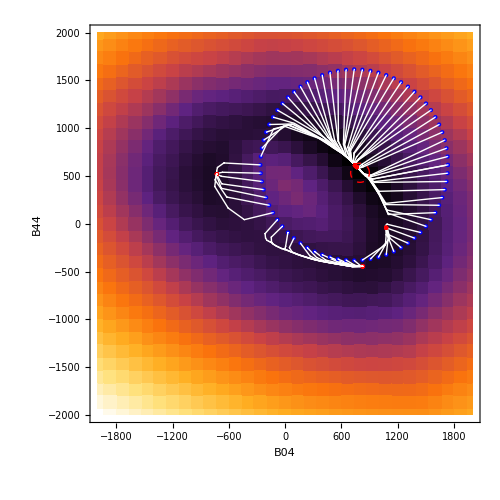

```mathematica
landscape=Flatten[landscapes[problemVars][[1]],1];
bestIndex=Ordering[Last/@landscape,1][[1]];
ListDensityPlot[landscape,InterpolationOrder->0,ColorFunction->"SunsetColors",Epilog->{{{Blue,Point[#[[1]]]},{Red,Point[#[[-1]]]},{White,Line[#]}}&/@histories,
{Red,Dashed,Circle[landscape[[bestIndex]][[;;2]],100]}
},FrameLabel->problemVars,ImageSize->500]
```

```mathematica
histories={};
best=standardValues[[problemVarsPositions]]//N;
solutions={};
Do[
history={};
problemVarsWithStartValues=Transpose[{problemVars,best+1000*{Cos[β],Sin[β]}}];
sol=FindMinimum[
Sum[(expData[[j]][[1]]-PartialHamEigenvalues[B04,B44][j])^2,{j,presentDataIndices}],
problemVarsWithStartValues,
Method->"LevenbergMarquardt",
MaxIterations->2000,
EvaluationMonitor:>(
history=Append[history,problemVars]
)
];
histories=Append[histories,history];
solutions=Append[solutions,(β->sol)];
,
{β,0,360 Degree,5 Degree}
];
```

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindMinimum::sszero will be suppressed during this calculation.

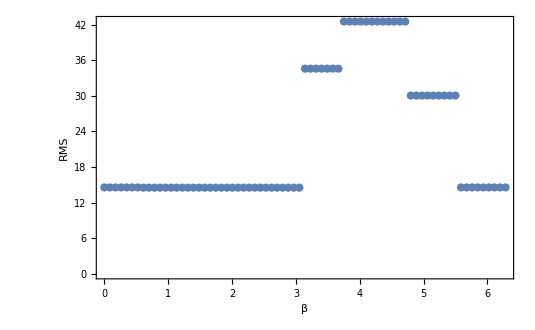

```mathematica
ListPlot[{First[#],Sqrt[Last[#][[1]]]/(√Length[presentDataIndices])}&/@solutions,Frame->True,FrameLabel->{"β","RMS"}]
```

```mathematica
ListPlot3D[landscape]
```

-Graphics3D-

```mathematica
GradientLine[pts_List,color_]:=(
numPoints=Length[pts];
times=Subdivide[0,1,100]//N;
path=Transpose[{Subdivide[0,1,numPoints-1],pts}];
superPoints=Interpolation[path][times];
dxs=Norm/@Prepend[Differences[superPoints],{0,0}];
lineIntegral=Accumulate[dxs];
lineIntegral=lineIntegral/lineIntegral[[-1]];
linePath=Transpose[{lineIntegral,times}];
evenTimes=Interpolation[linePath][times];
evenPoints=Interpolation[superPoints][evenTimes];
Table[{color,
CapForm["Round"],
Opacity[(idx)/Length[superPoints]],
Thickness[0.02*idx/Length[superPoints]],
Line[superPoints[[idx;;idx+1]]]},{idx,1,Length[superPoints]-1}]
)
```

```mathematica
superP=GradientLine[Table[{Cos[β],2*Sin[β]},{β,0,2π,0.01}],Blue];
dxs=Norm/@Prepend[Differences[superP],{0,0}];
```

```mathematica
Length[dxs]
```

101

```mathematica
Interpolation[{{0,{0,0}},{1,{1,1}}}]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

InterpolatingFunction[…]

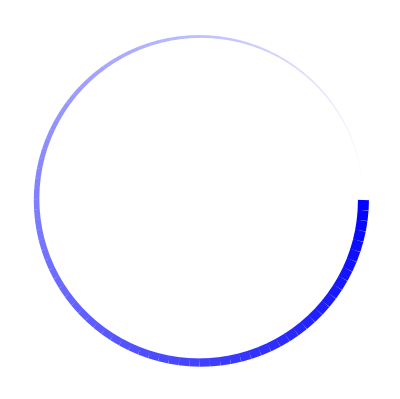

```mathematica
GradientLine[Table[{Cos[β],Sin[β]},{β,0,2π,0.01}],Blue]//Graphics
```

Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

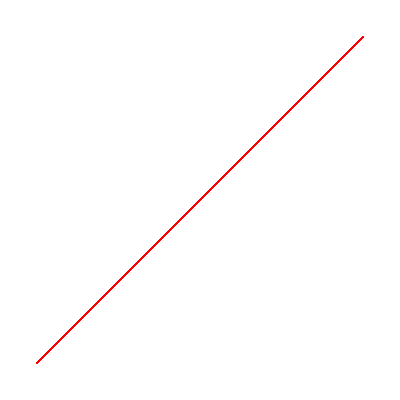

```mathematica
GradientLine[{{0,0},{1,1}},Red]//Graphics
```

```mathematica
ListPlot3D[landscape]
```

-Graphics3D-